```mathematica
Import["C:/Data/501a.csv"]
```

{{9.1384,0.7975},{2.4084,0.24281},{16.721,1.3834},{28.647,1.86},{2.1866,0.21937},{9.7312,0.65688},{15.889,1.4147},{13.139,1.0397},«105194»,{18.763,1.3444},{3.5091,0.35219},{2.5341,0.28188},{2.9425,0.21937},{2.4591,0.26625},{3.0066,0.36},{4.105,0.31313},{6.3416,0.57875}}

```mathematica
Dats = Import["C:/Data/501a.csv"]
```

{{9.1384,0.7975},{2.4084,0.24281},{16.721,1.3834},{28.647,1.86},{2.1866,0.21937},{9.7312,0.65688},{15.889,1.4147},{13.139,1.0397},«105194»,{18.763,1.3444},{3.5091,0.35219},{2.5341,0.28188},{2.9425,0.21937},{2.4591,0.26625},{3.0066,0.36},{4.105,0.31313},{6.3416,0.57875}}

```mathematica
Dats
```

{{9.1384,0.7975},{2.4084,0.24281},{16.721,1.3834},{28.647,1.86},{2.1866,0.21937},{9.7312,0.65688},{15.889,1.4147},{13.139,1.0397},{39.839,1.86},{10.551,0.9225},{14.089,0.85219},{29.831,1.86},{14.76,1.0866},{93.594,1.86},{6.5809,0.5475},{15.392,1.1803},{2.2547,0.20375},«105176»,{2.8916,0.25063},{5.7303,0.32875},{2.0338,0.18812},{15.356,1.2897},{2.2541,0.27406},{7.9531,0.62563},{52.065,1.86},{2.1419,0.25063},{3.2581,0.235},{18.763,1.3444},{3.5091,0.35219},{2.5341,0.28188},{2.9425,0.21937},{2.4591,0.26625},{3.0066,0.36},{4.105,0.31313},{6.3416,0.57875}}

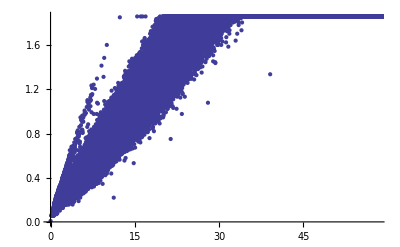

```mathematica
ListPlot[Dats]
```

```mathematica
ListDensityPlot[Dats]
```

```mathematica
testx = [1,2,3,4,5,6]
```

```mathematica
testx = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
testy = {1,1,2,3,4}
```

{1,1,2,3,4}

```mathematica
data=Import["C:/Data/501a.csv","CSV"];
column1=data[[All,1]]
column2=data[[All,2]]
```

{9.1384,2.4084,16.721,28.647,2.1866,9.7312,15.889,13.139,39.839,10.551,14.089,29.831,14.76,93.594,6.5809,15.392,2.2547,2.8091,12.127,3.8491,6.1922,15.213,38.981,29.128,23.634,3.7472,2.595,2.8444,27.798,12.65,11.069,6.3803,13.01,12.342,6.8006,18.671,58.932,18.375,19.276,6.1419,11.065,«105128»,21.382,7.5709,2.5312,97.171,18.366,2.0631,7.5866,28.298,4.7616,15.867,10.268,7.1703,2.4213,1.0809,1.0313,3.5828,13.975,1.5366,45.653,2.6053,14.067,100.94,1.7634,8.1678,2.8916,5.7303,2.0338,15.356,2.2541,7.9531,52.065,2.1419,3.2581,18.763,3.5091,2.5341,2.9425,2.4591,3.0066,4.105,6.3416}

{0.7975,0.24281,1.3834,1.86,0.21937,0.65688,1.4147,1.0397,1.86,0.9225,0.85219,1.86,1.0866,1.86,0.5475,1.1803,0.20375,0.28188,0.9225,0.34438,0.53188,0.87563,1.86,1.8209,1.4381,0.36,0.2975,0.24281,1.7741,0.82875,0.985,0.61781,1.0163,1.0709,0.61781,1.5944,1.86,1.2428,1.6022,0.35219,«105130»,0.64125,0.28969,1.86,1.0475,0.25063,0.5475,1.86,0.40688,1.3209,0.66469,0.65688,0.25844,0.1725,0.18812,0.33656,1.2741,0.20375,1.86,0.20375,1.3288,1.86,0.16469,0.76625,0.25063,0.32875,0.18812,1.2897,0.27406,0.62563,1.86,0.25063,0.235,1.3444,0.35219,0.28188,0.21937,0.26625,0.36,0.31313,0.57875}

```mathematica
ListDensityPlot[{column1,column2,column3}]
```

ListDensityPlot::gmat: {{11.4588}, {9.91887}, {12.0869}, {15.4016}, {9.96763}, {14.8143}, {11.2314}, {12.6373}, {21.4188}, {11.4374}, {16.5327}, {16.0382}, {13.5837}, {50.3194}, {12.0199}, « 21 », {31.6839}, {14.7852}, {12.031}, {17.4392}, {16.8448}, {18.1957}, {18.8694}, {16.129}, {16.2032}, {16.922}, {14.6259}, {18.0538}, {11.4053}, {10.296}, « 105160 »} is not a rectangular array larger than 2 x 2.

ListDensityPlot[{«1»}]

```mathematica
column3 = {column1/column2}
```

{{11.4588,9.91887,12.0869,15.4016,9.96763,14.8143,11.2314,12.6373,21.4188,11.4374,16.5327,16.0382,13.5837,50.3194,12.0199,13.0408,11.066,«105177»,17.4306,10.8112,11.9066,8.22484,12.7121,27.9919,8.54606,13.8643,13.9564,9.96366,8.99,13.4134,9.23606,8.35167,13.1096,10.9574}}

```mathematica
column1
```

{9.1384,2.4084,16.721,28.647,2.1866,9.7312,15.889,13.139,39.839,10.551,14.089,29.831,14.76,93.594,6.5809,15.392,2.2547,2.8091,12.127,3.8491,6.1922,15.213,38.981,29.128,23.634,3.7472,2.595,2.8444,27.798,12.65,11.069,6.3803,13.01,12.342,6.8006,18.671,58.932,18.375,19.276,6.1419,11.065,«105128»,21.382,7.5709,2.5312,97.171,18.366,2.0631,7.5866,28.298,4.7616,15.867,10.268,7.1703,2.4213,1.0809,1.0313,3.5828,13.975,1.5366,45.653,2.6053,14.067,100.94,1.7634,8.1678,2.8916,5.7303,2.0338,15.356,2.2541,7.9531,52.065,2.1419,3.2581,18.763,3.5091,2.5341,2.9425,2.4591,3.0066,4.105,6.3416}

```mathematica
column2
```

{0.7975,0.24281,1.3834,1.86,0.21937,0.65688,1.4147,1.0397,1.86,0.9225,0.85219,1.86,1.0866,1.86,0.5475,1.1803,0.20375,0.28188,0.9225,0.34438,0.53188,0.87563,1.86,1.8209,1.4381,0.36,0.2975,0.24281,1.7741,0.82875,0.985,0.61781,1.0163,1.0709,0.61781,1.5944,1.86,1.2428,1.6022,0.35219,«105130»,0.64125,0.28969,1.86,1.0475,0.25063,0.5475,1.86,0.40688,1.3209,0.66469,0.65688,0.25844,0.1725,0.18812,0.33656,1.2741,0.20375,1.86,0.20375,1.3288,1.86,0.16469,0.76625,0.25063,0.32875,0.18812,1.2897,0.27406,0.62563,1.86,0.25063,0.235,1.3444,0.35219,0.28188,0.21937,0.26625,0.36,0.31313,0.57875}

```mathematica
9.138/.7975
```

11.4583

```mathematica
testx
```

{1,2,3,4,5}

```mathematica
testz = {testx/testy}
```

{{1,2,3/2,4/3,5/4}}

```mathematica
column1
```

{9.1384,2.4084,16.721,28.647,2.1866,9.7312,15.889,13.139,39.839,10.551,14.089,29.831,14.76,93.594,6.5809,15.392,2.2547,2.8091,12.127,3.8491,6.1922,15.213,38.981,29.128,23.634,3.7472,2.595,2.8444,27.798,12.65,11.069,6.3803,13.01,12.342,6.8006,18.671,58.932,18.375,19.276,6.1419,11.065,33.844,35.097,30,30.138,31.475,10.75,11.436,4.1059,2.7413,25.52,33.143,2.1284,6.1866,4.5394,17.387,8.8387,4.9538,24.872,24.036,12.977,19.585,2.3622,6.0778,4.5344,18.245,3.2384,3.1375,8.3488,24.154,9.99,1.9381,2.7272,5.3362,2.9719,2.5647,11.094,4.7491,28.71,10.467,3.6941,103.33,15.359,2.7303,127.25,6.1575,9.9594,3.0013,0.75094,148.46,21.083,5.9641,35.306,2.7394,30.332,33.211,5.3172,2.1734,76.31,99.89,14.897,3.955,2.1916,3.1622,6.1794,14.666,8.1031,2.4047,5.3566,2.9719,4.1159,5.6109,2.0344,18.598,7.2431,17.62,5.9691,9.3387,61.233,20.712,61.3,100.64,118.31,4.6731,49.449,53.01,19.421,14.63,3.6178,6.4734,2.0744,4.4022,2.7928,116.01,2.4559,17.863,3.8009,1.2188,3.57,5.5344,103.39,2.7803,2.8784,85.952,7.8047,4.8947,19.987,6.2034,23.787,15.516,4.985,5.5772,16.344,125.21,6.445,3.1512,8.4106,17.015,2.5375,25.061,4.6912,4.9825,6.5494,2.8728,8.3353,8.5931,2.0622,40.34,17.557,11.141,6.3878,18.197,5.4119,4.0159,22.186,2.6788,8.1422,6.4516,47.361,14.865,3.0297,2.775,38.061,7.3191,2.6603,6.2678,3.2819,9.8703,24.979,2.4891,11.356,21.634,34.045,30.705,32.824,5.3313,11.397,0.91688,0.69437,21.247,1.6425,2.6966,3.1762,4.0875,36.74,3.135,16.018,210.55,6.1125,15.553,7.4731,13.143,14.369,2.3581,5.6534,2.4784,6.5344,13.213,18.949,35.037,2.0563,25.254,6.1528,73.771,4.1106,19.903,21.629,17.691,2.6203,3.6934,22.968,3.0631,12.209,5.3716,4.5494,7.6856,2.5716,18.631,7.5556,3.7791,29.758,7.5966,4.3559,3.4984,12.004,6.9856,3.4488,2.4697,16.389,4.0147,4.7547,5.0556,18.643,6.1456,1.5291,3.08,2.7562,15.289,7.8913,14.941,15.33,1.5388,5.1491,2.49,22.689,5.6788,11.779,6.5384,101.04,4.9384,16.859,2.9731,64.742,4.4166,11.231,4.0134,17.967,11.567,2.76,22.057,4.3003,8.1191,2.7603,5.5809,34.107,60.438,1.6094,3.2591,15.816,14.055,19.276,4.6047,2.8075,2.0194,2.8019,3.9347,15.305,17.815,21.041,2.3044,8.5119,3.2875,28.538,3.8469,21.887,74.437,2.6606,10.153,19.629,66.21,3.0984,14.533,64.032,15.233,6.6863,8.3506,2.7197,23.217,18.125,8.135,19.784,95.666,3.5912,3.2722,1.3575,113.65,2.0422,132.42,23.025,6.0225,3.4669,8.1556,2.4291,9.5312,2.1634,10.719,17.24,32.973,0.23719,11.783,2.7309,1.1697,8.8862,6.975,34.159,17.173,9.3078,5.1788,7.8131,22.085,16.628,66.255,2.8047,122.48,68.792,14.283,12.738,2.3187,33.484,1.8887,76.525,1.7953,2.9066,1.9034,2.8222,2.3519,10.48,14.542,3.6662,2.9012,29.677,10.05,34.286,78.927,7.9109,9.2397,21.537,4.1944,16.142,14.233,27.843,13.677,3.4062,2.0656,20.197,8.4919,2.8334,11.466,3.6628,8.7497,12.49,8.5638,6.1369,15.994,8.9372,34.776,3.0122,80.363,6.4275,28.06,13.12,2.7734,5.8612,2.8975,2.635,11.567,13.425,7.8309,3.2441,2.575,5.2834,1.7866,16.897,20.291,2.2062,2.6709,18.403,32.491,5.5316,86.673,14.239,15.986,7.0072,45.198,30.418,29.422,5.1569,3.0338,15.683,5.3256,37.09,2.3825,3.4188,14.049,2.4188,22.442,11.245,9.1253,3.2691,13.943,13.306,3.1653,14.872,4.2144,95.726,10.632,12.066,3.6969,3.3694,5.3534,13.557,4.9106,12.276,2.3728,16.642,15.662,8.8444,7.6197,3.3909,22.107,12.841,20.742,15.771,3.5997,4.48,76.644,1.8678,8.2409,2.7556,2.9634,22.073,11.729,5.8,16.204,9.4525,3.8931,22.621,12.385,98.335,13.836,12.727,19.922,5.5006,11.67,6.6875,2.8409,3.7475,17.124,11.438,2.7684,20.266,12.233,5.1831,3.1741,34.783,10.227,38.437,23.136,2.2225,6.3725,22.68,10.335,23.545,2.4747,13.88,162.1,2.5838,2.8847,16.791,2.3009,9.6559,91.173,25.548,79.666,4.065,2.3312,26.273,26.482,4.105,7.075,4.3806,7.9212,49.077,2.8228,1.7062,1.1187,21.28,2.3531,41.576,4.9031,11.24,23.322,1.7778,25.918,9.8369,10.41,3.4997,5.3884,3.6478,8.2378,16.008,2.6447,20.122,8.6031,12.885,2.3416,6.9159,2.3894,5.8856,5.5266,1.6275,2.5175,21.381,11.077,4.0284,10.409,36.719,2.6456,139.62,10.213,3.9481,32.474,5.4434,3.7459,20.55,17.274,4.5878,11.199,9.8044,2.6137,29.018,23.379,9.0741,8.7794,11.863,52.222,66.815,3.11,26.106,85.793,6.9216,3.8109,79.098,2.8303,23.411,23.743,6.4203,8.4509,24.169,2.8903,5.6775,10.607,6.8703,18.197,17.583,17.193,3.1291,51.409,1.9519,5.3119,13.367,19.34,3.0784,5.7597,11.434,12.748,123.03,2.8891,9.3066,6.2781,15.475,28.3,2.9966,2.2456,10.597,3.6066,2.7481,6.4772,53.897,14.258,23.167,34.112,30.59,10.489,5.8819,9.5056,7.6922,3.6656,4.8769,1.7666,11.076,2.8016,2.9722,3.5903,3.4734,29.288,7.1284,22.429,25.78,2.84,4.3247,1.765,3.4459,7.6759,15.437,6.8616,3.6969,2.8412,2.8116,2.4919,98.07,2.4759,8.9587,1.2228,3.265,18.48,3.7297,11.988,8.4803,6.7369,21.607,5.1956,5.6062,2.1869,12.197,9.7803,66.642,5.5225,4.2087,20.783,«103870»,4.3391,8.8678,7.3797,3.3431,2.0722,5.56,14.532,8.5856,16.512,6.2022,6.5478,6.6769,15.379,12.443,4.8538,7.8134,7.4372,32.917,4.4913,174.16,3.0581,20.84,30.431,13.977,0.90312,19.063,19.644,17.813,4.5756,4.1663,12.845,16.693,89.09,3.3934,126.15,3.2519,8.8816,10.986,7.4291,21.328,2.0325,2.0884,3.8506,5.0275,16.328,6.0794,2.3834,13.409,3.4953,3.2994,4.9703,3.2547,5.0397,2.6266,2.3472,6.3219,7.3559,1.9306,79.14,10.021,73.939,14.67,11.255,25.755,9.9438,8.9897,13.203,9.1687,3.8434,7.6069,2.4097,1.9094,4.1609,156.09,12.17,2.9109,8.0094,85.201,21.928,14.495,1.8544,27.961,13.38,10.73,4.6278,21.638,22.799,25.634,9.8234,13.363,5.4944,26.647,20.987,6.7141,1.7328,13.718,16.665,107.94,25.485,2.8169,11.755,72.281,7.1456,1.1059,3.6819,14.347,2.4078,10.204,2.1575,4.3756,1.4653,8.2244,8.2972,29.278,2.4681,5.3103,2.9337,8.8825,99.187,7.9681,5.1312,23.319,6.8416,14.546,16.567,10.165,4.2578,14.894,4.8359,16.115,18.004,15.211,14.301,14.255,1.0759,10.497,18.348,1.9944,26.673,2.2497,2.6375,12.748,12.112,133.74,2.9103,32.175,29.795,15.669,30.944,25.907,10.789,3.7662,2.3541,12.608,33.292,13.432,1.6784,6.8969,10.123,3.15,27.093,7.9278,4.8387,2.4231,48.347,9.3656,6.5887,15.732,12.117,24.324,21.628,8.6663,107.36,15.365,3.7681,13.002,11.416,1.9928,15.044,3.8912,17.758,9.5681,21.42,9.5316,34.126,5.6359,191.21,104.01,3.8712,17.919,8.3456,19.595,4.7825,4.0731,25.827,7.4872,2.7775,13.209,20.851,3.2909,3.0925,5.6431,8.9753,26.398,190.73,2.3797,14.112,11.908,10.545,4.9431,7.9097,15.968,8.3372,5.1438,14.853,3.4578,3.4034,1.8663,2.3031,17.713,83.959,3.3216,4.8953,5.7494,25.103,109.75,4.9625,15.185,15.687,35.676,12.858,62.481,103.16,16.628,10.962,7.6725,12.819,1.66,49.121,36.284,8.1506,13.22,8.6119,9.1997,8.2937,2.9172,5.0862,2.8969,2.0441,26.224,2.8669,2.1409,3.6847,5.855,20.953,2.0156,3.0422,15.131,2.4134,3.7522,19.808,26.617,2.4372,26.021,1.1703,4.8878,2.3159,7.3609,4.8837,29.828,19.962,13.986,2.7472,14.473,17.612,26.781,3.8984,7.74,9.445,4.1316,2.1391,30.875,91.31,32.307,8.6694,12.932,26.517,92.311,5.3222,2.4216,3.9203,3.0075,32.803,41.064,3.2147,4.9059,3.4441,52.321,5.8328,73.761,1.4116,3.2184,7.2628,20.815,5.0691,13.742,93.587,8.0475,29.877,4.0903,16.376,13.397,7.5434,12.052,3.7959,9.1722,2.7438,24.077,2.9625,7.3778,2.7497,1.8794,1.8856,12.911,2.7634,114.98,10.496,16.192,14.012,3.3281,16.229,15.411,87.499,2.0831,4.0534,32.296,3.3078,17.613,14.618,113.46,14.778,11.608,5.3094,18.44,23.699,3.4353,22.064,56.082,28.026,18.135,8.2869,15.199,1.7631,21.329,14.41,30.21,11.442,6.3281,23.18,6.9662,3.9616,3.1244,2.58,2.7238,17.328,2.3847,10.454,92.513,40.246,7.1712,11.384,20.944,2.3541,3.1891,9.6134,12.195,2.9672,2.9659,7.8247,5.1656,8.3787,12.151,19.899,18.319,5.04,3.9769,11.13,8.5303,23.106,6.0403,7.1438,5.6234,11.121,4.8484,14.715,2.7616,4.5122,3.1566,10.956,93.623,5.3784,5.6691,6.5731,2.0866,70.523,3.4775,8.9116,10.36,21.625,2.6537,7.0416,3.4966,2.3091,2.9269,11.643,34.366,13.726,13.756,4.6203,26.767,18.099,3.6841,5.1122,29.537,19.167,2.9828,64.346,12.846,3.8331,1.8256,8.3059,14.703,1.68,11.682,35.053,96.641,4.6125,2.7362,30.385,27.466,3.2281,8.4809,13.652,15.075,17.996,6.6666,2.8503,3.5597,1.8047,23.494,4.7306,1.7181,3.0706,33.486,11.391,88.641,19.699,20.24,23.588,14.768,3.4891,22.693,1.8341,3.3941,6.175,3.2469,21.53,37.756,24.409,9.7603,8.4156,1.8897,2.8563,3.2856,4.7628,6.8425,132.22,22.224,11.712,15.398,27.765,65.971,3.5694,12.575,14.516,2.5756,3.5584,6.2875,33.216,5.6528,7.7706,4.4338,27.949,0.84406,2.8537,3.4656,2.0959,10.847,17.646,5.4981,2.5572,26.921,2.6097,14.529,9.0003,8.6384,10.545,34.853,25.453,5.4938,7.3503,4.8562,45.059,22.913,25.298,1.7534,2.1953,12.888,28.608,1.5362,5.795,4.8534,5.3953,3.7141,2.5234,7.2703,5.5359,1.8956,33.067,3.1156,5.4125,27.747,3.3031,12.311,15.748,2.5272,13.349,1.5338,8.9819,28.716,10.677,2.5266,3.5428,2.5825,7.6719,23.569,16.546,17.087,28.448,47.579,4.2312,78.348,21.801,182.61,2.2131,24.99,19.799,75.269,10.392,10.732,2.3116,12.092,7.0531,17.216,14.705,4.0131,33.458,15.737,91.844,2.7994,20.514,2.8034,2.7894,2.8781,28.062,149.87,1.5066,3.3737,10.059,12.221,15.093,16.598,15.566,125.22,32.238,10.948,3.7506,3.9294,8.5528,15.023,14.49,2.6572,6.1525,7.62,19.405,6.6,2.8859,24.243,6.0356,3.1716,7.7178,20.382,1.4556,13.089,10.099,2.4962,2.4256,21.885,3.9575,9.9228,1.7566,16.078,15.94,2.7725,4.6259,14.527,5.7594,173.13,1.9759,3.7278,1.4994,3.6181,15.602,4.7519,16.193,3.0438,2.7697,4.1122,2.2503,21.382,7.5709,2.5312,97.171,18.366,2.0631,7.5866,28.298,4.7616,15.867,10.268,7.1703,2.4213,1.0809,1.0313,3.5828,13.975,1.5366,45.653,2.6053,14.067,100.94,1.7634,8.1678,2.8916,5.7303,2.0338,15.356,2.2541,7.9531,52.065,2.1419,3.2581,18.763,3.5091,2.5341,2.9425,2.4591,3.0066,4.105,6.3416}

```mathematica
Datc
```

```mathematica
Datb = Import["C:/Data/501a.tsv"]
```

{{0.0084375,0.0084375},{0.57437,0.055312},{0.45812,0.055312},{0.42406,0.055312},{0.415,0.055312},{0.41406,0.055312},{0.3925,0.055312},{0.39,0.055312},{0.37312,0.055312},{0.3525,0.055312},{0.30719,0.055312},{0.2925,0.055312},{0.29063,0.055312},{0.27531,0.055312},{0.26562,0.055312},{0.25313,0.055312},{0.24062,0.055312},{0.24031,0.055312},«105175»,{20.628,1.86},{20.457,1.86},{20.443,1.86},{20.424,1.86},{20.407,1.86},{20.398,1.86},{20.36,1.86},{20.347,1.86},{20.183,1.86},{20.001,1.86},{19.964,1.86},{19.963,1.86},{19.474,1.86},{16.909,1.86},{16.377,1.86},{16.044,1.86},{15.415,1.86}}

```mathematica
ListDensityPlot[{{column1,column2,column3}}, Mesh -> All]
```

ListDensityPlot::arrayerr: "{{{9.1384, 2.4084, 16.721, 28.647, 2.1866, 9.7312, 15.889, 13.139, 39.839, 10.551, 14.089, 29.831, 14.76, 93.594, 6.5809, 15.392, 2.2547, 2.8091, 12.127, 3.8491, 6.1922, 15.213, 38.981, 29.128, 23.634, 3.7472, 2.595, 2.8444, 27.798, 12.65, 11.069, 6.3803, 13.01, 12.342, 6.8006, 18.671, 58.932, 18.375, 19.276, 6.1419, 11.065, 33.844, 35.097, 30, 30.138, 31.475, 10.75, 11.436, 4.1059, 2.7413, «105160»}, {«1»}, {{11.4588, 9.91887, 12.0869, 15.4016, 9.96763, 14.8143, 11.2314, «38», 16.922, 14.6259, 18.0538, 11.4053, 10.296, «105160»}}}} must be a valid array. (*ButtonBox[

```mathematica
{{}, {ListDensityPlot[{{«1»}},Mesh->All]}, {}}
```

ListDensityPlot[{{«1»}},Mesh→All]

```mathematica
column1
```

{9.1384,2.4084,16.721,28.647,2.1866,9.7312,15.889,13.139,39.839,10.551,14.089,29.831,14.76,93.594,6.5809,15.392,2.2547,2.8091,12.127,3.8491,6.1922,15.213,38.981,29.128,23.634,3.7472,2.595,2.8444,27.798,12.65,11.069,6.3803,13.01,12.342,6.8006,18.671,58.932,18.375,19.276,6.1419,11.065,33.844,35.097,30,30.138,31.475,10.75,11.436,4.1059,2.7413,25.52,33.143,2.1284,6.1866,4.5394,17.387,8.8387,4.9538,24.872,24.036,12.977,19.585,2.3622,6.0778,4.5344,18.245,3.2384,3.1375,8.3488,24.154,9.99,1.9381,2.7272,5.3362,2.9719,2.5647,11.094,4.7491,28.71,10.467,3.6941,103.33,15.359,2.7303,127.25,6.1575,9.9594,3.0013,0.75094,148.46,21.083,5.9641,35.306,2.7394,30.332,33.211,5.3172,2.1734,76.31,99.89,14.897,3.955,2.1916,3.1622,6.1794,14.666,8.1031,2.4047,5.3566,2.9719,4.1159,5.6109,2.0344,18.598,7.2431,17.62,5.9691,9.3387,61.233,20.712,61.3,100.64,118.31,4.6731,49.449,53.01,19.421,14.63,3.6178,6.4734,2.0744,4.4022,2.7928,116.01,2.4559,17.863,3.8009,1.2188,3.57,5.5344,103.39,2.7803,2.8784,85.952,7.8047,4.8947,19.987,6.2034,23.787,15.516,4.985,5.5772,16.344,125.21,6.445,3.1512,8.4106,17.015,2.5375,25.061,4.6912,4.9825,6.5494,2.8728,8.3353,8.5931,2.0622,40.34,17.557,11.141,6.3878,18.197,5.4119,4.0159,22.186,2.6788,8.1422,6.4516,47.361,14.865,3.0297,2.775,38.061,7.3191,2.6603,6.2678,3.2819,9.8703,24.979,2.4891,11.356,21.634,34.045,30.705,32.824,5.3313,11.397,0.91688,0.69437,21.247,1.6425,2.6966,3.1762,4.0875,36.74,3.135,16.018,210.55,6.1125,15.553,7.4731,13.143,14.369,2.3581,5.6534,2.4784,6.5344,13.213,18.949,35.037,2.0563,25.254,6.1528,73.771,4.1106,19.903,21.629,17.691,2.6203,3.6934,22.968,3.0631,12.209,5.3716,4.5494,7.6856,2.5716,18.631,7.5556,3.7791,29.758,7.5966,4.3559,3.4984,12.004,6.9856,3.4488,2.4697,16.389,4.0147,4.7547,5.0556,18.643,6.1456,1.5291,3.08,2.7562,15.289,7.8913,14.941,15.33,1.5388,5.1491,2.49,22.689,5.6788,11.779,6.5384,101.04,4.9384,16.859,2.9731,64.742,4.4166,11.231,4.0134,17.967,11.567,2.76,22.057,4.3003,8.1191,2.7603,5.5809,34.107,60.438,1.6094,3.2591,15.816,14.055,19.276,4.6047,2.8075,2.0194,2.8019,3.9347,15.305,17.815,21.041,2.3044,8.5119,3.2875,28.538,3.8469,21.887,74.437,2.6606,10.153,19.629,66.21,3.0984,14.533,64.032,15.233,6.6863,8.3506,2.7197,23.217,18.125,8.135,19.784,95.666,3.5912,3.2722,1.3575,113.65,2.0422,132.42,23.025,6.0225,3.4669,8.1556,2.4291,9.5312,2.1634,10.719,17.24,32.973,0.23719,11.783,2.7309,1.1697,8.8862,6.975,34.159,17.173,9.3078,5.1788,7.8131,22.085,16.628,66.255,2.8047,122.48,68.792,14.283,12.738,2.3187,33.484,1.8887,76.525,1.7953,2.9066,1.9034,2.8222,2.3519,10.48,14.542,3.6662,2.9012,29.677,10.05,34.286,78.927,7.9109,9.2397,21.537,4.1944,16.142,14.233,27.843,13.677,3.4062,2.0656,20.197,8.4919,2.8334,11.466,3.6628,8.7497,12.49,8.5638,6.1369,15.994,8.9372,34.776,3.0122,80.363,6.4275,28.06,13.12,2.7734,5.8612,2.8975,2.635,11.567,13.425,7.8309,3.2441,2.575,5.2834,1.7866,16.897,20.291,2.2062,2.6709,18.403,32.491,5.5316,86.673,14.239,15.986,7.0072,45.198,30.418,29.422,5.1569,3.0338,15.683,5.3256,37.09,2.3825,3.4188,14.049,2.4188,22.442,11.245,9.1253,3.2691,13.943,13.306,3.1653,14.872,4.2144,95.726,10.632,12.066,3.6969,3.3694,5.3534,13.557,4.9106,12.276,2.3728,16.642,15.662,8.8444,7.6197,3.3909,22.107,12.841,20.742,15.771,3.5997,4.48,76.644,1.8678,8.2409,2.7556,2.9634,22.073,11.729,5.8,16.204,9.4525,3.8931,22.621,12.385,98.335,13.836,12.727,19.922,5.5006,11.67,6.6875,2.8409,3.7475,17.124,11.438,2.7684,20.266,12.233,5.1831,3.1741,34.783,10.227,38.437,23.136,2.2225,6.3725,22.68,10.335,23.545,2.4747,13.88,162.1,2.5838,2.8847,16.791,2.3009,9.6559,91.173,25.548,79.666,4.065,2.3312,26.273,26.482,4.105,7.075,4.3806,7.9212,49.077,2.8228,1.7062,1.1187,21.28,2.3531,41.576,4.9031,11.24,23.322,1.7778,25.918,9.8369,10.41,3.4997,5.3884,3.6478,8.2378,16.008,2.6447,20.122,8.6031,12.885,2.3416,6.9159,2.3894,5.8856,5.5266,1.6275,2.5175,21.381,11.077,4.0284,10.409,36.719,2.6456,139.62,10.213,3.9481,32.474,5.4434,3.7459,20.55,17.274,4.5878,11.199,9.8044,2.6137,29.018,23.379,9.0741,8.7794,11.863,52.222,66.815,3.11,26.106,85.793,6.9216,3.8109,79.098,2.8303,23.411,23.743,6.4203,8.4509,24.169,2.8903,5.6775,10.607,6.8703,18.197,17.583,17.193,3.1291,51.409,1.9519,5.3119,13.367,19.34,3.0784,5.7597,11.434,12.748,123.03,2.8891,9.3066,6.2781,15.475,28.3,2.9966,2.2456,10.597,3.6066,2.7481,6.4772,53.897,14.258,23.167,34.112,30.59,10.489,5.8819,9.5056,7.6922,3.6656,4.8769,1.7666,11.076,2.8016,2.9722,3.5903,3.4734,29.288,7.1284,22.429,25.78,2.84,4.3247,1.765,3.4459,7.6759,15.437,6.8616,3.6969,2.8412,2.8116,2.4919,98.07,2.4759,8.9587,1.2228,3.265,18.48,3.7297,11.988,8.4803,6.7369,21.607,5.1956,5.6062,2.1869,12.197,9.7803,66.642,5.5225,4.2087,20.783,3.6225,15.724,7.6978,6.3325,2.5931,151.92,3.1875,13.646,4.2456,10.866,27.199,3.4566,2.71,2.8706,9.3831,17.694,15.266,92.388,22.524,27.683,125.79,4.3088,9.7822,2.7459,30.022,2.7528,2.3106,9.1128,4.1062,74.855,6.0928,1.8344,31.607,16.446,2.5984,2.9725,14.273,87.802,2.7675,31.732,18.298,5.4794,6.0447,9.3697,9.395,10.577,2.2144,4.0719,23.218,33.003,95.251,5.515,6.4844,2.4491,2.3197,75.011,4.9403,21.898,8.7028,2.84,6.6034,51.986,19.55,21.441,17.878,12.859,16.985,19.018,2.5697,10.451,3.8069,21.611,3.4428,4.2328,5.2478,2.0609,7.0256,4.7916,9.0022,8.2559,0.81063,98.343,7.8581,5.5106,9.7025,26.528,18.353,6.3934,9.7788,8.5309,3.6931,2.355,19.445,4.6341,6.9944,9.0591,10.151,17.462,18.944,3.0763,2.6622,29.298,2.8156,7.8337,11.511,16.522,22.615,2.0284,5.38,23.174,3.1109,13.949,15.678,50.13,58.109,6.5441,14.967,4.9069,72.211,15.506,2.2316,13.359,9.5722,18.103,27.623,15.619,9.1681,9.6684,1.9044,118.45,27.425,2.76,8.3525,17.564,43.833,138.05,13.133,5.9488,24.863,3.1916,6.9897,93.399,26.755,14.166,10.716,85.533,11.599,2.5512,18.556,10.943,37.766,10.531,14.06,1.7188,4.0325,1.3937,4.8238,75.407,32.198,5.9128,18.645,12.01,2.6609,3.0863,12.951,3.6434,0.98969,24.431,3.7278,18.089,12.174,27.792,17.423,22.243,1.305,3.3428,150.46,8.3325,2.0106,4.2947,23.147,7.3069,6.4825,3.1516,12.367,3.2319,6.9181,2.8434,2.6753,29.495,18.316,71.629,9.0881,1.7369,63.72,2.1656,11.251,22.933,2.5641,55.861,2.6556,25.298,6.5631,37.155,2.1688,8.8337,13.517,8.2137,5.4134,4.9656,30.744,16.583,9.3034,90.538,0.3925,9.3969,4.5275,16.877,3.3737,3.0053,22.313,11.14,2.6116,100.36,9.0853,13.095,13.652,27.107,1.8281,2.0806,16.878,2.5531,4.6419,3.2969,5.1034,9.9228,13.319,25.64,2.6175,18.203,13.571,15.442,2.2987,13.656,44.959,8.7116,6.3219,2.8716,3.0469,12.092,18.205,9.1241,125.93,5.5628,1.7172,18.407,4.0712,7.2972,10.983,5.1241,22.658,17.122,21.195,2.4262,94.757,2.1409,120.17,19.128,10.086,6.4869,13.947,24.358,2.17,13.883,16.915,8.3125,14.712,2.1328,1.2006,2.7441,54.592,2.9191,23.5,131.4,10.878,49.709,2.7119,2.9006,2.6862,28.149,3.6941,14.488,2.8047,71.707,103.28,2.14,2.3041,14.548,3.4213,21.302,9.5381,1.0616,35.496,1.4281,17.294,3.2722,9.9969,13.126,1.9947,2.9769,18.753,21.54,4.4559,9.8628,7.2747,7.7822,5.7359,3.0712,3.9978,25.86,23.65,1.6047,5.2847,27.558,3.2003,8.6947,25.053,18.086,6.2075,2.2941,4.7625,5.54,18.488,11.862,8.9062,16.962,1.8253,30.877,4.1734,11.173,37.877,4.8872,87.933,32.096,13.585,4.69,3.9666,127.07,5.4913,33.124,5.1722,8.2837,22.5,13.295,3.765,6.3497,5.0984,11.155,16.586,94.853,6.7063,2.51,2.0322,10.493,20.092,25.181,0.74594,3.8053,4.4828,16.452,11.13,17.715,10.028,2.8719,15.839,36.07,9.0928,5.6731,12.659,35.59,4.6562,26.135,50.609,38.059,3.675,14.297,2.5875,2.2975,2.7559,11.459,25.504,8.7209,8.8941,9.1853,2.8312,36.038,13.055,25.331,16.779,27.754,17.259,4.6103,16.533,12.96,2.4484,14.571,18.399,14.292,12.615,6.385,3.8094,3.9009,21.922,1.8384,3.5981,12.975,5.1272,11.55,4.0544,2.4734,2.6278,10.969,10.096,26.853,154.28,7.7013,8.4922,23.709,33.338,4.6725,18.613,9.0531,2.4203,1.7884,3.2972,2.7622,2.2797,31.974,2.7303,11.176,2.9706,31.964,7.3787,3.7134,27.909,24.066,140.05,3.2044,2.92,1.7572,111.33,9.0063,4.0084,7.6903,2.6775,2.9809,37.054,4.1438,1.4366,37.01,4.0419,3.3819,14.025,2.2372,29.034,2.5106,6.2881,9.8159,2.0872,22.936,0.81687,5.8431,4.7162,11.098,8.0384,5.2209,35.645,2.2209,90.155,0.99094,22.517,12.366,14.507,14.685,32.401,6.0372,27.793,15.627,20.23,2.3228,30.621,3.7016,3.7159,3.8569,3.2775,2.0013,2.4219,1.6447,4.2494,9.3172,27.496,11.485,8.3003,32.655,10.253,5.6613,3.3828,18.746,29.029,9.4578,2.9734,6.6947,5.615,19.246,37.179,6.7959,4.3791,2.3341,2.4744,1.9972,2.3306,7.27,71.41,162.64,30.834,23.541,4.46,2.6891,25.112,3.4909,7.5219,24.162,2.0409,18.021,3.5547,14.159,49.237,22.992,21.461,5.8094,4.0637,18.058,2.3622,2.705,19.815,28.796,116.66,7.235,8.7444,24.348,22.589,11.871,16.569,14.856,6.6675,2.0897,3.0456,74.596,3.7325,9.5925,1.6253,1.7209,41.115,3.5916,2.7128,21.51,11.209,12.101,83.362,1.5609,8.9056,10.067,3.85,86.098,3.8997,2.1163,3.9678,5.2097,29.624,27.955,2.2531,1.9459,7.7072,19.518,3.7562,5.7875,28.376,2.695,3.8078,5.2228,7.0078,2.4703,11.022,110.3,9.6416,3.6181,2.7384,6.8738,2.6072,28.813,5.2622,10.005,136.21,8.1484,2.1637,1.1859,15.228,1.3937,4.9187,5.6659,17.35,5.82,27.734,35.703,8.8484,9.7631,1.9075,12.337,2.9397,1.5197,13.402,123.09,1.7419,17.061,14.081,30.648,3.2459,5.8706,6.6472,12.559,10.562,18.303,17.255,11.263,1.7731,14.671,8.0134,11.844,14.118,26.606,2.1725,83.228,4.6372,5.4978,3.7037,8.3584,14.709,5.3709,3.2969,2.4631,5.8594,31.457,17.823,4.9397,7.7975,4.5753,134.14,13.716,3.6312,11.803,1.8822,4.1622,43.864,1.8725,26.948,18.698,16.851,9.5972,6.9678,3.1541,6.7853,85.77,23.145,11.017,3.8925,2.0262,35.972,37.113,7.3816,2.4494,5.4778,15.83,4.4166,11.766,8.835,25.448,15.416,4.8231,11.106,1.8291,68.861,11.028,87.527,10.189,5.8941,69.754,18.504,16.896,218.83,67.272,4.9181,17.676,8.4881,10.553,15.563,19.709,11.318,25.996,4.8453,2.6803,11.887,15.851,2.5594,11.461,2.2262,30.857,15.654,14.98,11.05,11.895,82.268,24.824,8.3525,2.1275,138.72,6.8787,80.527,18.313,13.103,115.25,2.3569,1.1572,3.7469,1.83,50.057,15.295,69.591,2.2706,134.94,35.04,175.91,12.832,92.232,8.4741,23.128,9.5231,11.69,5.9691,3.2841,21.226,2.4409,3.7059,76.284,2.5172,1.6803,22.644,30.428,18.227,24.147,25.927,6.0569,2.7247,1.5875,25.906,2.8606,24.747,6.92,5.2416,13.137,3.7066,34.353,5.9806,8.6287,125.31,5.6194,22.663,11.131,8.5781,6.2369,5.8497,9.23,4.7303,8.4963,9.955,3.8991,11.302,5.0016,22.572,11.912,29.961,17.816,16.122,12.088,14.54,20.45,32.381,6.31,7.3819,9.985,5.3734,18.571,4.5206,7.3194,21.111,5.5113,31.798,4.315,20.638,14.486,5.9659,20.954,1.2169,54.994,21.317,23.776,2.4422,9.7319,5.8166,11.571,3.2238,22.442,5.07,18.96,2.8325,19.058,18.929,27.987,3.3722,22.833,11.908,22.905,6.9309,1.6756,32.598,7.2853,44.534,37.126,20.585,1.5066,1.9934,7.1753,94.287,3.4062,19.459,19.782,7.1991,28.691,5.9409,47.031,111.56,2.2528,23.377,6.1594,6.3572,48.85,9.5672,10.352,1.5641,181.86,1.6553,33.658,7.1687,11.606,9.0544,4.9756,23.939,4.7878,4.0744,4.9416,34.548,23.192,9.3709,15.231,117.33,8.7816,22.199,22.567,3.5066,2.5866,3.2056,234.24,1.64,6.2884,10.002,4.2994,2.4766,2.82,10.497,82.951,5.3088,19.152,3.4441,3.5487,4.3403,4.9178,5.7975,11.162,2.5391,76.393,9.3212,3.405,5.8034,2.0309,2.9469,12.933,2.37,1.7506,34.694,4.9094,18.125,15.974,1.1531,5.8181,2.8325,80.078,14.121,2.4341,1.9063,3.9172,24.257,4.6322,2.5334,1.7563,3.1606,18.244,5.9037,12.927,7.0491,3.9794,2.765,6.4403,7.5369,71.81,17.576,2.9453,5.1628,22.133,2.4813,2.7897,4.6566,6.81,1.5844,14.297,95.408,10.4,4.9209,4.1013,4.8966,2.4069,20.373,5.2103,3.9691,42.651,25.996,6.9944,12.791,2.8469,9.8634,19.269,3.1672,2.6866,2.7172,13.649,11.294,8.7381,6.6091,84.599,19.469,20.239,10.631,5.3994,12.848,3.5222,2.8012,3.0675,87.843,84.116,8.4034,28.693,178.93,14.065,10.729,26.796,2.8331,3.4622,9.7231,4.2825,185.26,2.9547,8.9169,10.459,10.231,12.542,12.82,3.12,9.9703,12.538,6.0925,17.67,2.3547,12.204,47.798,24.452,15.696,7.8488,12.341,6.5909,25.02,16.98,14.423,25.437,17.11,9.6788,4.5572,9.7131,6.24,76.108,33.905,3.3903,3.2775,2.2084,2.4878,2.2153,21.844,2.7516,90.463,92.758,4.6588,29.715,90.769,26.097,87.184,4.5338,75.829,2.2722,3.5616,9.3372,2.255,2.8797,16.171,13.171,61.742,1.3934,16.711,9.6378,4.0413,10.571,59.235,16.371,19.154,3.4031,9.8575,2.3134,16.821,2.1431,13.541,6.1119,8.1888,5.0634,28.373,15.658,9.9397,11.358,88.783,3.605,2.3956,11.167,12.151,31.586,6.1613,4.4637,22.142,7.3025,26.483,1.6878,27.964,18.119,1.4478,2.8912,4.2866,3.9291,128.46,4.6706,5.6937,17.448,20.862,118.7,15.86,12.291,1.5734,82.73,124.21,6.1741,8.2269,16.595,19.401,26.944,21.331,7.63,27.545,22.835,17.702,16.215,10.488,9.0903,2.8044,2.8056,7.8334,33.536,11.765,1.4094,21.147,149.54,27.418,17.434,5.1213,66.275,12.001,4.8425,13.898,13.37,36.455,27.998,2.6628,11.188,3.2766,24.279,16.968,3.3703,8.0166,13.493,4.3928,2.9841,18.104,1.8125,37.475,2.7378,123.54,1.8094,128.84,37.387,181.18,30.912,4.575,2.1263,5.5128,2.4278,6.4141,13.534,8.8775,9.015,25.851,6.3384,4.1491,4.9778,16.869,4.6319,4.7166,10.576,2.1728,3.7734,6.3922,4.4719,10.457,20.547,11.275,19.416,3.6769,117.72,3.0203,2.0941,10.722,20.235,23.763,25.728,12.723,2.3997,2.2091,10.617,27.059,4.6822,2.9941,5.5988,5.5603,226.44,3.0422,18.269,4.5741,32.329,109.91,3.5744,24.315,10.81,28.532,19.696,2.3309,5.1141,3.3056,13.096,2.0563,5.5756,9.06,4.2288,2.9606,23.584,2.5334,29.251,2.4531,21.163,21.745,6.8994,2.2366,3.7275,11.457,5.4288,9.0891,12.265,1.3344,13.239,41.312,8.4334,4.4206,19.187,5.8422,4.0291,2.8491,8.1569,9.2403,4.8522,22.969,20.788,2.4437,19.743,17.952,12.053,3.6906,11.542,13.914,7.6687,25.482,2.2516,8.7837,54.66,7.1656,28.123,2.3131,11.701,3.1475,0.33875,1.6744,63.915,2.9966,7.1053,28.984,4.67,13.269,6.5322,5.1606,1.5153,13.7,21.112,6.9903,3.9069,27.604,13.243,5.4891,5.4462,5.7422,7.2712,5.2503,8.5569,10.262,19.629,21.914,127.08,4.8066,20.531,13.592,7.6363,3.0959,8.8853,3.2069,6.5862,3.2266,1.7972,27.719,46.819,6.7834,36.701,4.5241,20.166,35.442,2.3512,2.9819,17.325,29.698,19.103,23.598,90.494,4.8775,8.5834,27.902,2.5925,5.8672,6.0181,111.94,20.343,30.42,4.2594,4.7378,32.431,4.9,2.4281,14.324,16.546,3.3975,3.2147,23.751,11.9,47.013,7.7956,2.3034,19.543,26.216,3.1847,8.9634,133.51,2.7284,31.08,5.6519,4.4172,3.7938,10.581,18.755,17.92,20.089,8.3603,0.46594,19.538,13.911,77.22,11.643,2.7784,14.223,3.8519,15.177,18.077,1.2094,15.618,12.996,13.68,6.1834,19.638,12.425,7.9028,88.152,14.03,14.315,1.9391,11.233,4.1909,8.8966,3.8734,15.462,2.8319,14.783,2.7306,2.5375,8.8353,5.4019,116.42,15.342,19.637,1.9275,14.698,2.4044,29.649,20.014,23.424,4.7937,5.1072,14.563,3.0022,4.4541,5.5856,1.955,3.9441,2.3381,5.1447,34.223,10.794,3.9394,18.349,51.408,17.288,1.7894,11.624,2.8122,6.1628,5.7191,6.73,17.348,16.691,12.687,5.4766,29.298,2.1594,1.9803,6.9006,2.6619,6.2844,7.2791,2.9366,4.8534,8.8062,14.523,25.47,20.457,8.4812,7.8097,80.566,18.915,3.8837,11.527,3.1194,7.1806,7.0662,29.09,33.387,30.54,1.0516,3.275,13.084,6.2784,17.013,42.373,10.207,26.652,10.84,13.055,45.382,3.2169,2.1581,5.8578,9.17,26.393,12.521,6.7472,23.237,3.8916,10.757,5.6434,78.117,4.5816,3.9987,2.9853,69.196,46.101,1.9134,1.5906,7.2472,33.301,12.376,82.658,3.9153,5.255,16.467,12.196,2.7991,20.047,17.745,13.439,2.7991,18.708,27.682,12.081,13.871,28.999,3.43,33.975,99.229,2.3391,29.626,13.053,3.5722,7.48,2.9459,42.375,2.16,2.6806,9.3453,28.291,11.108,4.0381,4.6363,3.1066,2.2741,4.7053,0.99563,6.3356,8.6994,12.782,7.7575,6.2706,6.2441,8.4678,10.656,7.2422,67.375,20.408,20.11,13.612,23.714,13.135,38.18,3.3287,9.41,6.4437,4.7828,33.554,3.7175,18.901,11.818,10.443,17.799,1.1266,14.096,2.0812,20.843,75.035,24.01,4.5166,1.86,12.97,9.8194,2.9909,17.878,11.067,10.703,2.4469,33.508,2.3909,11.093,4.2922,5.74,11.252,9.9697,5.9084,8.825,4.1806,3.5828,3.7738,4.0997,10.87,5.705,5.9212,1.5144,9.5106,3.1688,1.9169,2.2931,18.804,5.7578,3.0972,4.4759,6.5113,78.87,18.073,15.513,2.4769,9.3747,5.135,6.4441,2.1247,14.97,3.1478,12.979,4.8409,3.8119,8.4213,6.8084,19.855,10.741,3.9862,8.9322,28.988,27.402,23.224,7.1306,78.353,6.9369,11.17,3.9916,11.67,16.342,94.832,2.5825,9.2397,3.1225,1.5675,154.94,77.138,4.4884,4.7553,10.363,17.735,20.394,4.9953,2.6019,4.8856,96.029,2.5297,6.8891,7.39,10.679,3.0438,3.7597,30.913,12.539,5.4803,3.0806,2.9,22.017,10.67,2.105,19.861,12.087,32.697,3.2684,10.419,9.5359,7.1188,8.4838,11.589,2.0959,13.042,10.637,2.8963,14.805,9.2903,2.8275,7.0613,18.26,6.8644,27.143,17.359,35.16,2.4975,1.7437,3.2541,3.6203,51.109,3.7794,5.6544,2.765,16.244,5.3844,2.5147,6.0903,31.548,8.4319,4.28,6.6962,2.8647,8.0491,14.886,40.908,14.593,22.257,27.074,2.9794,3.4897,9.6781,6.5666,12.966,5.7613,3.8422,3.7025,4.7187,3.575,20.08,8.5188,5.6172,6.9794,66.611,4.7172,17.496,4.6334,13.03,4.8575,84.73,26.235,6.4575,5.9572,5.5456,16.123,4.0466,112.69,6.1931,1.8741,13.279,5.555,7.4122,27.471,2.03,19.038,2.3378,3.4809,7.5103,9.1453,3.7406,3.0081,4.1084,2.3003,11.504,5.0734,5.4081,1.9497,1.9531,11.417,2.6166,19.998,1.9659,34.671,3.7222,4.27,7.5197,7.5866,8.7644,13.37,35.062,6.7397,23.584,1.1659,3.8519,16.23,22.049,69.879,2.23,6.5794,2.3031,2.2581,18.98,33.416,1.9013,1.8966,5.1822,6.0631,13.461,6.8406,6.4788,1.665,12.692,2.2459,3.1884,11.626,10.044,11.947,115.45,10.371,13.527,101.38,48.029,8.2981,6.5909,3.3169,20.538,16.66,12.532,10.662,27.556,15.478,3.6241,3.8478,57.019,4.1503,2.425,3.2531,37.287,16.357,76.567,15.549,15.281,86.322,12.916,6.7681,4.2722,33.184,11.711,9.4747,5.1484,2.8519,3.8481,14.998,22.706,6.2497,2.3909,0.93063,7.5775,32.36,15.852,5.0869,129.27,16.938,17.731,8.0206,13.78,19.109,2.0528,7.1578,64.826,1.7959,14.499,64.022,13.802,3.0912,78.378,2.5803,5.8328,2.8928,10.288,4.0056,57.638,1.2756,170.92,20.852,51.269,9.5494,3.5669,11.178,3.1034,24.848,16.986,10.453,142.7,9.7722,4.8131,3.2925,5.6066,23.281,7.8469,2.6988,13.165,4.5069,88.849,3.3488,15.356,21.883,30.503,16.055,15.586,5.5931,2.4644,101.87,9.0747,17.743,3.3434,24.167,6.9594,67.464,19.01,4.6238,2.9131,10.785,25.134,3.5044,3.9362,1.0156,28.548,2.4297,12.46,2.305,15.08,3.8963,26.868,95.723,19.456,26.306,13.727,10.507,33.147,5.6384,30.089,5.3888,9.7409,23.932,3.5697,3.9519,3.7841,14.831,2.2481,3.1916,2.7975,27.882,37.611,3.6819,35.986,31.808,6.5219,15.871,21.258,20.375,2.5103,1.9928,10.782,3.2106,130.15,3.1359,4.3422,18.188,7.6928,15.801,15.794,10.906,5.9647,2.9941,66.755,2.9687,11.17,6.3097,28.637,5.7091,1.25,97.136,1.8269,12.344,4.9375,24.798,9.7622,25.199,22.123,7.0419,4.5912,2.9259,8.11,3.3156,2.675,103.58,115,5.4225,20.157,4.5012,92.058,18.904,86.291,82.434,68.537,5.9666,3.1675,4.6537,19.328,3.6547,16.285,4.87,6.9659,4.1097,5.0725,7.5628,2.5647,3.3641,44.175,7.44,5.7525,3.3688,5.66,157.34,31.171,2.4534,8.3922,14.318,24.3,25.047,2.7319,119.68,1.3075,54.295,1.6781,2.7338,9.8375,109.83,30.057,35.884,2.3244,13.329,9.0284,2.4903,12.802,27.272,5.8166,188.72,35.727,11.432,9.6572,10.151,33.723,2.9725,17.772,11.741,33.483,3.5569,23.175,4.73,4.0212,15.077,17.724,10.461,23.051,8.615,6.315,8.7966,24.96,14.992,2.615,224.74,3.0281,2.8881,10.584,2.1391,8.3013,4.0644,2.6322,2.2047,18.948,10.042,38.578,8.8825,5.0588,23.686,3.0509,1.0234,6.0609,10.461,26.468,3.3097,34.275,29.798,12.434,11.05,2.0988,7.4069,1.855,7.8494,6.8525,3.53,30.791,18.237,10.433,15.161,7.9759,29.733,70.247,4.7416,66.448,3.4562,2.3822,4.3331,3.305,21.863,6.9166,10.644,34.457,21.132,9.285,4.8409,3.5719,7.8347,1.9141,3.4928,11.876,26.677,1.7028,3.2484,16.048,3.9237,14.706,14.983,19.615,5.6762,2.4159,34.666,17.85,12.607,10.852,33.722,11.135,15.611,2.1531,4.0363,6.1019,4.2041,2.4159,29.701,2.3634,4.6663,1.4425,9.0009,75.182,7.5459,33.639,1.9887,3.2625,2.7403,24.867,10.027,34.968,46.893,52.227,1.5812,13.447,12.883,7.6203,1.4388,5.8706,23.262,4.235,37.769,21.76,3.1644,2.0769,22.733,9.7013,125.15,20.18,1.21,19.251,9.2356,28.499,5.1038,4.3809,8.4675,7.7472,153.94,15.485,2.9266,33.039,111.39,5.2597,16.106,5.9531,98.569,4.1213,1.4941,5.4928,67.461,4.2675,19.363,28.058,28.276,4.275,3.34,22.752,18.472,38.941,17.914,1.8369,68.412,2.8759,11.492,3.76,204.55,5.1347,32.542,4.5166,5.9747,22.476,1.3769,27.585,10.673,210.57,13.774,3.4684,3.0428,3.6284,5.6547,7.7906,8.1019,14.266,7.4106,1.9603,4.6306,3.2584,3.4969,3.3737,32.248,3.0556,6.4972,128.41,3.7581,4.4563,1.7862,6.0147,7.9144,5.2844,2.0228,35.914,36.763,16.769,23.681,0.9875,4.8297,2.9341,35.454,9.9366,20.095,85.919,10.725,58.71,129.71,9.7413,6.1891,10.791,7.1906,2.6762,88.726,6.3475,19.638,2.14,4.3866,3.4056,7.9766,3.6634,9.4597,5.3463,13.092,27.693,2.6619,48.374,90.893,17.583,30.89,16.989,30.652,20.378,11.177,69.127,18.401,2.9572,26.548,12.832,2.5575,12.059,5.9009,9.6484,2.8125,7.2969,15.895,10.552,1.985,13.823,16.34,30.814,22.741,7.8303,1.9941,43.685,2.4913,13.1,17.212,28.522,9.9866,31.286,2.7616,10.885,92.937,23.347,109.47,4.2841,3.3688,13.804,14.953,5.5384,2.3112,14.28,8.5653,4.1425,26.777,15.596,5.2091,2.3988,6.5363,24.61,15.221,1.2659,2.5153,3.3672,1.6706,2.7553,20.446,2.7475,24.523,139.01,27.157,8.5919,19.508,7.5181,14.564,2.9541,1.79,1.805,31.542,13.429,4.4641,2.9222,5.9491,9.3225,6.55,5.6603,28.154,11.604,9.8806,25.714,5.6188,92.024,10.476,25.941,2.8309,18.667,2.8259,19.726,15.91,1.93,13.564,3.5156,16.495,3.3628,4.8828,2.9059,4.5256,6.1716,5.7213,18.758,158.06,1.8859,30.699,14.802,2.3019,80.367,2.4659,5.5816,1.9706,27.448,2.8125,29.29,20.055,3.0394,18.503,16.352,1.9891,6.0856,3.0591,11.148,7.8203,9.5181,2.6759,2.3212,75.095,108.64,9.0066,87.177,1.865,2.7475,8.7025,92.152,21.03,4.5425,85.716,6.2206,15.737,2.4941,35.394,2.2622,5.9056,4.6581,2.4059,3.9059,28.59,11.573,5.2491,3.5678,151.34,27.428,28.566,2.3081,14.057,20.11,21.688,8.8287,8.4069,1.3372,2.205,19.92,6.5241,2.5919,92.343,16.73,3.0138,9.3572,2.1681,7.8447,23.601,14.991,8.1159,2.3409,35.198,10.042,3.2319,79.94,4.7391,1.8872,3.0731,5.7959,3.6081,28.953,16.851,3.3128,19.027,55.298,10.916,3.6984,12.225,9.9425,10.613,6.8544,2.8659,6.4081,3.0659,150.69,4.4947,7.3734,2.0303,25.527,1.97,4.7659,10.34,4.2725,1.8369,30.49,7.9325,5.8088,8.7575,2.5981,5.8184,34.319,7.7863,11.414,1.3937,2.4962,4.8269,8.7913,28.166,2.8756,6.5434,2.2209,0.92406,5.7059,15.725,6.4294,4.9541,3.7187,2.0559,3.2006,3.1978,1.9522,2.5131,8.5819,1.9672,1.2478,3.8919,3.235,2.3163,1.8784,1.6463,3.9528,43.772,2.0675,18.042,6.6641,11.703,20.14,8.4687,12.899,8.3572,8.1659,15.743,3.975,58.8,31.551,4.9431,16.29,27.534,2.3412,5.9609,3.1856,5.6347,19.028,6.9456,30.065,9.9653,4.3916,2.5219,7.3212,9.3672,11.436,3.0278,14.982,10.263,1.8403,9.2063,6.9628,78.129,6.9609,14.582,11.878,49.775,2.4972,2.46,7.5862,11.953,5.4972,7.0837,4.8084,4.3437,15.338,1.7841,3.3791,32.135,4.4066,41.805,1.6428,12.374,36.42,26.071,2.5434,73.948,16.628,9.6281,22.125,7.4775,3.5928,10.489,5.6312,1.7647,5.6619,2.5778,6.4441,28.826,4.645,33.846,2.7863,5.1494,5.6122,7.1737,6.6047,6.4153,2.7322,27.016,13.222,5.7653,6.7622,4.4909,3.5234,4.8178,4.2275,16.427,48.165,11.931,2.7634,19.05,5.8741,4.1625,16.555,3.6584,22.592,28.252,10.52,12.892,8.1453,2.0062,9.1319,20.855,23.709,16.737,14.711,16.664,6.5291,74.933,25.152,3.0312,7.6822,3.4938,9.5022,3.3663,2.7438,3.9634,1.9978,6.1438,11.989,8.1109,105.83,2.8409,4.1791,6.7913,3.6472,83.158,10.003,2.2125,90.67,19.61,19.223,25.44,2.53,14.887,2.4978,27.264,16.236,13.491,29.053,4.7494,6.2187,16.488,7.6706,4.3775,18.57,2.6509,1.2309,84.551,5.5031,15.575,47.216,126.38,5.4709,13.696,14.35,4.3609,18.043,8.1222,8.0241,102.91,2.3266,6.2606,21.823,11.219,18.235,20.647,6.2125,24.377,65.457,9.3744,8.6147,2.2641,3.9806,3.2075,2.9353,12.794,19.891,99.761,29.449,30.405,75.466,11.648,5.6709,21.576,10.265,90.556,10.48,14.486,1.2466,26.273,19.761,2.2088,134.48,165.48,4.5581,2.1481,29.327,8.1603,14.077,10.469,7.8622,9.2994,2.4044,13.404,76.663,6.7869,32.968,5.2434,23.286,7.1797,3.15,3.2362,11.964,25.11,13.385,9.1481,101.05,4.2169,3.2966,4.9716,33.229,9.0947,33.221,30.508,20.143,6.0197,2.7197,16.355,20.633,176.56,33.803,27.57,15.739,14.594,10.023,11.238,1.8778,5.9231,18.801,35.39,4.1562,1.9516,1.5888,12.525,6.4484,19.193,7.0728,4.2494,17.611,9.3444,7.02,15.229,7.9128,8.0119,115.63,3.4044,2.1925,1.375,1.3513,3.1169,5.1291,14.995,2.9044,26.4,14.113,3.8691,2.4672,2.0366,12.392,4.5578,1.3991,16.993,5.8122,14.294,11.795,3.6488,120.72,0.9625,3.1256,25.321,20.194,17.483,7.0034,1.3438,26.388,2.7009,6.1419,4.9634,12.786,9.5769,31.554,20.378,12.209,14.417,14.83,5.9878,1.6434,5.3881,24.44,3.4422,16.781,35.295,14.42,3.7122,18.611,4.9819,2.6091,2.3375,10.369,1.9075,5.8894,35.988,3.1153,6.2553,27.737,3.0906,20.477,6.0459,5.1866,19.753,11.124,18.178,2.66,19.336,2.8428,20.253,3.0394,1.5838,9.445,45.531,10.76,9.0859,26.306,2.5991,6.8872,2.8969,3.6856,1.5106,3.5169,12.888,4.8716,15.719,16.872,5.1628,2.6278,28.89,2.9431,12.456,1.7472,10.928,7.6544,5.6959,3.7462,7.0428,5.5772,3.7519,9.1591,77.511,7.9928,44.82,5.9403,6.7688,1.9125,14.682,141.19,15.843,4.1653,7.0522,11.4,7.2434,2.0297,31.251,20.705,7.2419,25.932,21.75,16.39,10.22,23.52,29.473,22.139,7.0822,3.1656,2.74,2.9609,10.965,10.58,13.015,29.281,3.8537,3.0431,74.053,1.99,17.015,1.7906,2.3553,5.8562,2.7169,2.8197,21.645,24.541,15.303,4.2794,11.356,1.4716,6.6153,21.249,1.6653,3.3719,89.141,2.9003,2.4075,4.7241,151.86,4.0316,4.0613,2.6275,5.6737,2.1197,24.577,16.57,31.045,25.91,3.2931,120.66,116.78,13.831,4.6366,3.2275,4.8644,13.093,3.8806,2.1684,2.1934,24.136,11.782,1.9494,136.24,15.657,102.93,2.5525,2.4856,102.82,6.0581,2.8684,30.802,1.3969,2.3856,12.17,14.76,6.4262,18.315,22.243,4.535,12.065,18.241,2.9272,6.18,16.901,1.6159,38.879,6.2578,2.7219,1.4331,4.2812,11.32,2.4141,10.484,6.4756,4.9069,13.358,13.927,1.6303,2.7925,4.6531,2.7741,2.7616,2.5381,17.372,5.1125,36.976,3.0366,10.178,2.7047,3.4866,20.19,15.376,4.5906,2.6356,12.964,15.456,8.0266,31.237,39.88,1.7716,8.9759,3.0125,21.718,13.105,7.7225,12.611,22.179,30.544,7.7413,25.745,90.524,26.237,33.159,26.389,9.6597,12.813,3.7809,11.45,3.7706,5.8125,15.294,32.102,3.32,2.4203,10.514,17.785,3.6728,21.542,1.7191,4.7291,6.9825,19.684,9.6356,3.8481,7.0294,16.045,34.143,2.9756,8.1747,10.203,173.43,8.1656,63.075,8.2934,28.248,19.792,2.3897,2.6106,3.1512,2.68,1.8463,3.1909,1.975,3.2303,4.2734,10.143,9.555,2.3478,189.88,2.0591,31.868,109.75,6.8437,12.913,14.412,10.181,3.1084,2.6991,23.985,9.9247,1.9056,4.3509,20.54,2.4141,5.4816,32.891,2.3325,15.27,3.3875,5.7556,6.3066,29.733,2.4488,1.7972,2.2244,5.6253,22.493,10.289,16.871,6.6184,16.812,44.037,151.88,3.1197,2.1316,9.7575,12.255,106.53,8.5566,2.7144,14.17,2.6309,21.26,76.806,10.992,13.443,1.9041,3.1012,1.9037,34.597,6.0766,3.1688,34.791,4.4434,4.4647,6.4231,2.6312,5.0441,22.717,5.4662,21.219,126.94,9.2525,2.5119,1.5806,7.3575,12.433,12.023,193.1,1.915,18.627,7.6775,12.747,2.7553,1.8522,11.138,14.632,3.4725,19.483,34.769,9.8172,5.3834,3.7878,11.068,10.153,14.479,3.87,4.2556,20.547,5.5194,7.5159,12.715,4.0569,3.2613,17.375,6.8725,40.273,30.573,14.737,8.2841,24.598,23.715,2.0509,8.3763,5.8987,0.88656,4.0759,13.152,24.885,6.3153,45.68,2.1463,31.865,3.9206,10.68,20.903,21.185,4.5603,2.8206,29.236,7.6559,33.767,22.882,33.246,7.1419,10.927,12.417,3.1788,5.9034,4.4328,2.57,15.06,12.844,22.07,23.609,21.673,9.5072,2.0116,4.3369,2.5753,2.0363,6.2162,3.6691,8.69,5.9294,4.3159,12.711,7.4122,4.2562,16.303,3.2456,6.0616,2.1906,8.8912,4.2906,4.0416,2.2341,2.82,89.563,3.3816,1.7594,4.5312,13.489,10.455,7.7866,8.0656,7.4828,5.5375,2.1222,14.74,17.833,4.0331,2.4866,6.5462,29.585,12.834,4.7469,41.29,3.2062,130.09,92.453,2.3916,1.9488,37.822,4.4816,15.991,8.4156,4.5291,4.9647,13.428,2.9278,16.095,2.0738,7.4578,10.584,11.395,1.6456,14.736,3.3869,22.068,1.5553,3.8531,8.5741,10.943,3.9122,3.4406,3.4153,15.249,4.2488,4.6625,41.967,8.2656,10.02,9.9137,3.575,146.55,31.027,10.881,49.1,9.5281,2.1672,19.71,5.9672,4.3612,1.8513,9.0925,5.6516,2.7094,4.4425,19.222,6.2112,2.4816,97.623,8.7688,11.012,11.197,29.037,47,37.778,5.8509,28.083,2.1862,95.792,3.0206,3.5587,115.66,3.6366,9.8428,3.9725,33.891,59.854,6.0212,6.08,27.788,13.136,3.6272,3.7003,7.7094,2.2631,3.0291,3.4669,2.2356,3.8019,2.77,7.0972,4.6575,11.158,80.198,33.747,17.898,3.1416,24.214,2.9944,16.24,30.252,9.72,80.669,9.085,3.2103,2.9131,3.795,1.8228,1.8487,6.0622,10.871,11.05,26.188,4.2128,32.134,4.9678,5.8466,4.0809,21.968,2.2078,14.744,12.536,6.5372,4.67,15.875,4.8566,8.6834,4.0444,7.0984,79.298,8.8675,75.214,9.1378,6.2984,6.6181,4.2353,8.0978,7.82,21.103,7.0572,29.724,0.93281,24.514,176.78,13.002,5.5703,3.06,17.137,6.0075,7.4169,32.829,3.8138,2.7259,2.1303,97.799,10.412,31.111,11.139,7.3575,6.4184,3.4428,18.585,15.639,76.709,21.654,9.1678,4.9541,4.295,5.1969,131.66,28.577,21.011,4.2272,27.706,3.3356,28.125,23.209,1.8447,13.944,4.8412,8.5756,2.6962,26.059,7.4794,186.39,5.5056,18.801,91.868,1.6897,4.2475,1.8781,4.2134,4.9506,3.7309,1.5356,89.612,19.109,12.056,1.5916,20.369,5.5069,5.9784,3.2869,8.0522,93.923,10.586,1.4331,7.3775,13.459,19.255,27.414,8.3181,3.1944,15.841,20.931,88.119,7.9128,13.582,9.3906,4.7712,9.21,20.483,3.1947,25.63,92.439,113.97,4.5375,10.958,10.072,157.95,10.138,2.2169,24.411,83.489,36.829,2.9769,7.6834,2.8831,21.059,2.4428,3.0275,14.998,10.833,3.8363,7.0437,99.311,13.363,14.933,9.9006,13.08,11.417,3.5722,9.7856,14.933,19.688,6.7547,2.1063,22.62,10.365,15.875,6.62,7.2134,2.29,34.465,7.2431,53.861,4.7159,6.3494,33.694,4.9609,4.5684,21.874,8.6919,149.63,2.0712,8.4062,1.8772,14.209,6.4816,20.027,3.5719,27.478,27.711,18.332,8.3106,31.986,4.9894,5.2547,11.729,2.8463,14.756,27.276,68.736,21.745,2.4272,18.476,13.819,2.8644,14.018,23.779,28.785,6.9072,2.3928,12.494,3.0491,5.5366,2.8416,21.798,2.3216,18.527,2.6012,3.5572,8.8147,16.883,31.61,3.185,174.37,1.6953,2.2684,20.255,2.1619,53.639,10.497,1.9225,5.5538,14.376,2.3756,4.2722,70.202,71.599,40.265,7.6719,54.289,2.5056,22.245,50.294,95.656,2.7781,1.7806,10.135,4.4203,24.657,12.341,4.6853,17.757,9.4656,72.69,21.067,7.5806,3.5381,3.3138,2.7759,2.5591,17.04,16.442,2.9794,10.64,12.25,8.5159,6.3981,7.2659,3.5294,14.288,9.6159,4.3594,9.8691,12.557,11.234,13.595,1.8666,47.419,3.4591,2.3131,2.025,4.7259,10.142,26.823,11.234,24.785,2.2925,3.0609,3.1759,20.709,4.2559,10.017,107.06,75.668,3.3312,76.938,35.139,10.92,28.187,5.8991,9.2378,6.3744,36.78,2.8547,9.115,22.839,17.528,3.8375,78.243,27.793,2.0741,3.4294,79.079,6.9356,5.6666,11.692,3.5047,4.7575,0.94687,14.806,38.184,7.0428,13.311,14.794,2.0334,11.207,10.507,14.762,3.1634,7.3106,28.285,90.175,190.78,21.518,2.5872,13.823,19.841,14.278,29.218,2.8166,2.9622,17.457,95.128,0.91281,2.0478,16.353,6.3922,3.0903,9.995,12.584,1.7628,14.261,8.9066,13.028,3.6041,9.1438,6.1109,9.6219,15.656,7.8297,2.47,1.7947,15.811,10.811,16.404,2.9488,16.041,2.015,8.5997,10.497,6.0325,2.1069,94.388,215.69,4.1588,2.4691,88.423,96.876,15.531,4.2025,11.387,45.993,20.68,3.3306,6.5641,2.3397,3.2947,20.438,3.2719,2.3553,2.8563,8.5431,87.07,2.0269,5.1659,14.91,3.2356,15.865,16.996,1.44,3.4822,7.365,12.339,32.768,26.205,11.688,16.49,6.6691,15.684,34.998,2.9762,23.246,1.7125,9.8859,5.5572,13.373,3.1709,116.62,4.7625,3.61,21.077,27.304,8.8369,1.5175,23.766,12.851,10.8,43.814,14.12,31.107,203.29,5.5212,4.3191,19.471,2.3584,3.1813,1.8234,70.624,18.359,22.541,27.956,2.0966,3.6212,4.4891,9.99,3.2581,3.555,5.7066,16.932,6.915,4.8441,3.3475,19.417,72.353,11.893,48.533,7.83,4.5244,8.5737,5.5591,9.5084,26.426,3.5731,34.451,62.632,30.987,5.4109,2.7753,15.466,13.194,15.6,12.187,8.7969,21.907,104.08,6.9216,2.5794,11.72,23.639,13.191,12.365,4.5875,5.5416,10.828,10.568,12.458,11.751,2.455,7.6481,10.491,15.518,12.732,16.861,2.6194,12.986,4.9163,1.7684,14.895,4.4147,4.9447,3.8012,11.107,3.8006,8.5822,32.499,2.6109,75.573,30.951,1.9972,4.3263,5.385,22.373,2.3678,11.549,9.1003,3.6947,28.782,85.216,2.4541,81.764,7.2403,3.1378,21.497,29.197,11.34,11.155,11.938,3.3303,3.0794,18.352,84.971,22.434,2.7203,1.7206,6.115,1.9022,19.375,80.259,10.243,13.201,12.967,14.912,126.27,4.6184,3.5981,2.5831,2.7987,31.658,164.26,2.3841,12.724,13.404,7.98,14.935,3.5369,8.4719,34.122,2.4706,58.388,7.2681,2.6006,2.995,23.612,6.8547,27.81,3.6428,2.9719,79.797,6.0097,4.3991,5.7753,6.1753,3.1466,3.5916,3.9584,8.2806,2.9216,15.316,2.2387,13.309,6.1416,5.4341,8.7447,27.143,2.8072,9.6394,82.555,16.87,4.4041,4.3609,88.078,9.0925,10.324,54.555,6.4037,29.625,9.2341,6.2178,49.174,31.264,28.887,20.418,74.397,3.4462,27.753,5.3466,100.04,13.917,1.975,2.3416,10.882,26.9,1.6263,3.8406,11.333,7.1184,17.656,9.7156,15.795,5.395,3.205,2.2628,3.5712,9.6403,3.4431,10.086,2.3578,10.19,45.325,2.8416,8.965,4.0284,5.4403,4.5287,4.72,11.283,2.8025,7.2728,9.9294,1.425,5.8784,7.2737,9.7422,25.782,3.4025,12.5,6.0503,19.315,95.285,7.3528,13.731,6.1653,2.1834,9.38,7.3197,2.2744,2.5244,48.948,3.6169,41.863,11.504,5.2775,8.0712,37.088,2.9147,18.837,7.4859,123.86,6.0997,14.451,2.4231,9.515,12.434,1.7047,2.0225,2.2053,6.1553,35.344,7.9359,6.9109,11.474,6.7719,24.029,2.6397,20.249,17.527,16.582,48.983,3.7397,2.1209,10.321,29.227,2.2944,2.5219,36.443,135.92,2.8597,3.4403,11.552,9.4884,4.1747,3.6159,14.795,77.454,28.613,10.772,1.6856,5.7737,3.4819,3.8534,4.0919,32.645,11.124,30.264,4.5006,12.674,3.7856,2.6694,16.458,38.416,9.3266,30.769,2.3712,16.277,5.8341,35.198,5.6641,11.026,25.696,14.557,95.914,6.4647,7.5016,5.1741,2.87,191.87,10.294,9.6362,8.5666,5.8331,0.84,2.6859,40.456,18.419,24.611,7.3572,12.365,9.7503,12.811,5.0834,18.03,12.406,9.0747,1.6222,2.94,5.5328,4.9347,30.676,16.751,2.7619,135.92,8.5809,21.421,21.815,27.114,5.2816,12.196,2.8503,4.0872,7.1109,19.636,8.7863,28.33,2.1578,8.9653,2.0312,3.2059,8.8725,11.997,4.44,9.6519,19.468,2.6512,14.452,1.9612,37.104,2.2372,1.71,4.4128,28.012,10.467,15.681,23.744,3.0019,8.9603,1.3756,14.192,0.72812,31.068,1.7694,10.429,3.1037,11.761,2.0644,3.545,6.4972,31.202,33.015,3.9784,2.2309,25.537,3.8909,28.546,4.0525,172.82,2.2881,3.9894,15.727,29.062,117.87,9.4684,15.692,17.079,3.9728,11.487,14.748,17.939,7.0837,2.1469,185.29,37.883,9.2209,6.2288,3.4569,14.326,3.3944,5.1984,9.2075,2.0709,2.2494,31.871,9.5141,2.9047,2.2053,12,11.081,12.769,12.677,22.889,5.6034,6.6859,79.012,18.538,8.1531,7.7463,12.377,3.1381,128.33,16.786,27.08,7.9972,3.2775,2.0725,1.4419,98.043,7.0547,33.336,3.4391,24.966,2.9909,79.743,14.329,31.468,2.6428,1.5472,9.3641,1.8175,7.5756,2.5569,9.5247,11.687,9.3041,7.8628,16.519,10.802,5.3103,9.24,1.5556,1.1191,30.376,15.512,30.403,2.8669,3.0225,13.638,3.3744,45.778,2.1491,24.886,5.7619,157.2,5.9503,113.04,48.237,3.3256,2.1909,4.4609,3.1353,6.6444,17.78,9.4119,7.2919,11.868,3.1216,3.8825,23.748,15.276,98.408,3.05,2.0997,6.9,3.4891,2.6256,7.8916,7.6469,2.7869,13.954,129.34,12.7,102.75,12.971,18.399,2.7969,8.8016,15.259,3.0306,7.9853,5.6741,2.1944,3.2097,2.2722,22.009,34.574,7.1009,15.814,3.0478,14.472,7.5581,4.9563,2.4125,8.1709,10.664,3.2153,7.8212,6.7684,10.453,10.548,1.1234,12.738,25.45,2.9894,2.5491,5.2134,15.008,37.667,95.242,28.755,2.6906,101.52,10.237,3.1478,7.5159,16.981,2.0928,21.63,5.7356,4.9875,2.4181,18.437,7.8928,9.3456,2.6497,7.8313,31.104,7.5853,2.6019,16.477,25.712,6.7609,13.813,9.0084,102.36,38.289,16.835,14.373,5.1459,2.5294,11.125,5.6522,1.5778,2.1766,4.0144,16.779,1.4656,14.395,9.3859,2.1784,8.3344,2.6012,10.872,10.499,5.4212,1.5194,21.812,20.784,7.9166,1.8234,21.741,23.004,4.0184,18.923,17.498,2.5487,3.5812,8.8038,2.9856,10.291,2.3563,6.7397,4.0909,2.7606,3.5241,7.4869,4.6347,2.9272,28.988,142.93,11.111,29.897,8.2416,2.5841,5.5956,6.6984,3.1388,5.0944,11.919,4.2112,18.701,2.5363,4.7925,2.9153,7.4719,4.2469,99.769,2.7372,17.047,14.329,30.754,1.2862,2.9216,6.5631,14.627,10.984,5.14,3.6841,20.475,2.7253,0.89094,11.562,29.405,8.7531,29.83,3.4878,0.95938,2.5672,78.099,10.967,7.1306,11.613,11.36,6.5344,153.52,2.7378,4.7166,2.9022,24.948,1.6903,167.15,8.0675,12.081,5.7441,26.956,28.016,6.27,10.746,3.3044,27.926,22.035,5.7269,2.2034,19.085,2.9288,3.52,1.7153,29.716,37.836,5.1547,9.9625,11.67,15.491,5.4153,5.5,7.9747,2.3287,6.0103,20.207,11.49,12.229,10.453,14.995,19.087,8.3147,12.572,14.493,120.09,10.979,1.7222,3.1319,43.591,17.125,46.974,14.727,2.5278,28.068,8.8881,12.011,25.655,20.47,18.19,3.3387,2.5587,8.1353,15.075,6.5159,2.7672,8,4.3375,77.4,2.2409,10.996,6.2063,2.0341,17.978,9.4987,5.7431,26.148,2.3287,27.88,9.7437,3.1922,1.0234,21.278,18.248,19.454,2.5956,4.2556,3.6044,2.9194,2.3316,23.649,2.9869,6.9684,7.5081,14.285,11.642,2.995,23.378,98.138,131.59,3.6981,4.4909,2.5494,1.6037,28.753,2.105,22.19,12.594,13.444,4.0331,8.4691,2.2722,25.103,35.767,2.7831,23.924,15.635,7.0366,17.091,14.919,2.1025,21.651,2.3584,3.1028,115.74,15.009,3.9319,21.451,5.7922,14.352,28.151,1.7531,32.996,9.5063,2.2709,5.4097,97.487,1.5762,34.662,5.4819,4.3219,11.906,10.824,6.3278,17.911,2.8472,82.144,3.7259,96.724,3.6872,12.085,21.072,14.123,2.6447,12.312,3.7906,2.0166,22.955,2.4222,9.6197,46.049,5.185,8.7887,8.1884,104.07,5.4425,9.2928,177.1,34.507,4.26,1.1313,2.5453,6.6078,21.183,5.4822,24.631,1.735,110.89,9.7166,11.478,30.064,3.3706,75.137,51.218,2.3381,2.0803,2.4738,13.416,31.617,2.3341,3.6003,15.34,56.366,10.784,12.335,13.648,4.6731,8.4666,105.43,8.4531,6.3934,9.7019,125.84,12.301,8.995,26.028,6.8678,7.8159,23.191,14.101,6.5641,122.31,33.488,3.8059,2.3103,6.7344,12.609,29.562,1.7409,9.5822,12.09,14.022,119.18,16.713,67.118,21.634,3.4762,34.242,14.999,2.0634,21.266,2.7441,3.1206,15.584,1.8891,57.363,20.735,12.573,15.709,4.2038,3.6466,6.8972,9.1187,52.849,22.386,4.5384,12.342,16.161,9.5341,4.2947,16.628,2.2459,155.65,5.8397,11.807,8.6384,10.413,2.0619,9.0891,29.039,143.4,109.02,8.8638,1.3434,77.272,12.701,2.6866,12.117,17.494,19.466,14.198,2.2847,13.108,9.3859,12.754,4.6534,58.409,2.3794,4.0491,22.638,1.7162,1.99,2.1422,10.135,24.174,32.144,2.9844,83.577,4.0037,115.79,6.0922,10.582,28.418,14.222,58.778,88.392,6.5519,16.073,4.8528,15.845,16.824,9.7228,2.6212,15.829,1.2066,1.2556,13.81,8.1759,7.2147,63.418,4.7537,89.992,6.4837,34.67,9.5547,2.0084,5.8556,26.324,18.426,10.759,11.559,8.3731,6.1616,16.228,40.037,21.359,12.735,6.8247,6.3522,3.6484,3.6228,3.4131,21.733,5.7369,4.3616,8.0681,94.624,2.0159,34.901,6.0859,3.0825,2.4891,5.2562,9.0044,31.333,13.79,5.9419,2.525,3.3297,7.8631,1.7725,2.76,118.06,8.3356,3.1025,3.6994,4.1013,8.7925,3.0684,11.754,4.8953,12.449,12.179,2.1584,4.1953,2.6422,28.642,4.1019,5.6556,8.7803,2.4819,3.6769,11.71,24.771,5.6891,9.6022,6.2987,11.191,25.986,3.3259,4.1403,4.4156,6.9022,55.381,3.9641,1.1019,34.773,7.7353,3.3238,0.93187,6.8191,6.2553,8.485,4.5381,6.0278,16.309,4.2913,10.182,2.2372,5.1022,14.345,4.2509,7.2112,14.656,2.2997,1.8853,5.0984,2.0528,15.159,80.816,76.813,2.6388,2.0684,15.817,31.215,3.4091,1.4041,2.4388,2.1619,1.9253,8.2541,1.8531,9.2128,88.459,157.26,9.13,3.1094,1.8881,3.9694,3.9188,5.9566,3.3766,103.94,12.687,1.6041,8.8522,19.327,11.298,1.4153,2.2459,14.642,5.2159,9.3247,6.8987,104.14,17.756,31.602,11.837,32.389,16.818,35.87,34.132,1.4834,3.3669,4.0072,21.754,18.674,21.418,13.19,5.2669,10.209,2.1369,167.93,2.6241,6.5191,31.543,4.3481,28.103,10.99,21.076,16.203,24.878,8.5934,107.99,24.868,2.0384,8.3225,18.6,4.0944,4.0975,3.9353,3.1762,21.659,3.7984,5.4544,16.176,2.8816,3.1875,2.1544,4.8806,12.917,14.039,3.5447,29.4,31.004,29.22,10.379,6.45,13.946,8.3572,3.2916,15.318,2.6259,85.431,7.8431,2.3153,19.724,2.6412,51.44,3.2725,5.4887,13.083,3.3491,2.6975,3.5497,8.2444,16.239,3.0131,21.905,26.746,21.634,21.596,22.708,5.8141,34.438,0.56125,2.2931,13.235,2.5175,6.3778,27.91,2.0372,10.194,21.795,2.4069,7.8038,9.6897,2.0934,5.5909,1.6263,5.4172,28.25,2.0181,1.7634,20.129,92.059,14.218,29.902,12.545,1.4697,9.2291,12.216,14.154,20.763,2.4966,2.8978,56.026,4.3566,133.71,11.885,3.3503,10.689,2.4647,4.775,1.5859,4.8356,17.798,2.1022,8.6509,15.198,14.936,2.8366,25.403,30.952,3.4659,4.1425,4.7075,10.737,7.5566,14.474,3.9306,10.958,6.2812,21.167,29.17,11.21,2.22,129.52,17.242,3.88,86.806,8.2041,10.404,11.664,14.139,30.939,16.686,28.005,97.9,2.3247,2.0312,26.993,21.429,1.9869,4.1291,3.4956,1.6009,35.942,2.8978,25.416,25.991,20.425,26.664,36.671,4.1953,2.8963,14.671,27.601,12.465,11.086,6.015,28.178,2.775,14.397,1.5981,16.672,138.08,14.526,201.61,14.201,3.5794,29.728,42.922,2.6159,9.6438,10.424,24.955,28.391,29.948,2.8378,9.4537,59.693,3.1875,2.8497,33.583,37.806,84.579,3.2609,27.323,11.627,12.628,2.5653,4.1891,16.999,5.625,3.1472,2.5922,14.051,5.2297,11.172,2.0491,2.8753,2.9441,16.664,2.2856,1.0628,88.935,4.5719,92.982,13.702,2.055,2.6944,62.379,14.078,3.1175,13.148,32.73,2.4753,74.253,10.378,3.8603,2.3556,11.944,4.1466,1.9025,2.1662,9.2288,31.319,2.7022,17.356,9.7113,77.272,29.232,11.298,4.3722,1.4063,15.747,1.6,13.475,2.6481,1.6662,6.2853,32.964,2.8428,15.07,2.0528,4.4381,1.9741,112.72,12.646,31.042,12.36,22.712,8.0416,7.7184,2.3419,3.9678,2.4053,5.3594,9.5528,9.615,10.829,2.7659,18.999,20.001,3.1469,5.6153,16.229,20.062,16.752,57.851,2.825,2.5616,2.6916,11.056,3.4488,3.4741,7.0887,17.103,4.8056,12.618,1.5569,15.148,2.4078,24.002,16.191,1.9794,58.554,16.071,8.0697,14.697,33.704,2.0722,2.3141,4.3425,76.737,12.002,28.104,17.803,10.834,32.27,2.5512,2.9697,4.2666,1.5328,2.1547,3.6241,3.8294,15.693,36.386,4.8166,79.025,11.689,4.0609,4.4506,1.2222,1.6203,15.182,3.55,3.5469,14.376,5.8137,4.4466,4.2947,3.845,54.12,3.8372,32.951,14.522,31.792,2.0591,15.71,2.7966,7.5613,8.3472,9.3591,6.0409,23.879,2.4284,12.051,6.7622,2.7734,64.593,18.742,17.605,2.4384,3.3556,2.33,1.3362,5.9572,3.6388,82.131,33.897,2.3016,14.245,8.7478,28.517,6.0491,3.3766,23.062,8.5422,8.8562,5.1591,6.1297,5.6125,22.206,11.896,11.194,5.4134,8.7484,4.6744,1.845,87.219,19.097,2.1859,8.2106,31.41,226.67,28.929,11.343,104.62,10.549,3.4416,7.1569,2.21,2.735,6.1356,0.86656,16.738,4.9725,5.8616,3.0966,19.852,18.351,70.2,9.4641,36.47,2.3747,2.0428,20.463,1.7341,7.6319,124.91,3.2675,37.958,11.271,9.7925,10.442,13.846,1.1381,75.834,35.198,29.197,3.9397,46.267,10.395,83.211,1.9825,6.1756,3.9806,9.9103,9.0916,2.7331,31.796,7.3216,34.229,2.1153,8.0716,4.0875,3.9803,30.591,2.8959,76.209,15.969,58.531,12.597,6.1678,80.268,3.8956,4.9631,9.9825,0.57969,2.265,3.8803,9.9522,18.839,6.2269,16.211,26.505,3.7963,12.295,1.5619,19.608,14.939,35.086,4.1241,37.669,22.97,13.085,26.363,29.879,2.5587,1.8575,6.9425,6.6975,2.9544,1.9766,17.137,4.335,4.4294,4.1669,2.8394,11.396,4.5669,7.0966,12.21,95.787,94.944,11.847,16.402,1.4088,26.27,3.3144,2.6722,2.2334,2.5128,3.5153,14.094,6.3116,11.412,4.9006,7.7491,20.995,30.852,2.1937,3.34,8.9137,10.832,2.7534,21.675,20.881,3.0472,2.365,12.831,16.389,10.233,5.0097,14.982,86.741,11.519,2.3625,18.301,5.6731,7.4925,3.3663,2.1588,3.3006,93.47,2.6744,1.4694,2.6544,1.8866,9.4097,1.7466,9.9984,18.8,11.744,17.4,5.7263,31.692,5.0191,11.749,18.224,2.3681,24.215,19.164,75.386,7.7516,7.3153,8.4731,7.3478,27.252,4.4594,7.7928,1.3491,86.208,2.6803,24.079,25.534,11.161,2.2481,11.58,19.636,5.3556,15.226,16.183,68.343,0.84625,13.167,11.452,2.1547,3.1728,3.1853,8.7659,3.6153,3.3391,10.446,80.963,3.7481,2.7991,3.1184,4.4547,26.505,19.347,20.692,31.648,20.449,3.28,17.774,2.3659,12.595,5.6147,0.97969,13.365,25.561,82.304,94.738,32.434,6.9028,6.1363,7.1109,15.765,25.884,3.0116,11.924,2.6819,4.3009,10.482,8.0431,9.0416,2.9353,33.427,5.8397,17.241,20.045,5.3653,32.373,18.81,16.686,0.45969,11.54,0.9425,1.695,6.4247,8.5513,7.5997,97.657,1.5716,2.5275,1.9131,8.8859,4.8109,66.242,2.0066,1.7994,3.3725,2.9191,4.7063,28.204,5.5091,88.266,3.0306,3.7791,8.0406,34.461,5.3272,2.1956,26.036,1.6053,10.593,2.4191,26.709,3.4534,4.1803,5.2144,7.8078,6.2109,22.78,29.848,8.8794,11.618,3.7653,15.328,6.0556,109.94,5.6156,14.716,33.277,0.25938,37.591,5.1684,50.852,3.4731,87.518,32.767,2.1844,37.983,17.65,3.7291,6.8016,2.0159,28.06,12.011,2.1741,14.188,27.465,18.594,56.524,4.3663,4.3431,12.696,2.9237,14.91,6.4041,2.1284,3.1769,134.24,25.724,30.864,2.4716,78.606,73.028,36.885,3.3078,5.8844,1.8909,3.1169,3.6841,29.178,81.624,9.9587,37.585,25.507,5.8325,4.1309,12.411,5.7337,17.826,13.066,22.107,9.79,78.279,3.5969,6.5178,4.9984,1.8506,7.8069,2.2706,5.0303,26.972,1.7684,6.8406,5.1016,24.61,10.347,12.951,18.642,3.5509,187.96,2.7697,68.124,6.6081,56.061,3.2069,10.538,3.4813,3.1169,4.1562,2.9475,11.784,4.2472,4.2053,20.838,2.7719,2.9962,23.386,1.5872,2.1406,10.113,16.188,30.855,4.1962,7.5147,2.3291,4.0669,45.086,18.182,15.185,3.2634,11.71,6.5047,3.6819,5.5669,8.6769,89.304,6.5959,8.8862,12.425,11.365,6.1438,19.339,9.0925,2.9634,5.0284,19.032,2.8166,4.1291,122.91,7.5431,49.232,3.1731,16.454,3.505,38.989,7.8647,14.223,9.4281,9.3425,3.1872,11.899,9.2716,4.6178,2.0066,8.2934,1.7644,2.7447,8.54,18.647,8.7903,22.56,2.0738,2.9294,19.891,18.911,2.08,42.025,3.7703,1.9134,4.2278,80.317,20.497,5.8375,80.049,13.122,4.5606,15.767,6.1575,8.0944,4.5397,3.2331,14.805,3.9116,10.957,2.1797,21.684,2.9806,11.114,3.0906,6.8881,2.6588,4.1878,1.6569,2.0534,19.641,26.131,9.9213,16.107,4.42,20.443,12.262,4.0244,28.986,6.0138,3.7828,2.2606,20.481,9.5775,31.026,23.007,16.747,13.35,1.8091,4.0341,2.3641,42.329,15.268,52.005,6.34,4.1378,41.326,7.5041,7.9653,6.1494,3.7816,4.0053,133.41,3.9662,6.5331,4.7472,14.445,3.0381,96.434,3.7297,2.9356,7.3113,2.6375,13.77,8.9794,6.1519,9.0875,31.585,128.57,4.3169,3.8588,2.1916,15.453,3.6966,8.9038,129.35,3.3294,4.2219,15.696,15.645,10.728,4.1562,17.272,6.7297,8.9259,9.7044,9.3434,4.5609,1.8881,2.3566,91.793,21.068,6.7562,3.4738,1.9281,11.399,4.8891,139.92,14.606,2.9488,2.0972,18.084,3.2253,127.74,86.997,70.674,12.536,6.8953,2.1263,4.89,5.6025,2.5425,13.403,2.3731,74.86,1.2928,20.095,33.424,3.3909,6.9953,79.647,2.2956,7.2778,8.0972,11.552,1.8959,8.6184,3.1628,5.9259,3.9244,24.105,12.901,2.3688,4.2359,15.689,9.0188,3.5622,10.124,1.9103,8.8416,7.3684,18.237,1.8794,29.121,13.337,19.811,3.8594,15.904,4.6922,25.204,5.5869,17.323,4.1238,8.5112,57.296,106.84,10.052,12.786,22.673,5.3791,1.6991,10.514,19.277,6.6847,11.046,2.6606,58.287,5.7512,3.6719,14.217,2.1856,4.7397,3.6166,18.857,4.9634,15.244,16.947,26.686,26.221,5.3119,4.4206,17.278,47.538,7.9184,1.8463,1.4219,80.793,32.951,69.469,1.6691,6.3019,8.5662,12.747,2.6219,7.0325,2.7697,7.5616,19.801,6.3637,13.314,3.1681,2.8991,9.6203,20.872,11.704,11.05,13.224,34.052,7.9344,2.0425,3.6672,29.382,2.4041,22.565,11.454,5.52,4.8897,14.435,24.355,4.7725,15.16,4.9662,2.2963,12.604,17.225,4.9519,3.4634,72.365,11.627,11.868,2.9459,2.1269,3,6.0803,4.0628,9.5216,25.904,2.8744,2.8034,12.45,4.9212,100.68,1.9353,75.548,37.563,38.129,17.872,11.132,27.513,114.88,2.7475,1.8459,7.8341,18.707,14.05,19.885,1.7119,16.785,30.472,3.3937,22.311,13.865,3.0681,1.8481,2.1425,2.8181,8.8413,3.7994,14.368,3.5738,15.93,23.02,2.6866,5.3447,4.5094,2.2787,6.0031,0.98344,2.8578,3.3753,1.9625,6.7478,6.5363,5.6859,13.137,5.1509,6.8275,2.8766,4.3447,8.6422,19.885,12.426,26.406,11.024,15.698,21.949,211.95,1.6303,30.805,17.844,34.007,15.349,27.474,17.424,3.5153,1.3713,6.4481,2.7369,3.7731,9.3584,79.232,2.3441,4.7447,2.3741,83.927,1.8331,7.0837,25.063,5.6337,9.5784,5.8209,8.2338,3.6303,3.4803,3.4519,9.7541,13.969,7.2875,172.91,27.789,4.0237,15.12,2.5294,3.2809,82.351,5.915,3.3112,3.2503,13.701,13.951,2.7206,4.4088,3.0213,10.036,4.3303,10.925,16.717,17.757,17.163,14.319,2.2375,10.819,24.804,8.9038,10.127,3.0206,8.2156,13.281,2.7647,8.9187,24.044,5.2259,15.107,10.45,5.6694,13.576,20.534,14.829,25.936,4.8409,3.6475,16.194,6.5856,8.675,4.8716,12.215,3.1894,2.4003,20.158,3.9675,5.9303,103.38,5.8575,9.6112,8.7984,11.833,2.3106,17.9,1.9528,3.1175,9.9331,16.749,2.615,3.9422,52.05,21.632,1.5822,27.483,5.8644,3.6069,93.811,15.269,9.7612,8.78,24.275,11.316,6.8447,2.0153,14.124,12.511,4.3412,10.218,7.5372,6.5284,30.565,14.797,5.8278,3.6953,27.423,13.497,16.411,13.521,8.4691,42.701,27.91,8.7981,2.405,2.9281,8.145,6.6337,95.868,17.971,1.89,4.1537,15.379,37.653,169.2,7.0431,4.5981,4.2691,1.4538,4.2741,2.2841,33.72,12.108,31.425,2.5347,24.077,2.4034,16.46,4.3484,2.0013,1.9631,21.792,10.244,5.6094,8.3944,37.022,7.7716,1.8212,10.431,10.842,11.284,11.887,13.006,5.8903,28.974,3.465,5.2253,121.01,11.466,3.0181,1.6169,19.199,1.7075,32.592,6.0603,2.5244,12.648,3.3159,8.1622,2.7372,1.6081,80.304,10.769,6.5769,18.892,1.455,4.6553,1.4412,3.5028,19.231,17.578,11.491,143.24,3.4162,30.926,6.8219,7.2175,3.8734,7.0131,21.75,5.8656,2.6019,1.9641,11.075,5.8947,20.853,1.2625,5.0241,20.485,4.3247,133.19,29.949,3.8,3.1041,32.148,2.8128,13.554,12.984,2.7644,13.443,9.2959,84.857,3.0947,5.4106,2.32,39.525,48.588,5.3416,16.533,7.1519,8.1356,7.4366,5.9009,3.9569,3.5937,5.0509,24.656,13.034,29.743,9.3191,31.811,8.8647,18.773,4.3447,5.2734,3.5084,6.6559,128.87,210.69,1.7122,8.4666,6.8275,4.2838,23.675,14.331,31.515,14.427,6.1059,1.1634,199.55,7.4072,2.4394,2.7387,27.861,5.5056,20.927,8.8491,11.422,2.2494,26.443,14.945,2.5022,86.632,14.373,7.3553,3.0406,28.454,5.6097,6.6559,2.2991,18.321,29.881,3.4662,1.6603,91.298,8.8944,1.4984,27.304,2.2969,19.754,6.0484,12.77,8.1341,7.3297,3.1737,3.2628,6.1072,5.0694,11.524,151.53,21.272,9.7822,26.46,1.9978,2.23,8.7028,47.729,10.449,2.6356,5.2787,43.577,4.0487,29.424,2.1459,5.1219,12.911,13.977,3.01,2.3559,32.237,8.3888,6.3888,27.227,4.9462,154.35,30.004,29.169,11.106,8.6872,3.1384,2.4162,6.1253,1.32,4.4078,2.7338,4.6372,10.936,3.7166,19.289,2.5456,2.3097,110.64,5.6656,3.0887,6.4522,7.0591,52.607,4.4281,3.8653,1.9303,2.6353,4.5628,3.9619,20.628,33.518,11.937,11.161,6.2822,14.869,14.409,4.0422,39.706,8.0475,4.1588,13.95,7.895,1.4278,7.2131,20.826,26.396,7.6516,3.2819,99.708,19.462,11.435,5.13,34.627,11.341,2.2938,20.956,9.6556,12.399,10.262,8.7109,2.4716,18.559,26.759,14.428,5.8197,9.1663,8.8006,25.232,12.395,6.6813,6.0197,2.3481,10.435,7.1681,118.18,17.373,22.778,3.2134,2.0341,13.09,75.514,12.672,2.7247,23.85,1.46,2.6622,2.2459,2.4466,5.3619,13.807,29.465,4.1119,3.2,2.5238,3.5569,2.8731,4.6922,109.61,3.19,27.882,3.9687,7.4684,4.7706,3.01,18.622,1.72,86.109,3.7609,4.1509,26.833,26.03,95.915,13.577,4.7134,9.3425,6.1366,2.0753,6.2297,21.733,4.0269,7.1706,76.466,8.0772,2.3909,1.4453,4.0862,5.48,17.435,5.605,30.987,1.0906,7.2059,29.638,28.003,4.4325,2.3937,6.0691,1.8259,169.58,3.3053,11.177,2.7931,6.9106,5.1863,34.942,33.141,8.9256,7.3125,12.034,6.9869,181.1,12.448,12.711,1.78,4.8472,9.0728,4.8709,20.938,16.625,18.563,2.4341,7.5722,19.01,12.77,169.39,11.544,28.995,2.6303,1.2966,3.155,2.9241,2.9922,6.0191,10.608,10.478,10.563,17.041,50.17,4.3187,1.2759,32.257,30.538,102.38,4.3494,2.5019,3.4806,13.119,2.5803,6.8016,19.224,17.012,3.1834,5.8625,98.777,1.9259,4.61,20.738,15.839,7.4981,2.9984,8.6981,16.406,2.1297,10.684,25.975,8.9566,11.154,2.6147,7.3656,5.5763,2.8353,19.039,20.818,4.7716,13.038,6.0797,7.1384,14.292,3.76,16.736,11.561,3.6641,4.5369,103.12,12.533,12.124,53.393,4.6525,3.1809,4.3688,33.594,4.0231,9.4772,217.08,3.5128,3.9509,1.2563,1.6281,8.3234,2.9825,2.2806,1.5847,8.1853,30.782,2.3194,33.742,15.77,35.727,32.885,134.34,2.4703,2.8984,15.597,109.54,6.24,7.0166,3.1175,7.8244,9.1403,2.7566,4.9687,27.92,3.5178,15.361,2.5963,2.165,15.79,8.4575,14.351,9.2359,3.1906,6.0459,14.657,2.24,4.6675,23.166,29.765,2.4341,5.1384,31.878,11.498,6.7441,2.4019,3.1159,90.58,22.497,1.4612,4.3325,15.282,18.33,7.5531,1.7806,9.6538,13.12,3.0631,1.7584,4.3991,15.611,12.412,8.5556,5.5003,3.0303,3.3291,6.7541,9.8787,18.288,20.156,16.558,13.739,12.281,16.926,15.839,11.462,2.4244,32.833,3.4588,15.773,1.7394,7.3041,15.063,16.519,0.85094,2.2438,2.0194,1.0522,20.384,32.874,3.3906,3.6034,25.747,3.2128,40.487,10.901,41.398,17.745,80.652,30.927,5.5878,19.676,19.024,2.5184,12.096,15.507,14.389,5.2456,33.335,8.9113,29.56,3.3241,4.4163,2.7016,11.312,21.343,7.7469,2.2853,31.629,116.42,31.494,3.4406,9.6653,2.6637,3.8244,9.2991,31.679,3.1756,17.632,12.666,16.287,12.279,12.906,6.6606,10.099,14.765,2.3412,8.9125,11.741,7.9187,3.2022,14.154,6.3281,93.742,3.2684,60.535,21.14,3.2184,17.612,4.0941,5.6825,89.549,16.373,47.664,1.9084,12.265,46.185,2.2219,15.862,6.7544,5.7469,4.6781,10.017,1.2025,7.6469,8.6381,17.814,8.7187,4.0078,15.112,15.048,11.322,3.1837,2.0597,75.518,83.132,8.075,9.9291,22.03,3.3125,154.31,5.2506,15.343,7.4734,29.624,15.101,3.6225,5.9747,5.0206,7.7719,6.8331,2.2538,2.7103,3.3441,16.848,4.2191,48.631,5.5944,8.3422,29.989,27.597,2.5087,2.9634,2.4856,22.214,4.2959,2.4562,95.081,3.8712,5.6656,12.625,2.8997,2.1309,2.0644,3.7391,189.09,7.2063,10.531,2.1319,17.132,5.2884,3.0241,3.8559,5.4259,3.1394,3.2159,7.1613,65.065,13.76,2.4519,10.709,3.5187,38.338,3.5844,2.8453,3.9753,12.583,10.589,5.7003,2.78,1.1284,5.7494,3.7181,1.7491,2.9881,3.0431,14.929,126.75,3.3597,17.94,6.4847,87.738,5.7853,0.98281,41.292,85.383,1.5028,29.135,122.1,23.523,2.0047,8.4653,20.147,21.559,2.9062,12.077,16.91,13.538,10.333,25.262,38.389,6.9884,97.345,19.759,2.8759,7.7616,77.404,26.615,4.98,2.4284,8.0337,8.0219,2.8903,2.4784,7.6103,1.9909,3.5006,6.7741,36.04,38.142,1.7275,7.0075,13.537,15.172,8.0278,30.61,3.0512,14.855,18.185,1.5987,3.1253,3.5091,9.9491,92.812,8.8694,5.9791,13.812,5.4969,2.7553,3.6713,1.3875,8.5909,13.237,3.2878,2.2725,5.3416,4.9488,6.3091,33.704,170.38,4.265,3.1603,37.717,0.32531,10.353,15.204,14.593,26.887,9.18,2.6941,2.6859,25.265,19.543,2.0984,2.3119,13.337,4.2272,10.38,7.5019,78.899,8.3975,3.2172,14.653,48.321,7.25,2.63,13.505,14.855,93.827,7.5584,6.2778,27.422,142.74,4.8597,18.898,20.347,22.713,5.7519,5.0906,11.991,172.66,9.6881,4.1741,13.111,3.7678,62.214,7.2384,5.0041,53.19,5.4381,7.6831,10.192,3.1731,19.121,2.8875,4.0759,27.295,1.9063,17.626,7.5559,21.163,30.142,7.8741,10.827,4.4231,38.66,106.5,9.3209,6.8275,14.09,5.6262,51.966,1.6869,5.3319,9.8141,61.432,61.178,28.459,21.559,2.3834,3.8178,10.431,31.414,2.9694,4.3328,90.667,22.325,56.14,4.0419,14.364,0.91125,3.5881,33.016,21.541,9.9294,7.5,27.822,4.4991,16.474,1.8884,5.4441,9.4359,25.897,2.2538,2.2187,7.4381,32.297,93.567,5.5347,8.3203,1.49,2.5497,2.1137,1.0488,5.6591,6.1678,2.6175,131.64,1.9706,5.2228,6.1737,75.099,8.3697,6.2822,52.546,4.3962,12.747,8.1728,24.682,1.7491,3.9616,4.4744,7.7503,13.178,16.161,7.6625,3.2434,26.052,9.3728,9.8766,44.149,2.2734,12.898,8.3372,2.5603,135.24,9.3941,1.8741,9.9153,18.622,13.099,4.3016,18.395,35.001,3.2606,18.082,18.744,10.766,0.89438,2.9969,8.8144,12.598,5.5619,21.351,9.1256,27.772,4.8162,2.6844,46.768,5.0934,16.323,3.6041,4.295,12.037,91.86,1.9037,6.5766,3.5781,12.546,13.934,29.782,5.2441,2.6044,3.1012,18.75,5.3562,4.3147,12.632,16.186,10.174,2.1784,6.7719,13.451,9.0516,2.6044,11.943,1.7391,1.9181,11.544,4.9041,19.233,5.6709,17.097,14.675,95.219,10.811,4.5528,17.276,24.16,2.4544,11.564,37.801,22.073,13.188,4.3691,88.955,3.7644,2.6431,5.1909,8.7247,5.73,5.0969,4.2916,8.8997,2.1606,5.4328,3.2387,6.0081,3.4159,10.677,14.132,3.1391,6.785,1.77,10.305,10.569,4.0109,66.505,1.2844,20.161,30.463,3.2606,15.472,5.5675,5.6484,10.603,8.5688,94.678,5.2797,10.745,2.3163,18.585,3.2022,2.5853,4.2191,13.71,1.4919,3.0228,13.438,5.3847,3.7009,1.9872,2.7309,12.179,2.2534,2.8906,8.7472,25.924,8.1856,9.8894,161.66,9.7816,11.908,7.1784,7.3738,9.8669,2.8219,18.781,2.2547,16.38,71.143,8.8256,3.5409,9.0619,1.4837,110.3,1.7884,2.4284,12.638,33.631,39.848,31.937,9.0466,3.7669,18.589,6.9425,11.357,5.0184,2.7097,19.782,4.0003,3.2472,10.347,6.9341,3.0709,8.6925,10.627,3.8878,1.8469,10.839,4.2175,9.3659,2.465,9.5109,6.6403,6.6253,4.9659,10.263,24.217,124.37,56.981,4.7009,23.286,3.9603,34.157,3.655,3.9559,26.06,13.575,41.134,1.245,11.985,2.5397,15.52,4.1659,12.72,96.408,3.7228,1.9138,21.35,6.6144,15.16,2.7291,7.8284,4.3469,2.8547,8.4738,4.5406,12.945,27.558,25.458,2.7031,12.653,5.1472,8.5703,3.9447,2.225,20.134,4.1562,3.7878,12.69,3.3287,7.0853,14.73,3.1634,3.7978,2.3778,3.2213,4.355,7.6003,19.812,32.204,9.8144,32.717,6.2422,9.5425,3.7278,13.433,2.1153,2.4072,8.3097,3.6813,8.2106,3.5625,3.0469,2.9919,2.5453,7.8825,6.2791,2.9059,2.4206,17.604,20.529,5.9225,1.4628,3.5009,68.613,4.3941,5.2322,5.9725,10.667,11.176,13.014,49.212,4.9866,14.982,36.107,17.938,69.158,3.2709,33.026,11.123,3.8856,18.453,4.7897,27.527,8.875,14.743,92.753,3.3578,2.0463,19.359,18.912,4.0544,15.281,23.359,12.718,4.0853,2.6269,13.774,39.311,9.9072,3.0937,3.6016,2.4562,102.42,129.84,4.2191,11.057,16.82,102.11,25.888,12.905,197.14,45.802,2.6006,14.404,27.038,27.788,2.575,4.7431,5.5931,3.2441,4.3056,8.6438,7.9647,39.362,2.9897,1.0625,2.2062,21.85,110.54,2.6163,6.7694,19.392,2.7159,2.3456,2.9794,22.696,4.3366,8.4644,3.7728,4.5541,1.8737,2.8969,2.1662,10.871,9.6459,6.3288,27.185,5.8503,4.4416,5.3134,11.525,195.81,7.6184,7.8734,9.1422,10.627,47.836,7.8022,95.695,13.689,3.8209,5.1413,14.745,6.3044,3.895,3.6897,12.265,8.5253,21.712,11.491,6.3744,2.6106,23.473,3.0494,5.34,2.3012,16.812,8.4487,21.997,3.1197,4.7975,6.0959,2.8909,30.628,1.8288,8.2847,30.294,29.049,53.163,8.1097,9.6056,79.837,8.8772,4.5447,2.2266,6.8888,12.557,17.254,26.15,8.4822,5.5856,2.3331,19.847,2.6675,2.2744,35.396,21.459,2.1,23.214,5.3841,5.1206,4.7706,18.613,13.229,3.3491,3.3328,1.8184,5.5588,10.624,32.355,31.142,2.6319,11.707,16.402,16.399,31.394,25.359,3.2728,110.07,7.5591,206.9,16.438,7.8081,43.243,85.956,14.183,9.6869,28.825,3.5694,32.167,6.17,101.25,13.958,2.8834,11.206,4.2066,1.7684,40.407,5.8422,14.817,21.653,22.694,14.996,65.942,5.9569,33.09,5.9006,14.583,25.944,2.1484,18.319,2.0244,5.1256,6.5937,150.72,3.26,11.961,39.189,60.16,7.895,3.0384,7.7772,3.9784,9.7269,16.072,5.8256,216.92,8.9469,115.96,16.881,175.19,2.5606,2.2178,5.3441,0.94281,3.6191,8.6912,12.344,22.827,12.92,4.6244,26.078,3.1922,1.6659,4.0553,36.24,1.8972,3.4944,1.9262,18.376,14.274,21.199,9.4144,8.2928,11.82,4.7856,3.4309,71.202,8.3272,9.835,7.4344,29.006,9.2878,2.4925,4.5981,3.8178,8.2859,1.9441,8.8459,3.9372,11.61,3.2828,129.07,2.6953,10.027,6.5897,14.72,16.622,18.62,35.187,19.469,3.29,1.7894,11.454,9.1331,5.5394,22.362,3.5853,17.461,7.3853,2.8041,2.3528,2.4725,11.243,2.9562,4.8084,22.055,17.918,15.171,28.938,11.954,2.5803,10.676,7.6556,2.44,43.081,18.932,2.7022,3.3325,2.7394,1.6016,8.1337,9.3116,37.363,6.4347,8.3541,24.532,6.4894,5.0275,8.7478,2.3506,70.061,9.7591,3.6316,2.1747,14.614,4.7328,9.1294,14.872,20.788,4.995,27.158,5.7187,2.0622,2.1266,1.2281,5.9497,3.9313,203.91,1.1616,3.4331,9.3416,10.373,10.252,2.5587,28.676,4.2094,2.3931,7.0356,5.5147,3.7628,4.5778,14.629,1.8725,7.6872,15.283,124.35,6.7806,10.74,3.4731,2.5369,9.8575,14.074,3.7125,2.4566,22.827,1.8266,17.766,1.6841,6.4091,5.6322,14.819,17.404,1.9616,9.2619,36.809,3.505,19.574,132.31,12.013,41.288,2.6028,109.48,3.3959,18.182,12.274,8.8809,31.396,14.959,12.775,4.9716,2.9025,11.99,7.7053,3.3972,9.2094,16.279,9.7694,7.2828,2.5609,4.8906,129.48,2.3241,11.244,93.761,29.932,4.98,71.302,10.136,6.7362,4.9281,3.6316,2.0287,2.0691,1.8297,3.1491,3.2881,8.6431,3.5712,27,2.7131,2.5366,54.772,11.384,2.8997,8.9903,5.8453,4.8022,8.76,19.952,5.0484,9.6253,2.2819,6.6312,1.4594,2.7969,6.0016,20.239,11.722,6.715,36.953,1.7497,7.4981,3.9047,12.992,23.2,2.9938,9.8334,5.2619,4.8422,1.1119,10.084,2.3247,7.8706,29.631,6.4713,12.655,6.7206,1.375,84.769,5.5775,14.864,172.56,30.929,2.57,13.264,2.3072,3.0916,2.6853,8.6062,1.3006,83.241,31.048,20.644,9.12,9.5487,20.624,2.2366,4.7372,1.92,40.03,49.902,120.4,13.279,3.4231,44.256,13.554,147.25,1.5378,15.72,31.101,26.839,85.925,13.826,3.6363,14.466,4.125,12.267,3.6356,2.0459,4.0972,2.46,4.4831,6.4241,1.4925,3.0575,2.7597,4.7484,8.7903,2.5812,11.863,38.345,1.9778,9.9625,19.056,15.399,1.6812,3.5197,17.101,3.3009,20.669,12.382,9.7306,7.3241,86.424,2.5916,10.113,11.565,6.1125,3.7906,132.04,9.9703,2.9303,2.4919,1.9944,33.833,3.0466,1.23,3.6453,5.8134,1.6622,20.136,17.858,44.576,2.0469,1.9241,5.0741,14.164,15.4,2.5738,6.7841,2.7338,2.8756,24.774,7.0584,18.111,28.563,0.68469,9.5334,92.256,7.6769,6.1731,7.4928,25.96,23.877,8.3947,2.5881,4.86,27.878,27.519,9.7163,15.431,3.9297,10.919,27.906,4.3109,5.0434,1.4609,183.91,7.8275,3.1012,6.1134,3.6844,1.7469,2.1469,147.1,8.4875,4.4788,53.037,4.8309,2.8863,12.824,4.4878,17.344,27.087,16.687,3.3387,7.1213,28.248,25.573,76.287,21.622,23.481,2.1731,5.6747,16.376,78.261,14.586,23.217,9.0306,18.62,20.907,22.46,3.3628,3.1713,9.6619,16.447,81.162,6.6462,2.6713,11.388,18.518,5.4094,6.3647,53.908,33.768,2.5559,2.9084,44.318,5.7194,14.847,7.5697,5.175,2.3866,7.4341,11.428,1.9619,9.7,20.584,16.416,11.779,15.422,2.0369,3.0569,7.7284,35.665,4.4225,2.4003,3.5041,34.462,24.512,14.384,13.346,15.449,2.6694,3.4375,2.2272,27.035,2.7134,3.045,6.0122,21.691,111.42,23.798,15.102,14.766,11.35,5.1644,2.6725,17.326,9.1812,7.6863,6.0869,6.5828,3.0334,8.6703,12.223,3.2509,3.0044,5.7022,6.6044,2.1144,4.5034,8.5325,2.1528,2.0006,17.382,2.7697,2.7134,89.501,41.15,4.6809,2.7391,6.1375,29.052,2.5719,19.287,25.279,80.353,3.3394,4.1156,3.1131,4.2553,20.057,122.48,4.4228,22.167,7.44,6.3722,16.162,34.276,13.348,4.4303,27.779,27.344,29.373,2.0141,1.4503,13.783,4.1434,8.7612,8.0947,5.9938,8.25,28.755,6.8628,4.0566,59.741,6.3356,32.946,3.515,28.446,6.4894,6.1363,20.148,5.0316,4.3978,12.53,4.725,18.507,12.578,17.411,3.1434,1.7091,7.9466,4.2031,6.9069,6.1216,20.972,30.41,7.8578,35.472,3.3106,120.82,2.1847,3.6275,9.6294,4.6656,23.42,86.878,27.869,4.4338,3.3894,2.8434,1.9575,3.1153,23.351,102.27,45.426,7.0512,2.0678,71.987,107.76,12.358,15.407,4.0253,79.2,11.366,10.115,6.3184,8.4081,11.767,4.8925,103.01,2.59,2.6147,4.4738,10.415,12.715,2.3419,5.3969,2.9766,5.9584,4.4131,33.463,10.364,1.5056,13.897,3.6053,3.0375,10.506,111.43,15.245,33.386,7.4581,9.1234,7.3081,5.9159,9.7375,3.7331,4.8003,4.5716,5.4094,11.53,5.3281,4.11,9.8725,62.865,27.638,31.402,11.97,1.3306,30.852,4.915,2.02,9.4131,3.0722,2.7441,7.9466,29.946,30.783,1.5063,11.401,73.537,2.2884,19.56,10.31,19.703,14.501,2.3116,13.409,1.9291,8.7172,21.794,2.9466,76.209,105.7,131.44,2.7481,7.8194,12.803,15.48,3.5563,10.838,25.235,5.6194,2.8406,41.213,6.3691,10.272,5.8503,1.6669,80.4,2.2197,3.1575,98.725,3.1778,6.42,3.4288,49.09,7.8209,2.5981,10.938,10.682,3.7447,21.788,7.2544,3.3481,4.4584,4.345,2.3187,34.23,7.4156,9.2966,2.7759,3.275,3.9447,3.0309,6.2319,13.064,15.432,85.039,25.917,2.8206,33.647,89.133,8.4459,4.7981,8.1078,8.6872,20.873,6.01,2.3775,1.5794,7.9806,3.7441,26.606,25.161,31.396,17.786,15.92,83.244,3.3575,3.5044,17.681,1.6478,1.9162,1.7584,17.344,2.6828,11.005,33.982,2.7878,56.123,5.005,2.8153,26.092,20.528,1.275,30.959,1.9784,7.3806,2.6497,5.4309,20.118,23.801,71.248,5.2966,74.637,2.9809,1.9906,7.8762,12.312,10.276,1.3859,3.1428,76.173,4.8994,3.3347,134.84,90.463,4.8734,4.6497,5.5572,5.7116,46.761,12.671,28.159,31.941,10.979,76.665,2.4125,10.143,31.484,115.54,3.3191,2.5741,17.995,12.642,10.199,3.5803,8.4719,4.0169,4.1247,21.992,19.362,4.1972,3.8,8.6594,8.5325,1.8756,19.544,8.8194,3.2972,2.3153,2.2259,4.4869,15.833,8.6322,2.93,6.45,36.148,4.3731,3.5072,16.878,58.327,16.725,14.971,76.143,13.524,4.1066,4.1588,92.971,2.2072,3.5434,38.262,82.227,89.23,3.0825,19.086,1.0366,4.1775,12.759,4.31,9.2731,12.027,4.4969,1.1403,3.3356,19.688,3.2122,25.254,9.7534,2.1084,5.955,81.64,86.436,4.0456,24.18,6.4256,2.7141,4.5809,68.573,5.9441,25.57,42.251,9.0969,2.3022,17.473,13.73,25.933,13.07,2.4188,6.9697,9.0409,18.207,3.6591,9.3866,5.4138,2.6803,7.7641,104.18,2.2019,12.78,5.4763,34.653,19.117,1.3122,27.656,2.9091,4.9875,4.0994,15.055,8.6512,15.082,10.428,5.7191,11.169,12.553,4.6228,11.84,4.1103,8.8212,18.312,85.879,9.5541,3.4856,5.16,15.443,15.33,28.104,4.4028,11.747,12.197,52.479,14.08,7.7431,7.6725,3.6184,5.7906,18.432,28.417,10.114,6.0672,1.0366,4.1141,4.4303,7.2034,3.2059,8.5712,3.6984,22.844,22.681,11.212,1.77,13.726,1.8784,30.988,7.1628,4.415,6.7328,2.7559,3.7528,10.062,28.495,94.679,9.2678,22.741,5.7387,13.434,3.6466,4.8975,5.1206,0.50781,1.9791,7.5325,1.7331,3.1556,10.392,2.825,8.95,26.319,15.48,3.1163,15.519,2.6784,9.4128,3.6653,4.9412,4.0694,68.496,3.2522,39.778,42.703,2.6734,11.36,2.0469,9.6253,48.099,5.1844,6.9747,19.977,9.155,30.615,103.44,2.5906,4.415,11.76,25.5,12.46,2.7259,97.146,13.371,14.208,2.5716,9.0841,1.9031,7.1112,9.4569,20.085,109.17,3.7613,6.0434,3.0516,30.602,2.1225,38.657,2.3588,5.6475,10.509,8.7169,80.978,6.2537,2.6359,25.544,3.4838,1.0497,10.509,2.7856,1.7903,2.4162,4.62,22.051,6.4619,11.229,13.877,10.006,4.4528,42.691,3.1675,10.573,31.778,20.826,6.1506,9.3038,9.4528,3.9466,4.5716,14.598,3.4128,61.444,10.609,5.9122,7.9344,213.51,2.8447,2.5509,17.488,6.9744,5.3991,7.3697,14.725,2.7859,88.147,29.024,99.072,73.846,6.2913,2.4384,10.209,28.696,3.2863,25.067,16.399,24.522,3.2822,17.501,4.3334,14.682,5.8084,25.135,1.9719,39.565,177.93,44.188,4.8747,11.978,9.7703,9.6778,2.6906,2.0591,87.423,2.5447,9.7553,11.587,28.081,19.837,6.355,7.0041,5.8531,2.4972,36.647,16.331,21.759,13.485,2.2125,101.02,3.3897,11.802,3.2431,23.313,6.5828,4.4909,24.082,14.271,3.3172,3.7987,29.838,7.5666,12.302,21.867,3.9375,17.596,10.002,31.008,23.477,3.3953,10.368,4.5887,6.3759,1.6016,13.767,79.264,15.263,2.2559,12.629,13.05,80.747,24.277,8.6831,2.8187,5.7078,13.233,10.956,11.289,90.913,3.6875,14.876,8.1737,5.4534,5.55,4.1875,6.9069,65.358,4.2603,6.6616,10.096,18.975,2.1603,26.548,5.1656,1.7616,18.129,17.259,22.506,10.791,12.947,36.548,21.695,19.784,17.106,9.7244,8.4341,9.0684,2.0375,91.615,18.386,21.039,3.2187,10.97,11.718,5.7725,2.3481,32.31,3.4313,1.5819,7.5413,25.91,1.8428,4.2444,5.1459,3.1994,2.4334,201.71,2.7213,4.1569,13.254,3.8328,3.385,16.787,2.3966,2.7284,4.2703,12.596,2.3853,5.0262,6.3966,3.2066,33.835,5.2103,2.3291,25.746,27.935,11.811,4.4353,8.59,2.3666,10.679,2.5575,18.398,38.351,7.9416,16.893,27.532,27.169,6.79,10.902,4.3625,1.9534,75.239,4.3575,3.3537,4.2322,7.3706,27.045,6.3219,13.22,16.186,11.143,2.8591,2.2956,6.89,29.919,6.7875,7.2375,11.792,27.303,29.007,35.893,3.2419,1.6934,6.3263,22.007,32.448,2.3369,19.389,1.8703,3.6937,7.8034,12.359,11.558,4.5191,11.084,3.3378,13.179,3.1828,23.239,3.3903,11.554,24.153,15.155,27.95,5.4809,13.726,8.0394,4.0728,15.593,18.96,31.012,31.899,11.225,1.5716,12.471,7.4703,0.90875,22.342,1.5125,12.256,12.171,13.172,30.417,81.164,1.9928,38.827,2.8978,7.4722,18.504,9.1572,14.35,25.182,12.479,5.1569,7.7034,30.491,2.5656,4.7691,1.9063,16.727,17.078,2.0944,21.469,34.457,13.875,4.0212,8.6666,53.083,8.7716,92.1,4.6594,25.582,22.544,3.4516,85.772,81.134,6.0709,2.8431,4.7703,21.494,4.2728,17.88,7.1853,13.147,2.1837,4.585,16.665,1.8494,5.1934,4.9587,20.913,4.4291,4.9856,2.2034,2.3797,2.7794,38.012,1.8203,12.525,8.0087,24.28,4.0097,7.495,17.11,93.05,20.346,2.2831,9.1822,13.215,1.8625,8.0706,30.32,23.798,5.2306,5.1016,67.688,1.9994,3.4128,3.4959,10.911,6.7134,2.4128,4.4006,2.1706,13.379,24.341,2.7844,2.2775,4.6625,101.4,2.6397,61.603,5.4809,7.8516,26.882,21.99,7.6859,2.1331,16.591,19.683,2.5759,23.435,14.849,14.141,1.2644,17.906,13.914,16.185,4.0984,7.0175,26.789,74.665,13.221,4.94,5.9747,13.93,7.1866,3.1031,9.6909,28.041,3.2675,4.05,4.7931,16.1,91.052,0.87063,88.343,8.9509,2.7213,3.9397,5.4469,3.6372,81.748,97.897,91.607,14.993,2.3372,6.8378,10.289,3.0391,2.9894,3.5834,45.913,17.863,2.3144,9.6878,33.132,49.877,13.864,59.236,6.3059,96.427,11.381,2.1719,5.4713,3.6872,2.7459,23.494,10.144,3.9944,19.243,23.428,18.564,4.6625,8.3553,173.97,4.2259,14.009,4.9975,18.396,22.548,2.1778,4.2534,1.3003,6.9628,3.0228,9.8194,8.6981,9.1222,37.123,8.9794,73.48,5.8194,10.566,4.25,7.1491,9.3884,1.9859,2.5925,3.5338,126.9,4.4603,21.021,2.0972,16.487,6.1381,18.606,13.825,29.008,2.245,25.563,14.881,2.8559,3.5025,160.03,2.3628,119.8,1.4022,137.61,2.3934,30.215,4.2859,4.1466,3.5544,7.7128,5.5909,1.8603,3.0631,17.854,17.041,6.5203,2.5725,4.3334,15.295,12.822,172.57,5.2441,5.2822,3.1009,5.2112,4.0794,5.8616,1.9966,102.32,3.8106,4.6206,11.809,20.808,32.574,5.1209,1.8644,4.2219,2.7622,6.2781,137.06,2.3394,6.5916,83.237,2.2088,16.461,3.1406,4.3566,4.65,1.0491,9.0903,29.817,18.473,6.0128,80.402,9.5131,2.9191,15.807,4.7994,18.965,15.029,20.702,14.188,8.73,49.547,4.6653,6.4366,6.6006,4.32,5.1025,4.7075,13.137,10.488,7.5903,2.3694,15.587,7.7213,16.529,33.091,23.7,13.334,20.439,19.495,13.007,7.3975,131.29,5.6744,2.3634,2.9634,7.2603,2.9825,19.326,13.275,16.549,15.072,16.175,15.568,98.011,3.86,1.13,10.222,82.533,2.7231,21.071,2.0972,1.6784,9.8097,3.0978,97.138,13.371,9.8212,13.15,22.233,37.154,10.848,5.8831,1.8384,2.3997,8.8247,13.866,2.9625,26.7,83.183,136.79,7.6534,6.115,3.1625,3.3953,1.9103,9.7372,25.341,84.159,1.6413,5.2841,28.227,8.1397,14.706,10.675,5.4212,8.3475,9.3269,3.2384,11.233,4.1716,1.6334,31.762,140.55,2.5672,2.9772,5.3347,9.5887,1.6166,160.06,0.91281,22.985,26.494,4.9778,2.3816,3.4913,13.66,182.86,2.9831,22.144,15.533,7.8475,26.964,2.9447,6.5941,14.837,65.773,25.601,20.363,14.64,11.166,0.83969,7.7728,24.354,9.9003,1.8566,4.3734,15.49,15.433,10.065,0.94687,46.032,8.0841,14.488,18.956,9.5019,2.3891,6.3347,136.41,3.5841,115.39,128.35,9.2522,21.9,21.499,7.3209,3.0116,8.1934,2.0284,2.4887,14.121,16.791,2.7784,1.6491,2.1022,14.574,3.1084,25.608,31.448,12.074,15.568,23.574,2.9566,8.6928,10.459,4.2009,1.8703,41.694,5.5291,6.3913,113.98,16.368,19.64,18.968,6.32,0.67344,10.783,17.68,21.057,6.3059,11.877,6.4034,5.4228,2.3988,12.152,2.5428,152.92,24.913,8.5106,1.8525,9.4594,2.2981,14.443,5.6503,3.6956,1.7041,6.5363,14.521,3.305,142.61,7.495,9.3681,7.3519,8.9503,13.523,97.53,7.5791,4.2334,7.4066,7.6803,109.4,3.5394,12.351,5.4138,2.0563,3.8619,3.0425,132.13,1.7459,3.985,10.979,3.3475,21.106,4.8044,6.1425,29.101,25.212,10.325,5.7784,2.2034,22.885,4.6553,8.9675,3.1516,2.725,51.083,12.329,21.499,3.2234,3.7006,10.291,60.294,37.804,97.023,12.732,11.967,4.19,5.2425,5.1422,8.0031,33.632,10.018,2.9913,1.5241,10.353,8.0409,3.6509,58.659,10.587,2.51,28.875,92.452,23.276,15.965,9.1859,34.449,2.2191,4.4187,7.9812,79.011,4.7753,9.7684,2.1447,6.8009,1.8072,1.5603,3.8569,4.3844,11.058,14.311,3.9631,10.377,11.756,2.1847,104.98,20.343,3.1309,5.5122,16.96,29.312,2.0172,1.8834,2.1422,15.574,2.6725,24.562,18.216,52.745,3.7572,67.325,34.014,3.9162,1.6163,4.2688,6.0497,13.481,125.02,6.0203,7.5494,4.345,6.8956,118.25,2.4384,7.5547,5.6737,20.398,2.6159,10.362,4.9716,32.879,6.26,42.525,3.4222,23.685,7.0609,11.958,5.7606,27.983,3.6756,29.23,15.708,11.18,10.412,11.25,95.208,4.5231,6.9647,23.072,9.5656,16.048,3.9813,2.8369,7.6844,7.7038,10.39,13.206,18.595,17.991,1.3634,4.0869,5.0297,2.7797,7.8159,18.073,8.6628,118.49,7.2806,3.1037,16.234,19.427,10.355,5.9547,7.0919,2.1075,2.01,7.9144,14.947,26.127,102.92,4.1725,2.8125,3.1659,4.5738,2.9313,12.133,14.552,3.1509,3.8922,11.046,18.101,6.2866,3.6559,19.684,27.953,1.9787,14.578,3.6788,6.7625,16.266,8.3387,92.122,11.785,4.3441,8.3009,2.7978,4.6588,2.1731,13.609,13.875,120.96,3.1222,22.719,7.4478,14.488,7.7047,36.392,9.7406,3.5925,15.49,14.88,8.1637,6.4856,5.9538,1.9925,3.0691,32.539,2.8087,4.3081,6.8144,15.498,9.0662,16.694,3.6112,2.6488,1.5409,16.931,20.729,4.9756,1.7872,5.5803,9.6578,28.713,109.27,2.7591,17.138,29.171,0.86531,17.235,14.396,13.744,8.635,14.182,7.015,1.8253,1.9019,2.8928,125.68,16.851,2.205,4.2081,12.029,8.5694,2.9109,12.176,27.808,2.8809,2.1188,8.3694,2.1069,1.8084,8.2356,69.912,14.73,1.9803,1.7619,194.03,9.1134,36.571,11.772,1.6741,4.5437,5.1131,2.6634,11.186,14.92,160.49,2.8716,37.955,1.9813,49.413,4.5578,34.499,10.288,4.56,2.5653,19.601,3.1103,2.0659,128.43,8.7853,3.7825,3.1731,10.567,15.719,17.17,1.9522,14.67,11.409,17.263,8.6362,2.3347,10.659,3.3881,4.1453,34.57,3.58,21.099,11.826,12.807,47.263,3.3922,4.1709,5.2031,4.7013,72.417,8.3194,3.14,93.442,33.748,35.27,2.6734,10.911,6.8938,4.6228,10.009,2.5834,3.6009,3.2762,30.709,9.5678,8.0712,2.5666,2.9697,30.757,4.6737,4.3466,6.0012,4.5231,13.484,34.07,6.1331,4.9147,17.015,7.3625,15.762,5.3094,3.0516,207.84,15.876,10.512,28.498,26.449,5.1769,33.401,3.6041,3.1175,8.1034,21.418,4.6322,16.983,22.803,20.83,3.4503,8.1825,5.9731,4.4072,16.06,9.8081,38.024,20.464,24.903,16.559,11.571,22.48,12.79,2.0847,8.1184,104.43,99.191,5.36,9.43,10.576,23.877,2.3284,2.6628,2.5066,19.119,8.7966,4.7259,35.026,1.6487,91.074,2.3084,8.9956,16.527,3.5569,2.8678,11.624,19.852,1.8981,33.249,5.1166,17.424,84.954,3.1828,34.393,24.276,8.1128,27.649,5.4153,6.2606,3.2284,4.9272,19.126,120.42,2.1347,2.0681,20.483,2.4706,2.335,0.9075,15.977,3.5187,17.05,2.6291,5.2387,3.2947,2.5897,5.6087,4.4706,30.392,10.205,18.474,2.7825,2.1934,8.7113,36.322,10.895,26.61,2.2344,75.786,2.8737,11.008,5.4834,24.229,21.46,2.5944,7.5116,4.4597,8.5019,16.4,4.8431,1.8691,8.8263,19.924,8.4956,13.703,34.62,2.6909,5.2703,11.245,12.188,7.9547,2.9284,5.9778,78.903,91.678,3.3569,20.087,4.1578,2.3306,2.7547,3.1903,25.272,3.0106,7.7025,9.7981,11.898,3.3059,22.977,2.2859,3.2775,3.7378,16.305,10.653,12.463,13.4,181.37,3.7841,15.58,15.348,12.238,37.088,19.744,13.661,8.025,5.6406,175.77,11.272,8.8541,29.237,6.03,16.928,2.9462,3.13,20.312,3.3316,5.4422,2.7984,13.744,4.1413,11.172,5.6984,6.4159,82.457,21.959,19.599,2.9831,6.7331,8.7184,119.8,2.0103,9.4891,34.155,35.046,1.9753,2.5975,19.382,4.0703,26.198,11.43,19.003,15.863,165.51,89.032,14.502,14.833,8.4644,33.261,43.945,29.583,34.472,2.955,1.2444,41.36,12.602,2.3763,51.578,4.8944,8.9228,26.739,15.657,14.873,4.3609,3.6456,164.97,87.635,6.0806,11.392,2.1128,2.4353,8.5094,5.9819,96.12,2.3281,6.3209,21.308,25.1,7.8097,2.5062,5.9691,18.63,15.167,22.138,16.601,4.5269,1.9969,8.0063,7.2328,2.2494,44.162,12.64,24.038,6.2787,17.221,3.4347,32.547,24.215,2.0338,10.041,6.2859,6.9941,199.88,2.0481,22.414,20.233,5.9969,32.451,12.068,8.5275,1.8044,4.405,3.5947,2.5234,15.501,0.43687,8.5566,8.4584,67.322,22.927,7.2328,8.87,15.529,20.562,2.2528,3.4822,33.66,5.755,11.652,7.1522,38.948,20.083,5.9803,3.8781,31.885,2.7416,2.5697,20.818,1.9109,6.5375,2.7828,2.1859,7.1209,13.673,3.8975,34.859,7.5947,4.4103,2.1675,8.7322,11.696,10.653,21.549,5.3016,2.4094,4.2119,2.21,2.3775,2.1688,11.904,98.134,5.4006,4.6234,7.4084,29.914,1.5338,3.1922,2.8103,6.995,2.4819,42.562,1.8706,2.4862,5.2509,10.437,8.9625,9.2437,12.419,2.7803,2.5928,3.4156,8.0925,2.2556,19.584,4.1278,18.621,35.848,24.981,19.468,4.4659,4.3419,5.8284,1.9944,9.9225,16.019,28.283,30.542,8.1184,7.6778,8.5209,4.3084,18.759,2.0812,2.5238,3.4203,3.8516,48.192,28.875,24.61,3.0006,8.645,23.617,2.6956,6.3875,5.9075,3.9559,7.5366,10.227,3.3434,87.027,7.7378,16.252,2.0781,86.557,18.758,3.3888,18.233,2.3916,1.1697,21.16,12.106,11.312,12.028,23.997,2.2575,19.964,4.2253,27.951,148.55,21.818,8.7241,7.1169,17.011,12.463,3.2428,3.9519,3.6728,5.5041,7.5981,3.1359,3.74,8.8381,17.764,17.518,11.267,116.37,2.0034,12.076,11.857,5.7281,2.1597,4.5822,25.947,2.0891,6.3837,8.5722,13.456,5.8137,12.112,1.4937,6.6094,128.86,5.2281,15.923,49.045,3.0091,18.024,18.018,4.7844,2.2716,5.7356,1.9669,18.673,67.01,11.317,26.606,2.0025,60.133,33.832,41.242,10.166,5.8425,4.6569,17.559,10.346,8.3184,14.515,3.3688,7.775,26.551,26.795,86.492,3.5094,3.5181,2.1813,38.577,10.901,2.5438,13.072,20.055,2.3641,5.5703,2.9569,8.1428,2.3116,2.07,19.259,2.8844,12.49,19.877,10.064,12.261,3.745,11.113,10.434,13.318,10.815,2.9675,13.67,1.8747,2.7725,13.531,9.8128,5.5675,7.7337,25.795,41.976,2.7738,7.5869,2.2319,3.3681,41.25,5.6494,3.1037,3.6919,9.7591,5.59,2.4594,40.058,5.1725,9.9797,7.6062,24.741,7.1847,14.802,2.9047,7.6959,2.4753,23.169,9.0988,85.453,12.578,1.7406,7.6687,9.0906,144,23.571,15.293,26.065,36.389,42.218,16.655,18.286,73.028,6.9581,3.3281,33.265,3.1453,7.0062,97.152,27.884,2.2909,14.724,4.5191,4.4262,4.2934,22.452,6.8297,2.6941,18.333,7.8247,6.2597,51.929,6.4259,12.881,5.6219,12.771,2.7884,2.2809,82.137,1.9484,2.1853,15.456,29.19,198.87,31.199,2.1125,61.484,19.85,2.9744,2.0587,3.5775,1.9662,8.7591,16.893,8.1231,26.987,37.891,4.9747,16.637,15.04,12.247,3.9413,7.8669,9.8191,29.635,30.991,4.0491,2.6597,25.903,3.0906,5.9634,34.077,42.807,12.345,5.9481,68.279,6.6716,4.0519,1.9053,18.128,1.9603,5.6597,13.166,9.5953,12.36,38.041,17.034,7.5197,21.471,6.0009,4.0222,12.717,29.587,1.7213,1.7463,6.5256,8.82,7.2141,13.998,12.735,1.4016,38.05,14.912,37.734,3.8563,5.6794,13.333,3.205,9.5316,13.247,22.68,14.458,15.968,2.5609,3.6806,12.053,19.465,6.2337,14.587,7.9847,1.4244,22.939,28.282,6.3006,72.795,11.26,114.8,4.9059,9.5019,12.501,38.308,7.8597,178.08,7.9237,10.31,12.491,8.2506,93.107,16.637,2.3888,8.1944,66.363,32.694,6.0634,6.1775,3.0991,5.2206,96.083,27.793,3.1937,8.4825,17.473,20.228,3.5722,5.8878,16.17,4.8825,2.8784,11.781,25.615,3.5644,3.3041,13.413,2.8956,1.9453,4.9262,3.1984,11.691,2.0453,9.7556,65.372,8.095,11.004,19.274,3.0306,7.8878,5.7866,90.475,5.0637,2.1159,12.142,1.9053,3.7206,11.027,1.9288,2.2559,225.34,6.5347,10.692,2.9403,17.59,29.544,2.6147,18.225,5.7803,1.9369,33.622,11.688,12.521,8.0203,21.678,13.368,12.675,2.8753,25.407,78.983,16.737,10.445,3.3697,3.3206,16.625,92.674,2.395,13.885,3.2153,7.8106,11.743,7.9866,3.2544,26.406,9.5666,3.1922,21.227,2.3028,4.035,28.835,15.141,8.135,43.458,30.632,16.575,12.556,4.7484,6.8469,7.9212,2.0147,6.9059,91.751,1.8384,6.0728,27.517,33.132,10.338,28.76,3.3203,9.0028,3.5091,13.773,4.1547,11.072,13.456,1.9262,3.2947,6.9172,1.9447,3.1191,6.1238,8.2481,4.8394,17.433,1.9525,54.081,3.5103,110.62,9.1597,11.248,11.577,13.996,13.121,7.9491,37.964,11.425,2.0412,7.1191,4.8725,3.0109,9.1672,7.2344,2.2975,2.5097,3.4887,7.4412,18.995,32.112,93.335,11.977,8.0116,8.6509,6.4822,4.2753,36.337,24.546,13.165,31.309,9.095,2.6669,15.814,27.739,22.595,3.9097,11.191,4.7809,12.967,2.3006,133.27,6.2888,4.3669,2.8053,3.8684,2.9034,18.811,1.1116,63.458,8.9697,13.852,13.983,2.1031,16.243,10.168,5.8144,55.145,4.7009,1.6703,2.9537,1.8856,102.89,6.2941,3.2938,11.148,1.2278,2.2887,12.732,31.565,3.2581,19.085,19.902,20.586,4.8391,1.8041,2.0759,9.6287,2.3972,1.9847,19.915,22.217,2.5931,8.33,109.02,93.736,11.457,12.514,18.985,4.6984,20.354,2.5341,14.434,23.44,3.1706,7.7266,2.8891,13.797,15.727,22.085,28.895,9.0078,65.766,17.649,13.557,3.8788,9.5134,5.3137,22.041,7.4591,70.77,9.0566,11.173,34.899,11.423,16.541,27.394,27.31,13.293,14.643,7.6059,10.799,90.675,18.547,7.7225,34.979,93.165,2.6044,30.765,20.921,23.348,177.28,55.861,5.0363,17.023,86.544,11.954,12.012,2.0178,3.15,2.7278,3.6925,148.34,2.2187,16.373,29.552,2.9537,2.6316,25.972,3.9494,26.838,21.528,6.3959,5.7344,7.1119,12.417,21.554,10.287,21.218,16.149,1.9231,2.3597,196.62,6.5678,3.3022,11.016,15.98,4.3625,4.8716,20.757,22.852,18.396,2.7769,4.1766,2.4122,4.035,33.487,2.6806,5.5459,25.102,1.9106,13.544,3.3225,23.351,16.098,95.948,15.541,11.895,2.5634,11.151,19.302,30.434,9.6078,8.3503,13.156,15.595,1.7009,15.182,2.4916,75.014,14.779,4.3775,11.803,12.816,5.6788,34.096,1.9638,6.9763,7.7981,94.629,92.404,12.505,1.8209,3.2569,4.5269,20.105,15.288,2.8009,5.1178,15.67,5.3331,14.782,9.0662,7.6262,69.335,13.871,7.0656,27.834,18.926,2.9481,17.472,11.877,21.772,25.46,9.0538,2.3919,1.9688,167.51,16.089,137.43,5.5975,2.0256,2.4347,2.8375,14.733,4.9056,5.7941,25.139,12.221,2.0931,6.8322,2.7316,4.3044,6.1206,3.5278,5.1078,21.712,2.6997,4.41,5.5569,3.0584,3.7338,5.2719,78.92,12.045,6.0641,29.158,7.4563,15.515,9.0725,2.2916,32.093,13.675,7.4187,33.238,2.6734,3.3922,6.0981,21.134,209.55,93.388,6.4119,24.908,42.342,11.357,127.42,21.607,31.618,1.3384,9.5375,4.5766,6.1584,31.927,1.7659,3.3941,3.1684,3.0359,13.448,2.1981,121.35,8.8866,6.0581,65.695,2.1466,4.855,35.02,21.763,9.2684,7.7916,27.322,5.1234,3.1803,4.4544,2.3403,49.322,23.964,24.188,11.86,11.219,2.0062,17.507,2.3769,5.5084,1.0153,6.6509,1.8725,28.543,15.55,4.6269,3.7194,62.044,2.9088,6.0325,14.313,19.928,2.27,15.841,1.7884,3.3125,28.41,27.162,28.482,10.699,14.581,3.2147,2.075,3.1816,36.4,6.1353,12.621,2.9425,3.8484,2.485,12.452,22.669,4.9812,4.2175,3.0109,3.0944,9.1359,0.8425,14.014,16.534,3.1188,11.431,5.9531,9.0456,12.101,2.8681,11.789,2.6422,8.8116,18.366,15.464,4.2787,4.5541,30.922,2.0863,10.465,8.0166,10.725,10.69,9.03,99.995,1.6894,3.4459,8.0169,14.404,57.163,14.066,27.018,27.334,28.688,1.3587,10.007,20.603,10.323,2.1491,2.3112,6.1616,4.0381,13.299,9.7406,15.06,8.2494,12.102,2.9941,6.7706,3.9447,63.708,2.0731,28.853,25.834,7.5687,3.5487,32.918,3.9084,7.4141,37.998,2.6706,42.549,3.1584,6.6363,6.0953,4.9644,1.1859,136.55,8.78,2.1916,8.0688,5.2484,50.156,7.4691,2.7956,11.292,8.4859,112.71,7.8225,5.3731,5.6356,5.0284,7.9809,6.9228,21.641,2.9322,38.702,5.0347,3.5309,10.318,9.9953,0.82969,121.11,28.31,19.687,3.4216,9.6934,7.2312,52.403,17.074,2.16,7.9478,76.287,4.6169,23.233,13.928,78.284,16.188,8.9253,25.178,3.2784,19.887,24.383,2.8712,3.36,8.1991,4.5956,1.7294,7.9216,75.194,32.549,86.829,6.3619,27.181,2.9066,0.62063,69.188,73.823,3.0763,12.017,6.4275,4.4681,10.394,13.665,29.526,4.8456,29.453,13.504,1.9969,12.109,2.0459,12.145,3.43,2.3928,3.3163,32.08,4.2409,45.562,17.653,17.064,3.0572,39.794,4.4906,4.7619,4.3503,11.38,28.556,1.1066,124.86,4.5069,21.419,2.7875,101.94,5.5534,15.744,14.609,18.912,3.0744,15.689,5.8481,9.6375,9.6925,17.433,9.275,6.9841,4.0344,4.5703,5.475,2.6809,2.0622,25.528,5.5322,13.247,50.358,11.284,4.1916,134.57,15.319,69.009,18.198,8.0003,5.7647,76.145,18.899,116.32,16.41,3.9175,4.2003,28.672,2.4694,28.709,108.94,10.311,4.4088,37.966,29.131,2.9131,132.35,18.371,5.1084,9.1316,3.7178,85.283,3.6978,1.9447,4.8244,7.7684,3.6719,15.305,10.769,23.779,1.6525,178.95,4.7994,3.6744,2.6156,1.8603,6.1769,3.07,31.958,170.93,10.172,16.696,12.153,14.545,13.229,17.781,6.6891,2.5584,5.8584,2.7431,8.3316,4.3209,6.8766,14.983,12.168,31.191,5.7819,6.2856,16.057,2.7713,13.521,4.2894,9.8437,5.6069,21.093,12.474,3.8828,17.994,23.516,2.1931,2.7591,1.14,78.906,2.7922,3.8103,29.494,2.6072,2.5516,4.1997,2.8488,9.8131,3.9819,27.336,3.3131,12.307,2.4969,8.6287,15.703,31.312,6.7525,22.646,26.517,6.9184,3.0719,17.237,2.9716,3.8563,14.621,1.6631,31.095,4.0203,2.2919,4.1844,15.908,11.614,3.2287,18.853,7.0728,9.2338,59.969,2.8788,2.1981,9.3,16.697,62.601,1.4897,5.2294,2.2234,5.97,4.4559,30.357,6.1388,6.4075,37.112,3.3166,81.051,1.9688,80.941,20.342,1.8169,94.616,45.851,9.3837,15.667,1.9206,1.8959,30.206,5.3347,100.17,17.14,6.5984,3.3038,4.6163,15.919,3.2384,27.879,5.0078,5.2516,4.0453,1.9091,49.362,3.7866,4.9237,2.1344,3.7562,81.302,8.1619,1.905,3.8087,17.978,9.5778,73.082,9.0809,9.6522,2.4041,0.845,28.62,1.2713,7.4372,20.626,3.3169,15.372,2.3566,9.9716,29.073,6.27,18.961,2.5431,2.1741,13.563,33.299,2.3497,4.8538,12.608,8.1525,33.822,188.61,4.4506,9.4478,5.6556,107.97,9.85,112.07,12.896,1.8997,1.7644,5.6456,14.729,2.5209,7.0413,10.998,2.5622,9.2969,14.333,4.3622,4.5803,12.378,4.8716,14.748,27.757,1.6253,62.517,41.219,17.221,3.6647,16.986,2.7756,5.8578,2.6734,1.9203,21.591,2.2444,5.7591,7.5847,10.566,2.8047,7.4128,2.065,2.9513,2.7934,8.2594,6.4834,10.02,17.221,8.2672,45.213,2.2144,2.23,9.3647,119.42,3.4019,33.158,6.5834,7.3525,3.1688,4.4075,33.903,2.5953,11.35,79.788,5.5841,3.8547,13.844,26.885,35.415,9.79,14.598,1.8844,14.93,30.329,18.289,9,2.2528,3.4034,14.004,2.6609,1.1419,7.1788,21.904,2.4822,188.38,19.479,58.441,2.0147,1.8634,98.143,6.9731,10.267,10.073,24.4,11.294,4.7541,17.318,54.036,4.3531,192.25,5.7603,16.335,5.0847,7.7084,21.146,5.9275,8.4869,23.691,23.928,5.4687,6.0259,3.2406,38.366,33.065,35.223,9.7959,3.8172,7.8016,2.2016,7.3688,3.5809,6.7731,23.301,3.5997,4.7009,3.5931,11.128,11.275,21,2.0119,3.2056,115.27,3.3312,9.5394,5.5756,24.383,21.334,18.263,2.3491,19.339,2.9262,4.9941,5.3559,9.2156,1.955,7.3859,0.98844,2.1709,12.579,2.7122,3.2778,36.072,14.662,2.1822,1.0231,31.823,1.6878,6.4797,3.4603,9.5881,3.1966,37.623,2.5647,2.3134,7.8875,7.1481,2.3537,114.29,24.804,2.3578,10.237,20.318,27.552,2.5834,2.9847,5.2,17.578,9.0744,1.8647,12.673,5.0247,27.862,8.2738,1.1353,4.0687,2.5122,2.4475,7.5166,12.765,13.503,4.6156,6.2409,37.404,4.0628,10.561,2.6806,82.701,4.0328,7.5512,20.077,11.023,3.4534,2.2181,2.9344,14.567,2.6197,2.6856,5.9672,22.586,2.7822,11.272,35.694,11.204,3.5275,9.2772,2.4137,7.4297,7.5634,4.1031,107.21,6.6428,11.758,2.1034,171.18,3.3491,1.2831,23.044,14.232,4.1003,17.269,1.6619,28.361,3.7622,40.47,3.0531,2.3416,28.968,20.782,59.636,22.073,4.5753,3.9006,5.3584,15.939,2.7131,13.528,7.4788,34.493,7.0741,3.9353,5.1634,9.0622,5.6144,15.673,24.5,75.45,5.4506,11.798,2.7881,16.208,21.846,3.1372,7.5813,13.345,3.5275,93.948,2.8663,12.335,30.219,16.164,2.4019,3.0853,5.8684,25.678,140.99,7.5588,21.686,5.81,106.63,12.134,135.12,2.7634,31.516,3.5294,3.4141,2.7466,3.2572,20.678,12.669,3.0381,4.175,41.848,1.6725,100.19,29.643,3.4962,3.8772,11.994,26.771,2.2947,13.469,3.8725,9.0272,3.1866,6.2709,6.0891,32.322,29.701,7.1325,33.711,3.4175,20.458,12.672,17.508,25.019,2.0491,20.012,18.322,28.718,52.545,5.9634,5.09,28.116,4.0997,3.4806,2.0172,1.9997,9.4913,5.8641,3.8616,4.9219,2.0297,7.2537,2.6922,2.8269,4.2578,9.625,3.4413,4.7853,65.527,3.3269,11.507,13.549,4.4687,2.3434,3.6388,3.1091,6.8675,95.717,2.2119,19.128,2.4478,15.363,8.6891,4.0578,2.3119,27.335,2.2441,2.0262,12.904,21.665,5.2678,3.9831,23.179,1.2275,29.86,5.1575,22.721,1.8622,77.751,2.8928,1.3081,28.539,5.1131,1.9347,6.8219,15.509,2.2081,2.6369,18.939,14.004,4.7375,10.267,6.6344,15.273,3.7381,9.4559,23.879,9.8009,21.503,2.2597,5.0872,8.3109,9.5141,6.5009,1.4063,30.395,2.5412,2.1759,8.5947,11.404,3.9072,3.8212,6.1484,89.044,8.5584,2.3597,3.2887,16.524,6.46,12.52,33.295,21.972,0.98156,25.001,17.402,16.3,25.322,2.0003,4.8672,8.2541,6.8522,2.4072,14.567,9.2994,5.4763,26.129,16.669,3.1172,5.9963,3.2256,8.4206,11.263,20.473,5.3059,4.2525,8.6512,3.4697,4.0972,4.6966,9.9416,2.7362,93.487,4.6978,7.9675,16.565,4.5312,2.4431,2.6866,96.07,1.3897,13.698,8.0441,5.0019,35.368,4.9584,3.6484,21.664,2.3781,28.122,23.213,5.7762,12.653,6.5981,86.888,3.0241,22.681,37.447,2.525,1.4622,20.316,2.755,42.705,76.395,3.815,2.8784,10.895,3.4953,27.463,70.497,8.6878,19.643,8.9381,5.9081,9.9306,7.56,11.722,26.77,3.4084,5.3166,33.843,26.023,6.7337,14.475,63.097,2.6337,22.355,1.7575,2.7769,3.9762,62.934,1.6053,4.3394,0.95156,3.6688,4.7831,3.2656,82.896,5.9041,2.7541,4.2041,18.483,2.7969,16.102,3.0162,10.134,3.7575,2.2991,30.224,48.703,5.0847,3.4419,6.5775,2.2875,20.724,5.8516,2.1109,5.4513,9.0572,3.8691,9.2984,11.377,4.4034,5.5719,26.839,4.1747,10.948,9.6728,14.996,22.587,27.568,12.552,5.5922,121.01,2.4462,2.2938,84.017,3.2234,8.05,34.321,27.169,6.7734,7.0281,4.2097,77.933,1.7597,11.369,2.1588,29.255,19.439,195.84,2.4488,89.825,27.145,32.108,31.917,2.7984,2.6131,8.6219,3.1953,4.1469,4.3494,3.0019,3.8044,12.131,6.3175,8.5044,12.813,10.07,8.8031,4.3353,15.943,10.457,14.957,2.22,5.8787,81.37,3.245,18.363,2.395,3.1878,10.283,1.5784,26.129,9.7081,9.1569,2.455,2.6269,3.8312,3.1406,9.1181,3.5353,116.37,25.969,2.4978,6.8934,22.868,13.452,2.0475,6.5497,4.9988,2.5262,4.4766,1.4569,1.8866,3.73,2.2156,29.029,6.1606,5.1031,32.248,14.265,3.7472,30.728,88.845,22.49,50.629,25.865,6.2391,3.6922,11.919,6.7641,12.974,3.8287,88.156,27.856,81.849,15.114,21.311,30.609,2.1719,2.6809,8.32,7.9859,2.4794,2.1919,13.592,6.1366,7.2578,53.65,25.872,12.329,2.3372,2.5394,12.697,2.0491,154.33,9.2013,3.3206,14.795,7.1534,13.705,14.923,16.992,13.995,16.051,3.8041,10.349,4.5744,14.714,28.041,34.438,36.093,19.753,20.937,25.228,28.126,3.0719,4.1216,7.2678,15.397,18.222,7.7856,22.013,2.83,17.594,3.2069,116.74,12.619,30.874,6.5197,29.542,10.981,3.8191,93.092,100.25,11.506,11.993,3.6866,5.3309,30.461,3.4559,4.4441,10.135,130.92,7.7834,16.878,10.477,2.5731,2.8338,1.5275,4.4684,153.92,29.337,17.494,17.452,12.49,45.858,3.1709,13.088,3.3206,36.82,3.5597,8.7262,17.115,8.4619,30.052,6.6641,9.73,8.7719,6.4969,20.365,8.0244,3.1244,0.89625,39.38,2.5378,41.426,27.129,19.204,4.8981,3.4537,21.088,2.8069,3.4834,0.91781,26.468,4.1312,1.8141,19.73,3.7959,5.7066,121.85,6.1178,14.804,15.719,2.2037,13.758,2.7294,34.556,10.157,9.3478,2.565,13.385,10.759,2.5038,11.129,12.32,86.752,18.751,11.364,3.1444,5.53,10.986,24.843,2.7397,12.563,4.9666,1.3425,15.718,1.045,18.772,4.9603,4.6038,17.568,12.887,2.6606,28.752,76.646,10.741,11.466,23.022,2.6359,10.842,2.0759,3.69,9.195,3.6684,11.589,24.494,12.707,8.4966,36.602,1.4541,4.0963,2.3988,34.807,2.7378,20.111,98.58,30.656,21.108,29.732,1.2856,8.5119,5.0731,20.907,2.0384,28.434,23.356,3.8131,8.9106,5.6244,84.832,24.207,3.7775,4.0016,4.5975,1.8522,12.245,3.285,96.13,2.2963,7.9697,4.1262,4.0506,4.7419,3.2909,11.939,3.2341,2.1919,16.55,50.403,11.913,17.704,4.0778,12.743,16.747,30.118,17.96,19.887,21.533,3.4209,45.507,20.327,77.252,2.6991,5.5012,100.06,2.7538,12.511,2.4381,2.6672,2.4997,2.3722,3.2353,1.7584,12.501,28.758,36.143,15.555,2.165,20.91,6.7697,12.907,3.3953,22.969,2.8491,18.795,24.804,18.271,77.206,2.2331,15.395,9.0259,1.9309,14.637,10.072,19.379,92.555,29.652,5.5613,5.1272,9.465,11.542,27.16,8.5875,2.5575,6.7159,45.022,159.54,2.7581,6.2694,3.4966,3.2122,17.781,3.1978,18.791,4.4837,7.1503,123.41,6.3647,129.74,21.456,137.02,13.177,6.8275,7.8056,1.5053,91.749,15.312,5.5028,12.196,26.79,12.797,94.7,6.5341,25.518,2.3716,15.235,2.1434,2.9713,19.343,1.5712,3.4072,0.7975,24.545,79.717,14.895,7.1322,23.678,4.97,2.2634,24.66,28.281,2.8478,196.84,4.8484,91.191,13.433,124.68,102.54,30.981,24.794,2.2634,2.5266,3.3069,4.8075,15.162,23.613,3.7303,18.23,14.961,75.74,10.615,26.896,2.4275,35.656,18.254,40.143,20.013,26.164,1.7709,22.036,2.7122,30.705,31.834,17.275,4.4187,6.2078,1.4863,128.99,6.2075,10.743,2.6959,6.4134,6.9019,7.5859,3.4259,4.3787,198.88,81.427,2.3041,10.727,8.4672,3.4147,6.5022,40.873,68.822,21.265,13.823,2.0438,46.895,55.535,3.6794,37.715,28.228,6.4453,16.687,8.4241,4.8706,3.4522,20.043,9.2384,17.072,3.8125,2.0547,2.5559,13.655,7.1069,3.9062,5.9659,6.0734,32.419,85.713,3.1025,15.19,6.9034,7.4225,2.8409,4.16,4.3916,2.6363,12.083,3.0628,23.263,110.71,29.485,79.512,15.645,9.5653,6.1638,3.9122,15.4,5.9447,2.9637,1.2062,6.2059,27.257,9.1719,75.753,25.128,7.3675,1.2372,1.7309,3.4481,1.785,6.1478,20.923,14.184,19.414,7.2406,18.378,7.1456,4.7181,2.3691,3.0409,86.941,2.5247,26.31,3.5272,23.798,93.711,91.891,7.865,2.4119,10.762,2.5747,15.179,19.892,19.026,14.854,2.315,3.7687,1.56,4.4531,17.931,5.3031,7.0172,7.4422,4.2709,6.9791,32.051,3.0438,3.4122,2.1934,3.9787,2.8628,9.3616,14.917,25.867,5.8531,3.4553,14.531,3.5859,9.2884,5.675,4.2859,13.389,7.71,22.697,3.6303,198.75,3.1547,4.6275,1.7331,9.0422,105.83,6.6778,3.5731,4.0622,6.8197,6.6497,10.985,30.017,9.8094,43.474,118.05,4.6603,8.2159,14.228,1.8928,15.878,2.2153,12.045,13.122,2.9206,5.54,1.8994,12.663,2.3466,1.6366,72.658,11.208,2.9241,5.0859,5.5384,2.8191,32.969,12.379,5.6722,16.795,3.8831,19.948,2.0309,9.9072,5.2825,3.5422,16.897,24.066,2.7838,11.685,4.9781,2.8259,7.2187,24.068,15.77,7.0287,14.626,12.052,6.9062,12.04,18.116,3.4687,10.065,15.547,12.305,37.29,3.3544,25.434,4.7134,20.188,12.765,5.8769,156.81,1.9538,58.018,8.2519,3.3909,3.9409,2.7881,2.6263,0.83219,9.2778,10.464,5.4381,10.117,3.0612,3.5828,24.521,2.6072,20.687,1.8178,2.8591,2.47,109.73,17.9,5.1328,117.96,141.99,3.1372,2.7769,11.467,8.9412,8.4344,4.1391,10.815,27.681,10.991,25.639,41.019,2.6341,5.7937,11.746,22.046,12.216,12.538,12.33,27.746,6.0262,2.3259,22.221,13.469,8.515,5.7141,2.7562,60.999,40.128,4.9594,2.2022,139.03,34.83,2.1,95.882,5.56,9.0463,5.1284,12.213,26.112,26.508,2.6,30.468,4.5912,11.018,9.8069,133.7,43.478,3.06,11.002,14.35,27.79,14.254,3.2734,6.655,13.689,3.0269,20.741,2.5497,13.138,5.8,20.254,4.2756,2.5491,11.024,4.7594,4.7819,4.1575,3.4916,3.3778,1.9209,2.4397,29.808,2.4388,10.733,8.8678,6.0234,1.6681,7.4784,6.3369,1.0388,10.395,9.3003,11.421,2.5672,20.277,12.457,9.7394,5.0478,51.846,5.9203,99.769,93.778,1.9556,33.897,8.0841,4.7441,6.9022,5.6447,1.8963,31.165,2.7244,2.1319,2.6178,2.6809,3.1697,9.1744,37.497,35.239,9.0144,3.8091,6.1175,5.4181,12.33,1.7884,11.215,1.6334,89.809,33.048,4.9597,13.755,25.052,29.99,12.487,15.231,9.325,2.795,9.3759,39.083,96.895,7.8922,103.89,2.4609,2.3812,26.96,6.4212,3.6388,4.7041,3.7444,13.756,26.251,11.506,17.962,8.6659,113.78,8.5984,6.0841,1.9328,4.3881,9.4159,13.137,10.018,4.5259,27.038,1.2022,17.831,3.0244,89.773,22.328,2.8297,128.45,9.1884,6.6966,19.75,2.4131,6.3572,5.3938,2.2925,1.5809,1.705,16.983,112.26,9.165,23.743,33.09,8.5309,56.633,6.3684,12.494,3.1681,20.193,24.7,7.5809,12.666,4.9281,19.231,5.1181,6.6,13.662,56.602,3.3397,3.675,8.5084,15.352,135.77,17.571,16.999,4.4853,4.1866,3.6528,2.545,6.3031,10.815,7.4809,8.9841,10.681,83.036,4.7197,11.917,17.116,10.054,23.684,2.895,74.364,128.69,3.6569,2.2022,9.7147,18.394,3.1356,13.313,35.845,12.381,15.566,1.5122,28.458,35.994,9.8572,14.649,18.266,3.165,4.2231,8.0131,11.02,6.0359,19.666,5.4125,1.9778,12.936,20.198,6.1122,15.194,1.7416,24.143,2.5797,5.6031,2.7553,12.02,2.1375,5.6466,6.4669,13.862,13.908,7.4434,8.4438,3.2778,17.298,5.4106,2.2925,13.664,3.1959,8.2822,2.5884,2.0203,7.3947,18.099,2.5022,2.8625,3.9309,23.789,5.3609,2.7678,15.879,6.1537,2.0781,27.913,6.0931,2.6253,10.832,77.52,143.95,0.96062,5.4791,17.777,1.72,2.9025,7.9775,11.492,11.984,101.97,4.6244,29.89,6.6016,1.9953,1.4228,10.687,3.975,4.4953,3.02,5.3775,9.6062,4.7347,13.88,2.7863,123.58,1.9925,21.692,4.5822,7.5878,2.7191,35.808,2.9341,41.346,18.02,4.9453,2.4325,2.2325,13.704,10.287,15.619,8.57,18.448,2.2016,20.667,24.105,17.966,8.3837,16.156,41.053,6.8831,2.005,6.7438,6.5788,7.4062,1.5919,18.813,4.3522,3.6141,7.7362,16.561,8.7469,23.001,3.0525,5.7028,11.341,8.0028,14.613,35.496,6.4166,57.488,6.8606,5.0028,5.1788,2.1775,5.3113,3.2769,3.1472,4.7431,5.8169,3.8994,6.5178,101.62,28.565,14.804,32.982,3.9672,39.344,17.304,15.843,8.4278,2.9613,16.13,1.3791,5.0087,12.812,15.794,6.8184,3.8353,2.5187,16.778,11.468,2.79,11.212,6.6297,79.86,2.6212,14.764,10.871,2.1094,28.705,2.7775,9.8437,7.2925,2.7662,9.1291,3.3444,1.8328,66.362,9.7466,8.8819,4.2156,4.9703,2.4578,2.855,5.4428,19.584,119.25,13.602,4.2866,31.445,2.7031,7.265,22.271,12.064,12.27,2.7369,4.2562,19.471,13.572,1.8503,4.36,32.357,11.249,15.159,4.0212,10.369,5.91,18.4,121.7,10.122,2.9413,7.4719,8.9606,33.922,3.9009,11.896,87.614,73.117,2.0687,8.5316,12.731,2.9869,3.2656,184.37,7.4275,14.962,27.143,4.0553,15.612,14.983,5.4437,4.4037,12.935,2.4472,14.129,6.5813,3.9088,7.7672,6.2181,9.8006,22.246,25.17,2.8566,14.941,29.7,2.6416,51.341,6.6706,25.865,2.7428,16.798,2.1919,8.9284,1.7825,15.979,11.928,10.219,2.4706,29.61,12.809,8.2972,33.795,3.9106,3.3009,27.552,1.39,6.7591,9.8237,11.221,12.771,20.072,1.6853,9.3378,124.23,11.974,1.2341,4.5234,2.3528,3.7122,48.359,58.844,2.6406,4.8362,49.81,9.9259,2.7741,5.4378,8.1494,7.2997,1.9281,1.915,8.5703,12.921,132.71,11.95,18.689,23.851,27.953,27.924,14.199,2.1444,41.134,8.3825,4.625,1.9981,16.939,1.3103,6.3387,8.6491,6.5166,35.327,3.2619,26.518,28.291,7.3116,6.0113,3.5994,5.4572,3.7238,34.806,4.7309,8.5706,2.3969,8.6703,5.4747,29.439,10.771,1.8697,3.1141,13.601,5.8094,12.267,4.1337,37.916,8.7153,105.71,21.54,2.1959,5.9131,6.6531,3.3531,1.6806,3.2556,6.93,11.265,27.339,10.217,3.6731,5.3953,1.8528,8.8516,4.0662,10.4,8.9256,2.5763,9.0941,2.9722,29.656,4.5878,8.5372,3.2019,64.825,16.925,13.987,0.45812,0.60594,2.4819,66.408,2.3147,101.37,14.707,10.14,13.763,32.604,19.322,6.3106,8.2819,5.8359,105.12,5.8272,2.6372,13.879,3.8028,1.8312,29.277,24.226,22.358,2.7091,7.8772,11.333,35.987,2.425,10.675,4.7038,5.3572,89.767,1.7472,3.7441,1.39,7.1359,2.0503,13.377,4.2031,13.327,2.8734,47.208,61.437,2.7459,57.295,10.076,30.962,20.769,2.6734,10.858,6.8222,3.2006,2.2078,24.507,10.023,30.912,7.1922,2.6656,113.49,16.538,6.3956,6.5481,9.7788,7.575,6.9353,3.485,3.7191,12.65,21.465,2.7478,2.8022,25.866,14.847,9.4241,1.945,14.385,4.9203,16.594,5.7391,12.192,5.7594,89.782,27.869,17.216,6.7206,3.5113,2.0153,107.9,2.4525,18.98,8.4022,8.7391,2.5972,9.4697,2.5916,1.7509,2.2016,2.4678,6.2737,28.451,16.445,4.18,4.3606,1.9441,30.791,28.881,11.791,20.503,3.8166,2.1203,2.4875,89.366,1.8681,8.9303,6.9806,2.1891,78.032,3.1209,5.4925,4.7641,2.4313,7.8306,13.461,6.9522,33.747,6.5163,6.2309,19.68,1.7778,3.4194,3.9728,6.0075,13.851,3.03,3.4206,17.194,9.9528,3.5216,95.346,5.7875,5.2872,24.894,16.487,33.205,40.684,32.771,5.6122,7.1578,2.5347,7.7266,1.7519,7.9391,2.215,16.415,31.771,75.311,24.279,2.4566,26.547,9.9903,2.8075,7.7525,38.767,2.2156,3.7338,41.941,3.4706,4.6962,1.8072,4.2659,4.3644,3.9491,20.176,13.221,27.228,1.5044,10.067,4.5831,1.9681,3.1897,9.32,1.855,11.925,91.796,73.057,2.1172,9.5428,6.445,35.24,2.3444,143.42,17.052,2.2744,1.8397,9.0753,1.7237,4.0744,72.803,2.5,12.111,18.121,5.4722,4.4859,7.595,2.7178,10.476,4.3506,5.4003,1.6184,31.481,10.784,1.6425,6.3731,6.4425,2.0631,11.464,50.042,5.2503,109.57,2.8803,5.9856,3.8775,3.8147,10.398,8.9369,2.8859,3.9756,2.1166,3.8531,1.6809,16.022,10.827,35.989,16.649,8.4078,14.437,5.7966,3.0159,1.4478,3.4869,37.943,4.0344,16.32,26.313,10.419,12.048,3.1616,7.4959,1.7684,2.0534,35.301,31.988,2.0231,11.744,7.4472,5.7575,22.418,5.4931,6.8931,21.225,11.18,1.9112,126.64,16.733,16.57,88.235,10.122,84.548,19.389,9.3719,13.085,12.935,2.8044,104.19,12.714,14.528,15.495,12.229,2.7669,1.5531,1.5509,2.7741,2.6047,31.524,25.028,11.523,20.675,5.5325,10.894,12.513,25.607,2.5541,79.607,1.6941,27.533,2.4453,5.0197,18.378,3.8812,2.4059,7.3981,3.8831,15.726,2.7994,24.669,6.2369,125.27,0.87656,100.21,2.0484,18.229,75.162,2.4813,5.1537,11.181,2.3625,3.9803,29.985,3.7469,6.5144,6.2116,2.1516,23.698,1.2269,144.28,48.433,12.542,4.2178,4.3694,16.358,15.302,9.5531,33.912,2.0831,10.423,6.9831,3.7216,31.077,4.1944,15.205,3.3834,12.457,27.433,3.37,2.5116,19.942,11.276,2.9681,12.797,32.157,2.9697,7.3353,2.1466,9.3431,8.2825,16.517,12.483,6.6331,5.0937,2.4244,15.857,6.4544,5.2075,6.1609,27.232,15.817,95.845,2.7859,3.9588,15.076,2.9738,2.2344,4.8131,22.687,23.047,5.3228,9.52,74.484,3.495,11.631,3.4413,6.6703,2.9309,31.092,7.9959,6.4616,2.1463,12.423,3.0644,29.616,2.4219,1.6513,14.642,5.8612,7.7478,3.4447,14.561,16.499,14.19,29.154,19.903,17.878,5.9709,25.954,18.281,29.515,3.4966,14.154,12.21,2.1247,5.7359,4.4431,16.439,37.278,9.0228,6.1475,3.7728,15.141,5.3513,4.5481,3.1856,7.3422,2.0097,5.7809,12.285,2.0109,6.1416,3.9862,3.1378,2.5978,13.039,10.74,135.83,3.2503,2.4403,33.973,21.429,29.748,11.069,1.66,3.0903,2.6247,13.452,5.6709,74.167,3.8563,3.5347,2.8812,2.3016,1.8375,8.5791,36.892,54.624,16.224,10.383,12.547,7.3494,1.4644,2.2191,4.99,18.461,9.7537,6.1091,23.477,14.307,5.3269,2.8147,3.7013,3.7362,5.7991,19.831,26.48,9.1328,2.8278,2.5559,9.3556,16.033,5.0538,2.7472,5.0653,2.2887,17.361,10.489,11.245,20.232,1.7853,3.6997,6.1616,27.672,5.1678,13.423,17.034,8.8528,3.0994,6.0794,143.55,4.3756,7.9816,3.0494,51.885,27.403,102.63,15.165,22.302,2.1506,5.065,9.4959,29.536,8.0419,15.712,6.3572,95.561,20.263,2.4469,16.847,48.75,15.817,6.7234,21.522,15.375,31.584,14.006,6.1509,14.817,3.7641,8.4291,2.2469,14.476,5.0272,68.914,24.586,7.3819,5.3659,32.523,11.323,4.8494,13.321,23.984,15.515,2.9059,1.8253,22.087,12.559,3.075,2.8559,15.323,13.796,26.276,4.3809,28.817,12.363,13.104,2.9362,3.7278,4.1747,19.599,14.431,4.2319,6.5778,2.3597,13.715,2.895,14.988,7.8522,2.8766,6.1912,5.1859,12.843,19.929,3.2013,4.0375,31.612,62.415,3.8125,5.9034,35.248,8.5347,21.344,2.8328,13.756,2.6537,0.57156,7.9012,5.5988,2.9781,12.278,21.392,5.2272,22.007,3.1603,3.4741,20.425,6.5559,15.076,3.8725,3.8759,5.7184,3.0975,26.659,7.2697,7.565,2.5334,2.4503,25.382,1.4434,12.76,36.791,8.6444,16.804,19.789,1.6413,3.1275,26.491,14.533,14.442,42.82,29.766,23.603,11.079,3.5006,12.883,68.732,89.091,2.2925,16.833,12.468,9.6287,3.7206,16.326,26.222,16.47,16.68,90.482,51.989,3.0506,2.7391,4.2878,3.1263,3.6466,17.264,9.0903,10.116,4.5284,7.5781,28.929,3.1862,1.9016,42.904,5.7172,21.364,23.186,11.798,11.718,11.965,4.6147,22.701,6.7634,24.967,11.618,11.616,2.6194,6.6462,9.5625,88.051,38.12,30.979,15.414,8.2919,11.939,4.4966,4.5078,2.4172,3.6053,13.026,2.8856,2.4456,2.5794,8.8962,15.698,3.5294,4.8544,2.8141,25.042,6.5834,6.4972,29.723,33.244,21.436,9.1597,19.692,16.114,24.206,32.645,5.4072,105.51,5.4519,18.139,30.317,9.8469,2.7391,15.023,18.25,33.024,27.722,3.2497,6.8528,19.938,4.8484,35.611,10.738,60.26,17.154,3.0678,7.7288,15.394,8.4322,1.4869,9.6741,6.2147,2.0819,4.2003,10.984,8.6284,4.6813,46.249,13.056,5.7628,57.466,7.4797,43.042,3.8997,22.772,4.0378,4.8509,7.7925,17.833,42.913,9.4703,195.54,147.87,35.739,31.094,15.119,2.9616,6.3397,2.3244,5.6316,2.1234,9.5094,4.8762,13.198,10.82,26.079,2.5169,13.269,2.2372,20.831,32.577,11.097,9.4788,20.915,3.8159,7.1638,4.9625,38.509,4.7884,24.815,3.5484,7.9344,9.7369,5.0666,19.242,2.2084,5.1747,76.627,87.556,2.7187,2.9716,3.5669,7.3962,9.1616,16.128,5.3534,14.005,4.1022,8.1494,2.9037,17.433,1.625,3.3116,6.8663,3.5434,8.7525,3.0638,195.37,19.097,31.254,12.189,23.097,129.77,4.5153,7.2962,6.3322,2.4569,5.9341,40.335,2.7613,11.336,15.649,70.292,141.52,13.101,3.5381,13.817,86.965,2.4037,24.243,4.6569,12.779,2.5162,6.8063,12.599,5.6775,12.573,3.0925,2.8463,21.799,5.4303,6.7134,36.607,24.508,30.201,4.7191,19.952,5.81,14.512,5.0359,15.209,3.8609,17.753,6.2425,6.5072,7.2041,5.6575,43.042,1.8637,50.167,58.967,15.922,9.6484,7.7063,3.5209,8.3378,24.081,10.368,12.49,2.0591,14.299,16.436,28.366,2.2162,10.526,4.2162,35.72,12.172,10.734,6.0353,7.1547,27.394,5.6366,2.5616,5.0622,2.9122,12.682,3.1981,16.165,8.695,1.9569,1.9581,8.7297,85.114,14.896,166.5,7.8234,7.7656,1.6197,2.2313,11.015,31.444,21.069,10.697,4.7537,1.4737,7.9913,23.446,29.909,12.113,3.2422,20.996,13.263,83.217,2.1412,1.1516,17.532,6.9681,4.04,10.583,5.46,7.5622,2.1913,16.512,4.0434,18.716,6.8144,206.73,9.8569,14.164,24.585,75.046,2.8741,6.7187,9.0584,7.8544,1.6988,15.222,2.3769,3.0262,10.983,8.8444,2.4419,31.292,27.01,2.5738,5.3378,13.328,1.2062,2.8791,4.8784,2.4684,21.661,4.2034,1.8109,4.3409,28.237,1.9184,2.1119,3.6075,95.654,12.068,3.4653,4.0391,2.6341,2.1997,29.278,9.3003,13.677,13.733,11.673,4.8628,8.5319,92.379,4.1056,33.024,33.468,1.6991,23.656,16.898,9.6034,14.217,1.8169,14.742,12.884,5.8356,27.137,10.552,2.9016,7.7716,23.958,2.2391,18.287,5.1625,6.8128,3.8172,2.7334,10.234,10.898,16.186,4.6247,10.866,3.0641,11.352,2.9253,4.3212,4.5253,5.015,2.5847,5.5094,2.7997,32.844,2.8344,12.052,52.666,25.17,2.1697,4.5794,31.748,2.4116,12.907,97.229,16.22,1.5187,11.23,10.761,9.7187,40.783,13.083,2.6059,9.4603,8.815,10.638,2.7794,1.9656,1.9828,4.4991,1.2059,74.106,30.997,98.808,25.362,32.373,13.093,4.8081,2.6331,17.349,3.26,2.1425,11.659,21.213,8.6187,2.0881,5.1319,8.7094,14.55,2.0244,7.2266,4.1719,20.155,17.433,13.186,13.747,206.45,8.2597,26.053,2.5041,11.672,2.5009,1.3544,30.585,9.3294,8.1841,3.8406,2.0219,14.202,39.312,6.2153,24.931,148.52,27.267,2.1009,2.1972,4.8566,15.093,32.978,1.8288,5.4784,3.4003,26.817,22.805,3.3106,2.0438,79.823,2.9353,2.6859,3.2516,13.855,2.5563,28.435,103.95,13.402,5.0788,1.9406,64.952,7.495,11.655,32.921,2.3247,3.8256,9.5478,27.679,16.718,1.9338,17.382,32.019,6.0981,15.678,52.424,21.318,8.9506,11.646,4.1725,9.3206,4.9284,2.0494,11.478,2.7462,7.1034,13.712,19.983,7.4184,5.4872,10.269,9.6838,3.7187,1.4987,3.035,3.6163,33.273,1.5947,5.8725,32.996,4.9134,5.4447,4.0859,2.5869,3.3775,16.458,3.1094,2.6706,6.1528,14.476,32.309,6.6672,2.0316,12.534,4.6163,8.8828,43.018,7.3141,5.3066,3.5266,9.9434,97.14,122.49,1.5591,14.698,2.6831,14.757,1.2856,31.693,33.503,2.4787,11.024,14.186,17.011,1.4666,6.1269,12.798,5.6878,14.237,2.4509,12.869,3.0759,10.15,65.894,12.721,2.01,3.0469,151.03,2.6478,1.8375,24.957,27.573,4.5303,7.4066,21.193,3.0675,10.042,2.6841,2.6853,23.12,11.607,8.91,34.715,103.01,2.4709,22.58,10.612,2.8466,31.515,15.632,23.359,78.305,2.1828,23.075,23.208,9.7581,7.1809,4.6534,6.9919,4.7787,3.5447,26.071,7.8419,19.574,2.8297,15.478,11.697,3.2513,1.2794,17.235,1.0153,15.865,3.2994,12.434,1.6731,1.2938,14.407,1.51,19.372,6.7144,81.825,2.6128,3.485,13.37,2.7131,10.445,41.274,4.9791,12.118,12.682,4.5641,5.0966,12.208,7.9563,2.4931,8.5844,4.0966,3.6297,8.4528,9.5869,9.4081,2.8659,21.571,5.2897,3.4388,24.944,5.5694,19.029,2.3244,29.087,2.2287,17.2,3.2609,21.372,10.397,8.2134,1.8809,2.1341,3.8844,1.6306,2.3519,1.6606,22.907,2.0944,10.263,4.9603,1.3537,3.2397,25.303,105.81,7.2722,19.271,36.708,9.6663,44.539,3.0981,14.75,16.391,14.828,27.86,17.375,26.371,13.723,8.0981,3.045,32.607,4.5078,2.5859,9.3763,3.625,6.2897,3.7269,3.0109,3.0375,3.6903,14.35,4.7697,10.789,2.5719,7.0563,3.8441,3.2366,83.3,2.5925,4.17,17.267,3.2956,164.41,8.2575,2.9125,11.735,3.9675,8.7381,2.6872,7.1056,7.1034,16.805,3.2669,33.284,2.4738,6.0484,36.354,10.149,4.2984,3.3597,2.8294,16.377,13.985,6.6388,1.8566,9.1259,2.5706,5.3812,7.8547,33.354,18.533,6.1728,106.54,8.1603,1.7347,6.7316,4.9878,3.0572,7.2641,9.8741,8.785,2.99,22.087,4.5941,91.856,24.181,3.3191,14.722,3.1928,23.613,30.732,15.691,2.255,4.4406,3.7875,4.7909,2.4347,35.746,19.711,3.7513,16.418,6.8616,3.3378,12.438,4.4281,3.915,52.403,4.1106,5.3306,21.243,4.7484,3.1575,1.7144,7.8303,23.65,10.638,9.8616,2.6281,13.5,18.998,41.757,7.465,9.66,1.8341,1.9419,29.812,2.3312,2.1878,33.153,16.664,6.8819,126.19,16.581,26.393,9.1006,4.8741,5.7853,12.509,9.2359,7.1841,7.7737,2.4362,4.7081,219.93,8.0162,14.467,7.78,100.97,6.1516,5.1925,13.649,18.787,3.8459,2.5881,10.611,152.06,22.714,4.7447,1.8837,7.425,4.0766,2.3769,2.3191,11.519,4.5325,12.048,6.6887,84.561,7.3266,28.071,9.8631,4.7772,12.237,17.501,2.6488,15.148,18.984,6.0109,9.2403,23.14,3.2047,1.6744,7.7866,23.964,5.6453,138.03,1.8681,19.143,14.555,8.5897,30.699,3.5787,30.794,5.1775,2.7803,12.251,13.634,6.7503,35.098,32.144,7.5091,46.493,13.583,102.9,2.0022,75.625,25.744,14.328,3.1756,90.548,32.369,10.714,6.6969,10.261,13.272,13.182,14.025,8.3847,8.3737,9.2937,9.8369,76.962,33.341,3.8169,0.83625,21.197,7.1512,15.95,1.9728,4.3053,3.2675,2.5625,1.2484,2.4256,2.8475,9.7509,4.9953,13.131,2.89,1.6563,3.0131,123.26,26.088,2.3837,22.641,32.572,5.5703,6.2641,18.047,12.675,2.1778,27.187,3.0166,13.317,125.59,10.021,9.7831,4.3109,4.8119,39.551,6.5809,12.332,21.555,6.1094,5.1853,4.0669,2.8094,1.0475,2.88,116.97,2.4331,23.823,26.292,7.2169,2.0006,28.362,3.7856,10.827,75.494,2.4344,1.72,2.8259,143.62,179.23,9.4097,2.1019,13.628,4.9313,8.2963,13.171,11.552,3.8969,31.141,2.9091,3.2394,24.655,15.967,49.091,7.7506,3.6131,19.889,30.653,2.3663,7.3513,24.846,9.2197,71.746,0.94625,29.267,11.175,6.6188,4.0403,77.118,2.8341,17.146,15.421,1.7072,127.77,20.507,5.6178,12.167,2.775,75.322,30.356,4.2975,5.7428,28.116,2.8128,10.401,15.356,4.5822,5.4809,3.1084,26.134,21.449,2.3144,1.4472,6.3847,12.508,142.03,12.398,6.1994,2.3141,207.04,13.528,4.9412,2.2669,13.368,13.021,16.407,4.8356,22.888,2.5128,11.345,2.2919,5.9009,11.395,3.5509,194.83,4.3181,1.9816,24.928,16.422,4.0459,2.9709,24.409,12.826,2.8925,30.03,20.673,4.2903,4.3263,8.8584,10.587,1.8591,5.7306,8.6409,8.0962,6.9916,38.745,3.0238,7.4844,1.38,28.561,12.798,9.9706,14.703,15.042,2.6888,5.2291,4.2706,94.607,6.5934,5.0937,2.0316,5.1687,3.4762,9.1038,168.19,5.6403,10.54,3.7816,3.8475,2.8869,55.03,7.3606,2.2916,12.44,24.682,13.71,18.737,2.5575,19.539,38.717,8.8397,3.2922,2.5978,11.972,165.95,55.482,18.03,9.1138,14.295,1.7463,7.4819,2.8206,5.0331,2.9381,28.691,2.8888,255.86,4.6647,27.339,34.55,186.24,7.1734,15.328,134.07,9.9653,4.9331,6.77,2.0213,4.1106,9.4694,3.5247,1.4659,1.9134,19.076,30.876,8.3291,4.7456,24.057,3.3309,2.0175,33.147,8.0837,26.346,15.413,3.7794,11.073,6.5487,15.964,4.8503,8.7803,19.905,7.3319,3.4044,6.8562,14.428,8.7422,1.7959,23.756,24.629,20.186,9.2109,25.987,2.1212,2.7462,15.162,34.196,2.7187,9.7028,2.6744,2.2084,2.96,11.533,5.9284,4.8056,18.097,18.397,2.8856,12.866,3.9637,3.9478,4.2838,129.06,1.9378,3.3509,15.473,82.761,3.4106,1.4022,7.2869,3.3025,7.3644,68.311,10.748,159.29,38.849,16.733,5.885,76.397,3.6794,29.978,7.9203,4.5441,17.349,4.9212,34.542,11.943,9.7422,146.85,2.8547,14.778,4.1353,31.948,3.5784,13.365,6.0563,2.4262,4.7272,33.177,23.583,4.1219,34.797,28.179,14.67,3.6288,50.316,13.539,1.4597,3.6616,2.9388,3.4181,3.3856,4.6462,2.9372,7.4144,8.4956,12.42,30.673,17.998,2.5444,28.733,12.024,2.0644,2.4666,2.0016,15.308,54.351,8.905,1.21,79.152,2.6212,3.8903,6.0409,3.6372,32.102,12.605,5.5406,10.086,7.38,41.838,3.1991,8.8516,11.274,0.89812,21.727,25.805,57.51,3.1622,2.1425,5.4497,73.42,4.95,10.725,6.4088,29.797,135.27,19.115,3.2547,3.7228,2.5128,2.8959,2.7662,7.0419,26.179,77.768,40.652,6.5081,16,3.8566,4.8378,4.5763,3.0209,6.0334,5.7631,6.2744,27.348,27.687,17.775,10.522,2.6156,26.758,18.707,194.79,13.02,101.31,6.5956,5.9172,19.074,2.5053,12.099,18.85,34.61,11.277,10.233,17.37,2.1172,2.5809,2.0266,4.1813,3.3169,7.3081,14.462,3.9884,2.4091,11.998,18.967,4.6647,4.1753,97.66,3.3759,2.7972,14.913,3.3619,25.778,11.241,15.634,28.662,2.6456,3.8569,1.7794,8.4594,2.4331,26.532,22.084,26.158,2.1447,16.385,12.772,7.9322,85.791,7.2422,73.249,3.1012,105.84,19.141,2.1713,8.8259,3.6197,7.5944,1.9112,3.8706,5.0753,3.9787,2.1475,5.4131,21.837,3.8647,10.836,4.4972,14.018,1.4056,9.4166,6.3987,15.081,2.8612,5.6925,3.9031,26.562,10.821,19.559,204.8,12.443,4.8497,7.7322,14.904,8.2475,1.5253,18.372,6.3197,24.123,14.677,13.746,6.395,13.04,11.202,8.8309,6.0719,12.764,4.8672,2.5016,25.589,13.434,12.269,3.3203,4.3144,5.1788,14.367,11.038,30.487,6.0406,12.848,83.396,52.901,2.1837,8.6078,14.424,191.87,2.6512,3.8159,2.2169,2.2169,8.7031,13.744,2.9734,28.702,2.9313,1.78,4.5384,3.0903,4.1666,72.698,86.655,23.607,20.586,3.1072,21.942,11.201,28.392,12.19,6.515,13.132,5.1709,2.3819,4.7547,5.9397,7.3859,5.2916,7.6634,9.3447,4.8384,6.4659,36.202,1.6366,5.76,4.3784,14.975,4.6372,29.914,18.995,8.7113,2.055,7.6734,6.9403,10.347,8.1056,5.0684,1.4713,23.446,22.997,97.615,2.3109,5.9262,28.817,8.7759,1.9769,13.812,2.13,3.8575,1.7919,7.3609,10.908,5.8481,3.1012,3.7491,10.891,11.965,3.2409,9.5025,7.82,8.6834,1.3334,2.4247,5.8738,2.8784,1.6553,3.9062,1.7375,12.997,7.7216,115.58,5.3888,4.5956,81.606,13.201,22.896,1.7759,2.1722,42.994,4.8234,3.1409,7.5131,3.2784,5.5097,26.569,16.459,3.8031,3.26,18.459,7.8397,2.3484,10.276,8.4344,15.24,18.832,1.6,94.22,2.2075,10.629,5.0194,1.2075,3.4334,10.04,3.5916,2.9781,108.58,11.79,11.023,10.642,4.4331,106.85,10.662,42.22,32.694,11.78,7.8531,2.9041,5.2562,5.7978,24.532,2.4887,72.115,7.9503,112.03,3.1891,25.909,10.206,2.1519,12.467,25.001,13.672,1.5631,3.1878,4.2322,7.3675,15.406,2.5341,10.465,12.592,76.698,2.6391,21.034,7.4594,6.7506,2.2822,2.4738,58.577,23.467,22.048,5.1403,16.388,8.7453,26.441,6.6163,27.261,20.984,17.154,7.1153,11.816,8.0156,4.1638,94.55,3.7822,3.0953,24.463,15.048,5.7791,29.462,45.117,1.7531,8.3041,14.704,3.9472,26.335,13.354,2.2634,45.946,8.9587,6.1016,6.2791,12.484,11.583,4.1544,9.0022,22.165,1.3941,136.99,33.222,89.12,6.5881,13.255,33.326,8.5184,4.8219,5.0778,21.301,95.843,5.4659,18.881,6.1259,5.9969,6.7416,2.1247,17.362,37.195,1.7775,8.2553,12.207,6.0778,2.9403,138.83,3.2509,8.5487,20.391,3.25,9.7494,23.512,4.6756,3.0903,7.0175,44.406,14.961,4.685,22.145,16.006,32.618,1.8431,11.571,60.365,4.7694,6.2025,2.7284,2.2416,2.6681,29.561,0.95562,12.159,2.7959,34.27,1.7369,1.7472,2.2887,2.4725,5.5275,5.0725,5.3509,46.568,18.659,20.457,4.5563,8.9572,4.4262,2.9672,3.6772,5.6172,6.4081,177.34,16.604,8.3038,7.77,18.174,25.648,14.988,4.0309,2.9419,8.5153,10.206,2.2053,5.6216,2.0269,18.614,8.9359,5.3003,31.885,1.0097,5.4309,12.026,17.629,4.4778,2.0547,13.721,2.4734,10.994,82.913,25.355,5.3403,133.23,85.368,2.8828,11.962,5.6147,2.8206,2.9119,69.407,7.0991,46.442,2.1391,1.6297,1.9262,14.541,8.0903,91.001,2.8991,6.9625,17.853,147.7,2.9703,10.916,23.567,4.4809,42.138,29.594,1.6856,2.7494,22.38,5.7562,3.1325,8.5378,1.6806,9.6084,20.606,83.952,32.616,1.8916,19.488,22.968,1.9709,3.8888,145.45,2.4141,7.5728,7.4956,8.8519,32.64,21.742,99.41,10.702,102.91,0.93344,2.0103,31.639,60.424,21.23,3.8166,5.1297,6.6522,13.618,23.302,3.1,15.895,5.2959,12.288,9.2675,9.8294,5.3603,8.0191,10.706,10.355,6.1484,13.646,12.945,2.6206,10.932,31.676,1.6356,3.1159,3.1519,2.7547,6.5897,33.361,16.972,38.883,44.097,14.365,4.2331,1.6363,1.8091,49.511,2.3269,3.6,4.4753,8.3541,13.653,7.1953,3.9056,19.097,25.085,2.2228,4.9309,105.35,13.236,2.0053,9.1841,17.796,4.6631,10.661,15.345,24.925,1.8537,101.78,17.368,31.238,1.74,6.5125,3.975,6.9247,8.6406,11.524,24.705,17.473,96.007,7.335,4.1922,12.048,15.783,10.314,5.5613,9.0722,14.41,6.9019,19.879,96.11,7.0828,13.71,6.0603,17.737,3.0244,23.027,17.127,11.483,14.864,3.7194,3.4444,3.1397,16.355,3.8009,2.7706,2.2644,4.48,11.01,11.816,8.9687,7.3313,3.5634,3.2853,3.6206,8.7319,14.648,11.17,3.7353,92.817,8.5162,6.9184,14.427,91.551,3.31,10.091,11.193,5.3044,11.211,37.074,25.732,3.7738,1.73,3.8656,12.706,126.84,21.365,1.6531,6.9738,93.068,63.462,18.249,3.9647,9.0331,3.6091,85.512,1.5163,3.1741,12.279,3.0166,1.1269,13.595,26.833,13.273,6.9363,7.1484,7.1613,5.395,13.36,3.3878,6.6794,5.3212,5.3447,3.4919,15.55,7.4259,13.978,2.1953,14.511,4.5053,23.563,6.5087,3.2906,29.293,8.6294,2.1691,3.5803,1.4088,12.555,3.1791,33.452,25.146,23.283,17.419,14.651,10.23,23.258,1.415,4.7678,7.9859,2.0328,32.683,29.267,27.212,2.4172,3.9609,87.452,2.0422,4.7416,104.45,2.5156,20.493,25.124,4.11,1.42,127.46,19.566,9.7509,25.992,33.148,4.1091,6.0613,18.011,1.945,5.2362,2.2491,1.1553,15.214,5.9881,8.2966,2.0503,3.9719,11.784,5.6447,12.137,83.981,2.3006,3.4772,2.1859,2.7066,2.2016,1.5044,5.0494,14.266,17.769,21.173,2.7313,104.19,8.6359,48.787,1.1978,4.9897,3.3878,12,3.5944,54.053,15.917,2.0162,35.32,44.246,14.912,6.2337,6.8697,2.6056,2.2384,6.3612,2.4572,18.712,2.9769,11.443,31.714,27.428,56.586,4.7978,2.3019,2.4653,3.8444,25.477,13.007,17.094,4.8125,1.9822,7.2622,2.6825,4.5428,28.555,3.7953,10.968,28.089,6.6672,106.01,4.7259,31.906,2.5794,20.544,16.852,4.8956,15.573,9.1503,5.455,6.5188,7.3903,4.1516,7.2831,145.39,6.7978,4.7072,8.8422,3.2797,3.6781,147.26,11.832,27.529,40.845,4.7009,1.9491,7.7319,4.1475,3.3341,2.6619,15.573,2.7856,31.299,1.7619,1.0453,5.9566,14.609,12.024,31.637,69.187,15.052,3.4862,13.479,3.4178,1.9656,4.3628,6.4741,95.223,3.5213,3.0653,2.9334,18.254,5.0763,30.466,10.627,14.056,10.36,32.389,96.96,28.275,6.2497,9.1422,27.546,3.5556,2.165,125.66,3.8178,7.7956,14.172,6.2822,16.197,6.3609,7.7469,95.461,1.0959,3.2037,5.0947,9.8744,39.483,15.602,6.7594,4.5375,10.92,11.305,3.0656,3.8509,40.713,2.6806,18.235,1.9519,10.776,18.425,4.1337,33.739,3.41,17.661,20.043,114.66,4.5366,2.2406,16.468,1.2975,11.886,1.5419,22.705,2.1263,2.8372,3.3034,13.526,12.867,21.877,5.1947,1.5928,10.432,11.881,7.8097,1.6369,26.956,77.167,4.5869,30.915,5.5763,1.8131,10.02,5.1981,5.4656,5.1828,13.333,2.6091,24.297,5.8675,34.235,29.136,2.3409,1.5803,8.4694,123.15,4.0969,4.0925,26.28,4.2506,3.3334,28.381,8.0516,25.419,2.4956,3.2303,18.141,111.47,2.6047,15.589,33.251,1.2744,1.6469,13.873,8.3813,5.8594,194.13,2.6422,2.8769,7.3128,16.472,158.54,11.729,51.235,16.97,7.905,3.5944,77.089,2.9247,6.8734,3.4213,2.2894,5.5203,56.216,9.4544,3.2809,2.0225,37.925,1.9847,5.6241,8.8444,5.2931,4.5269,13.368,10.978,3.7906,21.352,1.8388,87.995,1.8053,9.5578,4.7747,10.587,20.577,39.084,8.8041,9.4644,16.402,19.789,1.8366,8.5572,86.569,8.1025,2.2684,30.007,2.6934,21.248,2.2556,7.6044,8.9028,4.2278,4.3897,4.8216,8.3603,2.2006,7.5872,2.1609,31.007,4.5278,5.5681,21.551,14.825,5.9428,11,18.227,6.9281,3.3809,27.146,10.052,4.725,16.387,9.7919,42.346,2.1603,2.8406,3.3663,7.9184,1.8741,3.3322,16.612,2.3659,5.6303,1.4978,4.2919,25.584,21.996,26.34,4.0097,2.5966,4.6556,16.577,12.7,2.6506,9.6953,38.798,28.651,1.7859,21.256,34.57,23.713,3.6806,111.25,0.94906,5.9963,12.112,8.5659,11.873,13.212,1.9944,2.5094,6.8547,9.9084,2.0278,7.0706,22.407,3.3197,1.8491,153.18,4.7937,48.373,7.5972,9.5769,3.4653,101.2,14.746,2.2925,2.0334,20.237,5.6925,4.9606,6.2013,2.6619,9.215,30.078,29.288,9.6544,2.4856,23.342,23.369,10.313,12.316,7.7638,11.456,2.4881,21.561,11.093,2.2691,105.06,3.5994,9.4888,23.001,8.1656,3.3797,6.3672,19.532,101.24,1.9678,3.7094,12.911,8.4997,38.912,2.2991,4.2853,5.0538,7.6937,19.844,9.6397,1.1253,27.925,2.2187,6.2894,6.2622,18.803,37.121,6.2494,8.0484,19.715,4.3203,12.262,41.403,20.656,4.7084,73.356,4.8566,16.911,13.732,18.755,189.28,1.0775,4.3594,7.2537,27.035,7.3194,29.506,7.0925,2.9819,5.4494,14.198,12.403,14.193,15.182,4.58,6.2409,47.099,4.6303,11.903,5.7594,22.469,11.02,15.878,17.045,20.794,3.6737,23.638,1.6869,30.321,6.5094,2.5866,6.74,6.2481,18.329,4.5347,132.61,76.776,49.179,2.1259,21.999,12.148,7.6759,3.6088,29.407,3.6575,7.5559,1.9619,30.91,89.982,10.513,4.4316,17.981,3.5197,73.318,12.128,4.3156,1.5941,2.3347,23.636,32.361,2.1044,9.3119,1.7275,6.1181,2.7822,16.879,2.6488,11.083,13.335,13.751,13.752,14.368,9.7006,5.8131,1.3891,2.3247,5.2475,57.994,3.3541,2.915,28.856,26.734,9.9319,6.7213,2.7394,3.0222,24.007,1.8172,26.618,77.213,5.725,4.2125,3.245,15.591,8.7984,100.95,6.8263,5.5978,7.4309,2.6069,12.413,27.144,2.6422,92.073,8.0897,2.8219,4.9125,108.31,13.587,32.327,16.207,25.775,18.78,2.0875,3.6888,14.383,2.7419,4.4859,2.9319,0.965,13.41,26.445,5.5381,2.2394,3.1212,91.375,5.3597,15.023,64.94,63.147,9.2916,11.537,19.334,19.548,2.2056,2.8403,95.75,9.3809,20.395,12.273,2.4516,8.3066,7.025,18.714,18.531,2.1325,5.7775,2.2587,3.1731,2.2616,31.781,1.7491,22.049,2.1766,4.6159,9.8403,15.292,3.1378,2.8953,135.22,5.3406,12.337,14.166,124.23,5.7547,2.3866,11.782,35.739,12.394,27.414,2.3959,15.197,24.222,4.7969,6.4984,6.0228,7.2866,4.6419,73.101,1.9091,4.2928,2.8775,5.5766,26.366,1.6416,2.8925,4.1303,15.495,11.856,27.174,26.691,22.751,7.4216,3.6797,75.851,16.343,2.7162,1.205,2.1937,5.275,2.5469,8.5053,7.5059,3.185,6.58,6.9253,18.053,5.1428,35.456,4.6453,26.603,88.175,4.2016,2.0122,5.6609,5.1462,9.1687,6.845,12.635,2.2334,8.3631,7.785,82.442,3.7228,25.402,4.04,15.17,1.1387,33.774,7.3297,1.6494,2.8219,95.131,1.5284,24.018,14.834,23.429,14.193,4.6981,11.141,76.045,12.99,90.774,86.703,3.7753,9.2631,12.236,5.3881,21.953,6.3278,16.545,8.065,25.53,29.019,2.2372,12.253,32.514,7.9284,10.962,9.4859,3.7478,8.4119,2.5219,7.4516,2.5738,4.9784,23.447,11.435,28.021,5.9378,3.325,2.0694,2.4137,7.0934,124.36,13.323,9.1319,4.8484,2.8203,10.648,20.853,2.5769,102.36,3.3944,3.3181,4.0106,11.443,36.026,3.0763,84.183,27.65,4.9837,25.966,2.0425,6.9928,5.3406,97.513,7.5178,4.9516,1.9719,40.33,4.2625,7.6281,4.6409,19.296,2.775,23.772,7.1866,85.871,1.5416,8.6228,178.69,110.46,17.101,8.4119,1.2097,25.422,3.6919,2.0306,28.13,30.244,129.02,12.29,2.1809,21.692,16.366,5.8456,3.4847,18.962,13.92,9.7844,3.3972,16.267,4.6562,6.5206,14.019,2.5781,2.5081,144.91,3.6297,12.462,2.1572,6.2884,2.9972,2.3666,13.58,5.3222,2.0153,102.73,6.9909,13.813,2.8087,0.98844,22.278,2.7569,37.923,2.4791,5.5566,84.658,4.4725,1.3169,6.4794,9.0244,16.845,18.134,2.8331,13.316,3.27,6.7991,6.3531,4.0225,11.908,25.543,2.7016,3.2266,90.902,42.346,6.0794,79.562,21.303,10.617,20.789,14.462,80.934,3.0016,2.7694,29.989,2.2428,14.792,11.281,13.657,28.548,3.9919,9.3256,11.161,4.155,16.122,15.772,2.6709,8.0463,1.7966,15.666,15.976,25.797,9.35,12.197,7.9744,5.0087,9.2712,3.9012,3.88,19.162,4.24,12.949,8.6541,3.3112,18.619,21.097,3.4409,37.976,2.2444,4.1416,1.6209,7.99,2.0275,139.9,4.7269,10.263,17.917,6.6744,2.7691,23.512,8.2628,32.759,14.31,3.9941,25.704,145.61,58.237,25.15,2.1841,8.2822,6.8103,87.099,14.842,29.058,3.1934,1.5078,23.396,16.802,32.034,2.8441,30.075,2.3703,13.126,62.9,17.689,3.9147,10.974,0.89844,1.1656,195.56,3.8466,5.7684,3.65,11.538,2.5738,7.5656,6.1416,3.4056,124.98,35.362,215.05,10.55,31.719,4.4247,21.942,5.4359,2.1694,44.119,8.9888,1.9212,31.03,9.4241,27.052,11.37,2.4809,2.4866,3.5069,2.3603,12.174,10.235,3.6397,2.0219,20.7,30.178,26.907,94.136,3.2072,1.9403,2.3463,111.94,32.004,2.7344,4.6794,2.9816,60.584,12.625,40.393,6.1172,101.59,9.0416,4.3756,10.295,9.5431,16.982,28.718,7.1822,19.173,7.5212,4.3713,3.2806,5.1419,0.99344,30.909,12.822,97.431,37.247,6.0019,1.5916,25.298,4.2725,7.4397,85.204,44.264,19.099,2.6281,1.6809,7.7428,75.019,3.2684,4.2209,22.752,3.3019,11.305,20.915,5.6838,5.1131,9.6028,10.029,34.398,4.2131,5.57,115.45,20.126,6.2894,1.6978,3.1478,23.3,31.62,7.8353,1.9003,16.737,6.4634,1.8766,2.7828,2.0206,11.428,3.3356,5.7091,5.6684,47.951,11.377,81.433,10.971,6.77,2.8128,116.12,2.455,28.579,2.1641,6.7516,0.77188,2.6503,12.139,11.097,2.5722,3.8675,24.782,9.6203,13.137,4.1966,10.018,1.4097,2.6991,10.522,6.6372,3,2.7006,24.562,29.52,4.0444,55.779,1.5638,24.111,26.123,72.782,27.426,91.273,91.124,2.4491,96.778,22.083,4.7472,2.3778,6.4472,37.503,4.045,4.1216,4.8766,2.0625,12.318,8.6516,19.737,16.267,13.772,97.897,4.3669,1.0547,11.719,22.85,87.259,13.793,5.5072,76.493,2.1894,2.4775,15.448,4.2916,3.2984,7.1741,1.4166,3.4044,7.7359,32.26,19.893,1.4572,2.4472,6.1634,2.9419,8.7909,2.2953,33.871,4.985,11.837,20.061,4.4403,9.3631,11.717,0.90562,3.4403,5.4209,14.804,29.013,28.299,2.8603,18.15,16.173,3.0128,27.238,23.473,1.9422,2.445,14.33,9.8013,6.83,20.179,5.1553,30.364,20.446,13.936,7.43,142.35,4.7034,7.4513,3.2034,1.7369,4.7166,11.589,2.4859,35.322,1.1347,14.247,6.2944,36.619,94.395,33.708,4.8203,2.8778,2.9231,17.388,3.395,12.537,124.34,31.464,31.427,23.41,3.5253,9.3313,10.16,34.09,9.3697,13.042,16.278,11.117,6.6744,33.307,10.277,26.572,15.247,33.752,1.7056,11.316,1.5812,109.4,32.162,13.461,3.0225,7.2112,2.8128,4.1344,3.2056,13.262,28.343,32.002,14.382,16.901,2.1688,6.7934,10.26,5.7872,15.399,39.82,2.4012,2.1953,56.694,16.282,8.1788,10.454,3.4466,5.0141,32.356,7.9084,6.7119,8.1766,36.885,9.5341,80.709,9.2025,19.245,9.8972,2.1856,16.73,5.2162,1.355,10.049,11.136,166.2,17.571,5.6997,32.592,17.757,9.2009,21.218,4.1403,3.2166,10.698,2.73,7.3663,14.139,2.7072,2.2994,35.759,15.327,9.4153,5.2978,10.924,14.382,7.0788,85.452,7.6131,7.1894,12.552,24.553,4.4637,8.6869,16.703,39.644,3.3034,18.098,2.0503,5.9563,21.607,6.4138,52.858,13.64,30.645,58.476,3.5334,97.127,7.8319,16.558,22.343,16.385,9.4294,34.865,8.7769,4.3572,14.588,6.6213,10.555,5.2281,8.6734,17.566,5.2397,6.2434,44.601,6.0334,23.949,2.5622,160.41,12.536,3.0716,2.0169,17.105,2.2353,3.4372,14.223,2.5794,4.3075,189.53,6.2144,3.4172,3.3331,47.303,0.42406,2.0306,1.31,84.581,90.126,21.659,16.632,116.92,191.53,8.8422,5.1962,2.48,10.49,10.726,23.28,8.5559,4.6034,27.817,4.5934,6.4375,22.719,97.734,4.6503,106.13,16.624,5.6503,24.516,33.809,2.4012,30.175,8.235,28.058,9.3497,22.432,6.9609,6.5881,3.615,2.3666,27.344,15.624,3.6809,22.576,4.9116,18.175,7.0647,88.341,6.9509,8.3494,138.26,6.1075,4.515,13.48,1.7903,3.9384,30.185,2.8591,7.7772,8.4816,17.825,10.443,7.2209,9.7575,18.253,33.742,33.958,2.56,77.925,1.4647,1.7616,9.8616,6.4791,14.873,3.6556,12.993,29.823,18.205,2.5812,18.581,8.1603,29.864,34.195,14.013,35.698,32.562,39.498,9.6097,4.2066,16.859,21.424,149.47,3.8566,9.3603,3.1806,2.5466,18.1,19.345,4.4012,3.8709,2.7875,12.672,25.28,18.21,15.495,73.706,45.332,12.242,104.8,9.3831,11.283,28.499,3.4841,12.449,9.0153,8.6841,10.86,19.263,25.054,90.15,95.724,4.5834,2.6831,4.0287,15.09,5.2253,5.1356,1.9288,2.7828,8.0566,16.783,3.2441,7.7456,2.0334,2.085,14.568,2.8772,3.3837,12.16,5.79,4.7584,4.0425,8.3941,35.793,1.6394,9.8991,22.987,4.5844,15.773,5.9313,31.116,6.9559,17.558,4.8116,5.2147,3.3369,8.0109,5.5753,4.4641,7.2556,9.0309,32.984,1.9328,27.104,5.8944,26.155,1.9422,3.7744,5.4563,2.8375,7.8541,14.225,15.438,3.6706,1.3344,7.335,6.3975,1.855,70.112,4.9034,11.653,2.03,6.4019,10.807,10.503,2.1444,2.0087,10.083,7.6328,2.0475,5.9447,3.3969,6.2381,2.7469,1.5063,2.9084,17.823,3.4303,14.943,2.2222,12.448,3.5775,2.8491,4.0091,2.6672,34.55,4.0547,18.485,2.5712,33.074,13.558,58.847,2.6225,1.5366,6.3425,13.396,6.2866,14.644,2.8084,14.195,26.114,2.01,2.1694,3.5206,4.3441,1.6619,12.972,7.1213,5.0622,8.5281,6.2378,2.4934,2.6272,8.6625,40.239,2.2819,4.9784,11.816,18.005,15.762,7.5081,15.223,3.2353,3.5959,22.931,3.1928,12.227,2.2703,4.9122,2.015,3.1194,15.975,3.4328,12.441,10.906,168.1,5.0741,20.551,2.2597,7.6778,12.684,3.8066,31.64,14.386,12.153,3.0234,8.5406,33.659,6.8713,7.97,3.9766,8.2503,6.0031,10.668,3.9694,3.4331,15.882,3.4409,19.62,2.6056,4.6119,12.058,22.849,6.1956,3.1641,4.4891,3.8184,3.0284,2.0159,5.0931,17.961,23.729,1.9444,3.0934,2.7244,5.9247,1.7888,2.7356,9.6953,12.474,11.717,2.9059,4.1656,1.8853,5.7628,10.28,32.479,1.1006,35.789,21.992,10.947,10.808,8.7013,5.6562,2.6116,8.2863,18.113,10.421,10.344,11.362,158.75,6.7019,4.7822,4.6097,15.734,4.0625,2.2269,8.7284,12.913,29.535,32.768,29.763,15.687,3.41,13.862,8.44,74.517,2.0122,2.1534,11.191,6.3691,12.818,27.213,14.868,2.265,113.66,56.024,2.7838,7.58,99.536,12.47,5.0763,2.8381,36.437,7.5394,2.8294,5.1206,2.9428,1.6631,2.2587,5.8653,16.925,5.9406,1.6194,33.178,3.0113,28.62,2.2322,77.56,19.048,4.4278,180.84,3.7328,1.9528,2.9313,6.5481,3.6644,1.9256,4.8791,4.0678,3.3494,9.0597,1.9428,85.556,30.695,2.2053,8.0087,33.739,15.682,2.8366,37.868,6.6175,15.421,5.4231,6.13,18.031,9.0925,19.929,20.849,2.8391,6.4609,4.5159,23.408,4.0512,5.7537,7.8219,2.1688,4.8569,7.0278,2.6553,34.041,1.9462,2.84,5.4606,6.8606,87.207,7.1672,3.0937,16.701,15.362,4.8941,2.4887,4.6984,6.3531,11.275,1.6163,4.4969,4.0497,7.3872,15.358,16.138,10.675,21.958,78.904,3.9787,3.8869,192.81,32.956,22.428,9.9534,12.293,33.965,2.9866,14.382,14.119,1.8622,4.5447,15.291,37.318,2.0531,2.4331,5.1213,2.1156,23.177,137.44,12.153,14.853,3.9369,2.9131,2.8187,14.968,3.96,15.834,3.6431,4.5969,14.96,10.273,94.621,1.8406,17.955,12.522,1.2766,3.3225,26.768,7.4872,31.705,35.561,1.3875,7.685,2.4934,14.399,2.1019,7.3031,4.9706,2.9728,25.571,77.969,4.4056,7.3375,2.8988,81.002,31.888,59.007,3.7991,3.3581,4.245,94.537,2.5516,8.0728,97.032,4.0403,13.664,4.9384,1.8406,3.2175,7.2844,31.899,1.2984,1.9384,7.7666,7.3244,4.1003,12.085,37.557,178.79,11.108,3.2266,12.037,2.1922,3.4769,6.1725,4.1244,42.817,2.7744,8.2769,8.3322,4.4984,2.0159,2.6988,2.8731,82.771,2.2859,61.395,17.109,41.079,32.904,2.7369,5.2722,55.234,7.1234,3.61,4.58,1.4709,7.2634,10.714,11.508,3.9684,11.195,2.1484,9.2022,3.0444,6.3397,21.913,19.845,1.8987,24.608,19.771,9.0844,19.172,2.9516,5.8916,4.5744,34.418,9.4237,3.8119,14.634,10.487,5.3238,2.2241,1.1428,20.427,4.3212,4.6575,2.8806,104.05,9.3991,1.8519,6.1959,32.632,2.8109,2.1463,26.227,4.1737,6.295,5.7472,5.7397,10.328,14.611,27.107,8.1481,1.3722,17.503,13.275,1.7791,32.59,36.563,13.3,39.652,17.627,10.909,2.4097,3.3469,3.8234,2.7006,10.391,225.18,3.8672,14.756,3.0019,3.8172,92.913,2.6278,10.073,10.997,93.876,9.9316,5.4163,4.3978,4.0959,3.9881,2.1019,35.613,2.5981,7.3722,29.834,26.312,58.528,19.7,26.317,14.011,16.071,15.091,2.1416,5.2678,0.94437,9.7556,7.64,1.8791,67.698,2.0203,2.5147,26.29,2.51,11.607,8.9547,1.8459,78.176,12.721,18.423,10.884,6.2975,4.9631,11.873,5.7456,9.7556,6.3888,6.2531,18.299,3.0072,9.5603,11.802,6.5009,1.8088,9.8516,7.8744,28.432,32.421,9.9094,14.738,2.2616,12.478,29.689,4.1244,5.0588,3.8066,23.376,8.3441,3.4034,14.391,17.867,7.2291,5.0894,1.8897,2.6028,2.3387,5.1544,13.554,12.528,7.1628,9.6069,10.492,2.1466,3.6041,19.229,7.9788,3.0491,11.945,9.0212,52.206,131.3,14.726,5.1403,13.057,8.145,15.078,5.2344,18.959,25.821,1.705,32.171,3.175,10.038,42.612,6.8169,3.13,16.163,8.8769,2.0587,7.9634,8.0519,16.932,21.273,4.5803,3.4069,3.6653,12.811,108.3,12.144,6.4513,8.0994,27.058,5.9441,3.6234,17.257,53.352,12.783,21.969,3.5747,17.698,1.6894,18.671,11.389,3.3909,2.9628,172.88,11.85,8.6175,32.595,13.782,3.5672,12.933,32.92,1.8144,5.7366,3.3163,4.92,4.2294,23.304,2.5744,4.0459,75.872,58.037,3.3706,105.03,4.0569,16.03,5.3284,4.8025,79.401,12.563,7.7031,2.5766,3.7281,3.3044,7.4437,26.843,93.749,19.023,13.451,2.5578,5.5591,2.3937,8.33,6.9503,21.212,5.5341,5.6163,2.8212,133.4,4.4072,6.36,2.3134,11.127,10.299,15.226,18.19,4.5503,3.7344,7.9956,20.382,6.1081,6.1712,94.176,16.718,16.461,109.52,12.736,4.6962,7.9828,15.922,6.3478,7.8375,59.443,17.155,2.02,3.3312,4.8431,6.7634,15.619,3.2725,13.294,4.3647,10.834,4.3444,2.0103,2.8703,4.7847,2.0087,19.657,7.5538,26.379,1.5241,40.487,4.9963,10.103,7.2438,8.0372,1.6881,9.0619,131.13,2.3372,123.93,3.1022,4.0403,23.974,2.8594,6.6506,8.555,1.5591,5.2653,12.227,4.3581,2.2403,2.2944,2.75,1.8172,5.9938,19.032,12.703,3.4091,11.059,15.366,12.684,17.477,2.5425,78.929,4.8762,7.5031,6.5956,3.9828,7.3616,1.9684,1.1991,6.0369,4.9997,12.593,18.723,29.72,7.7638,9.4366,2.3966,25.499,1.1041,9.3294,5.7578,15.242,16.381,7.6541,2.2328,38.029,5.0788,75.981,170.85,4.7531,34.962,4.7806,15.459,1.665,3.1522,17.038,6.8347,48.181,1.1131,7.6631,22.88,2.4522,16.358,6.9994,1.52,2.9047,18.636,1.5522,60.958,2.5522,2.7103,34.748,29.693,8.4563,3.5472,18.717,16.014,12.878,7.7975,16.015,12.296,2.3006,2.935,8.5444,3.0594,23.507,1.3197,3.9219,3.0009,2.6056,13.023,103.54,2.8631,1.0025,21.878,9.9053,8.1737,17.557,4.2869,5.2587,20.23,8.8084,2.7338,10.258,2.5094,0.65625,23.8,5.5163,2.6681,18.234,14.553,13.682,2.4588,22.551,21.17,9.5553,2.1334,6.1209,143.92,12.93,19.596,5.1494,2.1819,155.78,0.6925,12.52,7.9547,23.078,15.518,1.2656,3.7838,19.66,12.18,20.703,35.064,2.4141,1.5394,9.6897,20.033,8.7972,69.95,13.683,2.4741,12.982,85.349,6.7072,10.441,18.372,20.302,2.8297,27.309,2.6403,0.87937,13.854,3.3025,1.4488,8.5409,3.6225,0.87313,2.1075,4.6356,8.6966,83.539,80.566,12.708,54.014,4.8556,7.6262,2.1703,97.35,2.5447,13.545,16.636,22.298,2.6881,2.2894,10.065,7.7469,17.901,4.4703,2.5778,21.135,26.003,25.922,129.99,3.4441,2.1934,18.398,2.6134,33.141,6.3981,2.8581,38.067,2.0828,6.2041,3.2556,4.6775,14.298,14.357,5.2244,15.459,2.4844,31.251,5.9397,2.9319,2.4591,27.072,18.358,11.098,2.0397,2.78,24.364,15.217,9.1534,4.0344,89.262,80.948,1.8653,2.4253,13.13,2.3019,1.7081,15.97,2.7969,31.13,11.785,2.8122,8.6603,5.3394,20.756,79.078,4.8684,1.1603,21.534,8.38,22.689,9.7803,1.1856,28.851,3.225,9.925,4.9159,10.082,10.354,6.1328,15.554,11.839,5.2103,9.5422,4.5941,3.3344,18.077,5.8538,6.5166,10.328,3.7378,12.535,21.355,25.06,8.4497,18.233,4.8678,24.021,0.96812,1.7191,2.0681,6.5294,7.2228,20.472,2.1775,3.64,10.402,2.74,7.6853,13.601,3.4419,9.415,6.0163,10.97,5.8716,17.887,2.3031,2.7684,3.3941,4.5341,31.538,0.84469,1.9128,41.065,5.1291,85.512,20.322,3.4497,88.885,11.397,157.76,2.4831,13.337,4.1522,202.36,7.0763,2.3591,11.022,2.2309,3.1834,14.244,2.3119,12.084,3.6597,6.6,12.683,3.5144,24.171,3.4669,53.928,13.177,23.955,6.6416,44.828,1.0025,34.513,34.069,12.377,10.481,12.014,7.8778,9.7859,7.4444,6.2297,2.9972,3.9834,18.126,5.6744,91.742,3.0959,1.0966,2.9188,2.0803,2.2919,3.8519,2.7116,8.1594,14.508,19.512,2.0897,10.838,5.5769,9.9375,16.084,2.8578,1.4709,13.447,7.7747,22.027,2.535,15.052,5.4791,11.234,5.9959,18.151,96.577,7.1941,2.7997,52.929,28.43,4.2078,15.039,3.1878,5.0709,7.6394,13.523,2.4447,59.409,4.9581,8.8078,2.9975,1.3216,2.0503,2.9787,3.2878,15.345,20.452,20.622,37.72,2.4884,4.925,2.8072,36.578,5.2559,1.8212,2.1903,2.5138,16.438,11.601,5.5428,1.1484,7.7888,14.978,13.194,17.718,16.423,110.96,16.52,126.67,30.736,3.1572,21.755,14.331,27.972,21.564,19.595,4.9997,2.6834,15.191,15.604,9.3203,33.667,7.5291,6.4269,4.8975,82.951,7.3356,6.4728,4.6194,64.274,9.1828,11.287,25.177,1.8809,38.535,2.1109,12.783,3.1813,2.0944,19.346,6.2309,18.065,11.498,7.4678,20.032,6.3331,3.8081,10.697,1.7794,0.96469,7.7581,0.92125,5.1509,2.5909,4.3059,22.282,3.2434,26.134,20.474,2.2222,1.4622,10.876,1.8247,6.1991,8.0581,54.933,10.613,18.426,2.8678,3.5325,47.528,41.324,18.575,2.8969,11.547,9.6213,14.538,3.0506,4.4003,2.6609,15.046,22.323,3.3175,24.966,0.98844,5.5113,4.1669,2.3437,11.662,5.7344,8.9756,150.29,71.287,3.0147,6.3422,16.498,10.957,144.75,1.775,8.9159,9.2503,26.66,2.5125,12.374,89.092,6.5966,3.1241,2.1153,7.3753,2.5625,24.859,4.8428,8.195,2.7284,3.2572,50.526,7.0153,76.04,8.3837,10.398,21.496,15.348,3.2669,3.6281,5.4947,15.298,12.451,54.296,12.529,6.1091,3.2547,2.4962,3.8391,44.589,32.63,3.0113,5.1953,2.0522,31.002,22.507,81.376,6.8247,9.3334,2.1059,2.5106,3.2303,4.53,133.28,25.531,12.227,11.798,1.7816,2.0763,14.597,18.461,11.973,6.0319,17.898,14.402,107.37,5.6825,17.739,28.476,2.5259,2.6459,3.4478,1.3641,2.5109,19.978,3.8603,16.152,14.443,10.463,6.7481,6.0478,60.028,7.2709,3.0081,11.945,7.2534,22.986,3.9178,3.3466,68.91,37.646,32.388,155.09,7.0122,6.2253,4.8516,2.6463,4.0484,25.49,18.136,4.8822,3.0981,4.8731,11.922,7.6697,22.647,27.236,2.3275,54.057,5.3644,6.5444,18.354,15.713,12.068,32.857,10.006,2.8378,10.098,4.8422,33.224,7.7434,4.6509,102.4,17.594,6.5731,2.9544,2.3822,2.7547,6.0181,18.708,29.112,16.915,12.799,73.563,11.043,4.7828,2.1937,1.8034,7.3009,18.856,2.4006,4.3431,33.697,13.414,2.4303,18.192,13.033,3.0587,10.326,3.1953,34.065,13.156,2.5369,4.1816,3.7681,5.3075,15.166,81.077,19.963,4.0056,17.587,2.6131,38.733,5.7075,94.742,4.8997,4.4197,6.41,5.5681,32.279,3.7625,24.605,23.766,11.329,8.3194,3.5041,8.4844,7.0625,3.4037,3.4784,122.94,9.1028,13.658,16.585,5.4647,3.6547,8.8778,3.7838,1.9397,2.1419,35.729,5.9622,2.8916,27.611,4.1369,10.149,9.6081,27.769,12.811,13.841,5.9881,11.2,36.75,2.6975,9.0725,15.733,2.1216,2.4722,1.9622,93.636,20.497,3.3491,28.154,18.262,37.898,15.202,18.869,2.6088,19.352,3.0378,3.1125,24.42,1.9178,2.6375,15.724,19.442,6.6084,16.762,6.5113,1.8031,4.6672,6.8072,4.1028,24.02,24.692,6.93,88.151,3.9887,7.5956,14.407,10.892,8.0391,12.208,15.708,21.82,21.814,3.2137,8.8781,13.918,5.0437,24.375,21.258,28.444,8.2344,3.0494,28.247,16.507,8.8875,100.09,9.1663,9.5397,8.9712,7.405,10.56,8.2997,28.805,30.322,8.7097,21.043,31.389,33.295,8.7434,4.0759,2.1634,11.09,5.9563,3.4244,23.128,2.8759,21.137,5.5734,5.0422,9.1812,2.9544,15.097,2.6584,9.1759,14.28,4.1025,2.8353,92.855,70.337,126.78,13.177,16.386,13.875,6.8597,10.565,5.3028,14.054,36.787,9.4534,192.33,14.805,6.9247,12.28,11.148,2.7081,28.978,7.9959,8.5272,2.4747,10.342,10.53,9.3194,6.8175,4.0628,2.5959,10.981,7.0644,5.3081,10.97,2.2416,14.123,8.4725,15.204,26.181,4.68,8.7753,30.324,38.615,10.712,2.9209,3.7984,10.993,17.613,21.99,14.904,7.2956,3.5241,6.0925,3.2997,30.061,1.8822,9.1444,5.8703,4.8044,4.73,3.8222,6.4662,15.966,20.77,2.8534,1.8031,46.356,25.553,111.04,15.722,22.868,4.1403,15.69,3.55,79.892,2.8766,83.852,9.0275,1.5175,2.9872,1.8728,3.3588,2.9425,5.2234,14.19,3.5941,7.6741,135.59,3.3525,11.231,13.956,22.059,23.639,14.865,7.9156,2.7722,3.4475,10.653,13.987,15.251,24.707,2.6406,17.623,1.1859,15.52,14.55,12.116,17.448,3.6731,9.1978,20.664,1.5769,4.1647,10.429,10.583,3.6966,5.6038,16.651,25.4,61.116,7.5359,168.72,100.33,14.339,11.986,19.535,14.13,8.0644,4.9725,2.6853,7.0316,3.815,2.6481,26.049,1.6994,2.0928,23.134,2.6531,19.128,1.8,2.2966,6.4775,12.509,128.56,1.8775,2.3722,6.0237,1.3219,2.9337,14.221,20.685,7.4972,112.27,99.67,22.972,16.74,19.382,2.6644,25.012,4.3203,5.8075,2.2294,4.6378,25.189,8.0272,85.546,15.432,16.403,2.5628,2.8622,2.7313,5.6744,20.542,5.3359,2.0944,9.2691,5.0994,10.406,1.8634,3.5825,24.86,3.1431,26.496,5.6638,2.8769,8.71,142.31,28.479,3.4584,2.73,23.02,14.245,12.755,6.5222,4.7594,4.6337,1.4462,75.961,36.427,10.922,32.807,27.629,4.4088,1.5378,5.9597,30.796,0.87594,27.585,3.1959,3.5141,9.6838,6.0597,2.3334,1.7756,6.4431,6.2447,0.93219,6.9538,6.9244,19.125,15.133,5.8072,3.1625,16.403,27.042,1.3934,135.21,17.542,45.003,109.45,2.3666,14.267,12.34,11.524,23.4,11.514,18.186,18.99,4.8609,2.7153,36.039,4.3878,8.4356,37.903,17.586,4.1581,10.068,6.3369,3.4,2.7356,29.39,5.4963,9.81,2.3041,24.593,2.945,3.1006,2.8969,3.0431,8.7416,14.834,12.233,2.1356,12.748,99.95,17.619,133.99,14.4,9.6644,21.185,2.5687,29.109,6.0609,102.34,11.37,99.117,8.2656,10.713,33.154,2.2906,8.3669,20.703,2.5778,12.936,3.9525,2.2434,7.9156,3.1609,21.063,29.866,3.1297,131.25,22.629,1.4431,30.116,9.7828,7.1456,11.069,10.591,15.14,3.8941,29.713,1.3581,18.685,3.6741,21.725,102.57,6.2616,8.1566,3.2391,3.3184,3.5975,19.566,1.6481,3.1672,1.9753,18.757,4.8934,7.1247,2.2503,6.7956,15.284,6.1347,13.934,30.927,5.0491,13.534,14.327,8.6894,7.5547,11.177,14.854,10.211,9.6109,6.3891,10.847,4.7009,167.55,1.9953,12.553,22.789,12.965,2.4987,2.4925,3.6931,10.53,8.4181,26.055,7.5919,10.909,14.373,2.7006,27.833,3.5306,10.026,34.005,3.195,6.5044,18.952,4.7494,13.922,89.367,0.94344,17.302,17.244,3.3578,2.9931,2.7656,30.955,215.33,10.457,19.302,13.734,2.9291,3.1925,8.6378,91.196,4.1653,1.1,9.0612,3.0197,17.189,8.6484,1.4594,5.015,2.2497,3.9944,8.0322,64.703,2.4516,33.299,6.9203,11.679,4.2341,7.8488,22.42,4.0956,3.0612,2.3463,2.9531,9.1531,7.9578,3.1962,27.399,4.1322,6.2238,92.064,19.784,9.0941,2.1778,10.938,201.43,2.8122,32.533,32.542,26.608,42.705,16.77,9.0759,12.793,2.2553,69.246,15.71,27.994,9.9428,1.3763,64.848,23.763,7.0503,4.7019,24.099,7.325,4.0287,9.4425,6.345,67.994,3.8091,18.936,5.7719,20.074,13.897,5.1634,9.3784,2.8387,10.85,17.57,3.6503,7.2034,15.961,2.0628,128.36,202.94,22.776,2.445,5.6156,15.417,2.4959,24.578,11.025,2.0566,8.7094,1.5137,20.788,3.2694,4.5834,6.3956,16.672,13.845,3.3681,3.8569,9.9459,9.8819,8.7644,3.9453,138.46,5.8919,1.9391,7.4062,5.28,2.1188,15.283,5.4697,12.036,9.9919,4.2234,7.4163,2.9197,2.625,93.562,2.6569,32.092,1.2959,2.6691,130.67,31.558,16.61,24.11,5.805,1.7378,9.3647,5.0169,125.29,7.8463,3.7066,12.181,3.0403,21.493,5.2556,4.1647,15.261,9.7788,3.0056,6.74,23.218,10.073,2.2934,29.401,2.5503,14.215,77.258,31.098,2.8272,3.8653,17.777,6.555,1.8828,12.215,2.6797,7.9409,23.538,4.1588,10.808,4.2566,10.085,1.3903,10.517,8.4456,1.7678,15.701,32.138,4.4784,6.1359,115.84,16.247,12.458,6.4809,4.3872,16.414,5.1719,2.7181,4.3412,8.7369,47.77,5.5372,11.989,16.666,2.1672,4.0487,76.207,5.3269,5.4459,10.682,2.2941,2.9716,3.6637,14.277,16.934,6.8612,13.455,7.7825,3.4597,25.888,87.266,9.2947,42.337,2.8031,4.6616,6.3022,4.0487,14.217,2.3778,2.6497,7.6472,8.4922,4.4509,2.1459,5.8634,13.384,4.1681,9.4613,13.513,2.4337,2.3909,5.9309,13.084,3.4197,53.974,11.125,6.3728,2.1837,7.6678,15.03,3.3466,6.4672,12.835,4.9097,1.5647,2.1922,19.38,7.9919,3.4006,28.142,1.4581,16.554,3.6809,62.387,2.3897,2.7769,5.9741,3.3087,9.2956,15.859,124.8,4.7953,12.789,19.58,13.467,3.4656,6.5984,15.255,5.3144,5.1244,16.054,2.5784,2.5912,8.2297,24.232,1.9622,119.44,32.334,2.7903,8.9619,3.9353,1.2728,1.0472,17.428,4.5712,6.4234,9.5944,2.4759,21.764,69.316,4.7362,29.922,5.5963,2.6662,28.383,37.214,3.5241,4.3162,1.7781,8.0753,1.755,15.99,2.955,33.269,3.4603,23.367,6.4769,3.6056,56.121,3.0466,8.2091,2.8097,11.153,26.447,4.0059,7.7775,7.0372,2.24,83.963,87.972,4.2863,13.908,4.3156,18.319,17.329,21.32,2.0831,2.2344,128.69,2.3428,129.74,8.5103,90.777,9.5353,15.019,97.811,5.6597,7.8556,15.037,6.2,5.5878,4.8769,2.8128,7.7628,2.5703,3.0606,5.3681,13.117,9.035,3.9359,4.3028,14.842,16.035,26.527,3.1391,16.912,2.4162,13.866,18.163,2.7259,3.5456,3.1509,6.7334,1.3478,6.6475,34.204,5.0259,20.818,3.1341,5.9278,10.215,19.541,4.1169,2.0472,2.2591,104.4,86.768,14.775,6.57,3.79,11.665,3.0469,4.8225,24.368,16.734,3.5859,7.2463,5.5281,8.9594,23.163,1.8772,10.358,1.6634,186.95,1.9428,2.6344,2.2775,7.3797,14.357,4.9578,158.87,8.2444,3.4625,4.6981,4.54,3.8372,3.3925,6.1175,60.507,5.6409,3.4431,8.4403,5.5322,10.473,30.116,155.63,8.0897,127.28,31.263,2.2528,6.3419,1.8706,3.055,4.4841,4.0872,15.807,2.1616,11.245,12.109,9.9722,4.66,2.8528,21.317,106.09,2.1925,6.2762,2.4806,16.989,9.7344,7.0538,62.561,3.2137,88.828,20.727,19.262,7.3819,2.7525,34.326,2.8888,18.113,2.2244,3.2387,17.11,20.516,5.8787,35.78,62.297,3.1694,4.9084,6.0166,13.995,21.738,17.491,162.81,2.2756,9.1969,18.949,8.0122,23.927,1.5522,10.333,31.8,7.7387,1.8256,3.0172,20.976,75.363,9.0434,25.754,12.889,17.386,3.8116,17.191,101.67,0.87531,13.106,3.8753,6.9219,2.9178,21.957,7.1741,18.132,1.9538,6.4725,9.6266,9.805,23.727,14.523,9.8656,28.592,7.8088,9.3112,6.1297,4.5359,18.216,2.3003,17.334,7.8162,33.541,2.3631,6.9053,120.75,21.367,9.6953,36.008,1.6544,4.9072,18.341,6.7041,3.0006,6.1444,2.8066,17.253,6.2181,27.118,3.6128,27.53,115.34,30.884,22.807,6.875,3.9744,3.6759,12.407,2.3278,109.4,8.5672,32.39,9.1181,3.7516,11.901,14.36,5.1084,24.133,34.206,9.1528,15.61,6.2675,5.3853,2.9269,6.4056,8.5688,15.827,15.88,2.8866,6.2944,8.7119,5.6462,14.672,106.41,1.9484,14.152,10.703,6.8116,34.685,1.2888,7.8116,8.8722,12.243,15.531,2.5334,84.631,83.466,56.925,4.2463,2.9456,11.658,2.3656,2.5641,7.3709,1.9328,2.6709,6.425,8.7431,61.753,19.265,3.8944,2.6962,30.287,2.4275,2.0922,19.751,26.9,25.153,4.0069,68.136,13.896,16.716,15.453,15.195,9.0688,4.1297,33.223,5.8828,9.1819,2.2944,3.2766,26.832,20.365,7.6163,2.6737,16.132,30.512,3.9266,7.7453,13.042,84.617,22.951,26.778,2.7434,143.97,0.26562,2.7541,2.4659,15.248,12.212,20.209,4.2703,5.2403,5.9475,16.786,3.0697,20.52,2.0066,2.0616,17.096,4.8503,3.5194,9.7397,134.1,3.1597,62.333,8.7591,3.3934,89.454,23.308,15.611,4.9341,14.721,108.52,19.187,9.5047,107.02,5.5963,34.939,10.118,29.127,24.688,21.972,7.4566,84.772,2.5209,1.3353,13.715,4.8944,3.2169,2.3447,1.8881,6.9475,22.875,26.025,1.915,134.88,6.2944,14.734,2.3081,9.4619,15.727,9.1359,4.4769,3.5397,28.01,7.4294,3.81,12.257,27.073,2.2906,16.019,2.6244,31.153,16.962,6.4831,13.843,6.85,2.8416,6.2888,3.9781,4.2253,4.4431,19.2,3.2238,3.8703,5.58,5.2009,99.838,27.454,6.3216,9.4172,98.527,4.5209,9.0306,6.1809,4.4891,7.4916,13.102,23.792,3.7006,4.4325,2.0684,3.5141,24.902,8.9206,3.7538,103.38,6.5303,7.1937,13.182,9.6634,6.3678,3.4575,34.952,114.74,4.0031,22.922,3.1684,14.363,5.7319,32.624,7.8463,40.096,4.4819,3.1266,19.391,3.0259,7.4887,2.1444,10.053,22.461,10.56,8.7353,56.883,2.3363,89.456,2.0653,17.475,12.19,5.3175,16.12,14.956,3.0134,10.611,10.069,23.215,34.71,2.3684,14.676,3.7266,27.699,28.599,1.9594,4.8747,29.703,11.023,0.98375,28.135,23.904,3.0003,5.2416,104.97,96.718,6.6544,6.5119,8.0769,6.6978,11.288,10.261,1.5247,3.9953,2.0269,19.697,9.4462,18.944,8.4909,9.5297,2.3422,6.4066,16.035,19.446,10.979,1.5134,8.1659,2.9034,5.79,117.41,4.5231,3.8519,9.4122,3.3478,86.059,16.287,4.2859,4.7247,1.9678,123.42,2.2934,1.7528,26.638,26.411,2.0422,5.8666,5.2141,1.9184,3.2644,4.2431,27.055,18.54,1.4775,4.0188,8.2003,6.8556,25.147,11.671,3.3637,3.0772,1.8475,28.911,5.1403,5.3791,46.059,16.687,3.2409,14.557,151.75,11.432,86.011,11.459,4.3559,2.4534,6.3216,27.869,2.0681,3.0278,30.343,9.8259,7.4328,3.7609,39.749,15.785,133.18,28.991,17.457,2.585,3.4834,7.9062,2.2041,2.4259,2.4591,4.9606,9.5106,21.139,8.1412,4.7947,9.9872,18.343,9.3891,5.9419,13.399,23.118,3.7256,7.6213,2.0841,8.5787,22.981,13.247,12.796,14.458,8.5856,3.855,3.1647,4.9366,2.2647,22.369,60.061,5.3294,11.689,32.206,2.8625,18.164,2.2741,2.1259,1.9866,2.0538,16.899,33.051,11.208,8.8337,23.701,4.8269,1.9191,26.862,4.1925,10.659,22.493,11.786,14.44,2.21,19.025,4.6119,27.158,1.1894,6.195,18.265,5.0956,5.6281,1.0944,1.7897,57.292,1.7197,3.5034,5.1022,9.5312,5.1075,2.9959,4.0816,2.5887,25.943,2.6528,23.524,4.2584,17.403,2.5259,2.2156,5.2934,22.968,9.805,10.764,6.3197,14.958,23.217,13.145,28.331,88.622,6.8153,11.031,7.7219,10.038,121.21,9.8,2.0331,7.8316,17.717,43.436,3.495,9.4819,7.3034,16.715,0.93063,3.0806,8.5816,2.5309,30.912,16.24,22.472,2.6613,45.464,8.2694,18.309,4.1897,11.751,2.1156,99.278,7.0428,4.8475,7.3731,0.91531,14.943,7.3903,4.5369,2.4253,5.5153,12.583,229.63,2.9069,2.4759,9.0341,13.373,6.8784,5.5191,10.155,1.7984,2.6463,5.5012,11.402,31.653,8.2625,4.7175,2.2187,3.9097,39.171,8.4841,11.143,5.1184,4.0472,10.866,0.86781,80.452,2.9772,3.58,15.36,2.1375,5.7256,14.245,17.007,4.8488,7.1191,5.9603,9.395,13.686,3.7628,22.847,2.5631,7.3987,12.068,8.1428,3.6859,2.0847,1.8531,2.5194,3.3384,80.132,1.2466,19.238,5.4681,4.4484,101.28,2.5378,3.5947,7.0503,3.7541,2.5159,13.068,8.8691,13.64,117.72,12.852,4.1325,8.5191,14.492,15.843,13.67,12.369,5.9256,5.8056,81.623,9.3612,8.2059,53.472,92.624,13.027,3.8403,23.54,10.055,3.085,19.725,26.058,8.4625,1.5144,7.6422,38.27,2.7678,15.999,7.1278,149.71,2.2684,9.8231,3.265,15.35,1.4819,22.609,6.9566,24.514,3.495,1.4378,3.1772,75.027,2.8266,6.5975,8.3609,13.195,10.133,2.6994,30.191,2.0544,89.93,34.184,3.0584,10.329,5.9556,4.9969,16.36,5.1931,142.07,18.708,4.1941,6.2134,3.715,3.8191,5.1134,1.8837,2.4256,22.237,28.454,6.4506,6.9159,4.2475,41.584,55.719,39.523,9.2144,2.2384,4.9841,16.953,213.45,37.286,7.3322,3.4447,7.7556,5.5716,3.0663,6.1144,29.428,7.8137,13.946,3.7478,9.9184,5.1397,5.8747,2.145,11.748,2.4381,2.2641,12.513,1.7809,21.976,18.68,3.1081,163.2,10.446,1.9881,49.727,88.672,18.749,2.4706,18.279,11.713,2.2531,2.3931,35.848,27.847,33.151,4.9841,14.049,68.016,14.499,2.6512,2.4997,18.342,14.079,3.5744,32.67,86.108,92.172,8.5466,2.9697,11.62,26.914,25.301,6.7962,18.385,2.1981,2.2963,5.9016,2.9969,4.0766,19.512,9.2656,7.2375,11.605,5.3088,3.8147,29.63,20.211,10.21,2.0141,34.276,5.1206,11.548,8.0044,5.2325,3.6263,5.3341,26.197,69.902,6.5781,2.8391,17.965,81.867,32.852,15.576,29.872,6.8028,2.3809,13.315,7.4531,122.48,11.53,20.713,14.852,20.202,6.7444,5.4759,39.882,14.148,8.6903,6.8016,12.554,9.1856,24.511,18.524,2.8816,2.8356,17.693,0.69781,2.5922,36.181,17.517,15.596,11.142,5.7822,12.694,2.5113,30.372,11.318,122.32,3.6241,27.687,6.9725,10.676,3.1984,8.9566,2.8272,10.941,2.9341,12.584,3.3434,7.2175,3.5228,2.6444,16.346,2.7544,4.7987,14.654,10.534,3.5444,2.7275,2.2078,20.46,3.6544,8.8306,11.827,2.5028,66.465,3.2972,3.825,1.9494,76.72,11.34,2.7538,109.92,2.9991,11.799,76.266,35.877,4.4678,26.892,4.0656,6.2506,7.8984,4.2063,23.487,2.4794,10.557,35.2,3.4172,21.903,5.6838,12.461,7.8681,26.299,1.5794,12.909,21.336,58.168,7.4478,7.9281,1.5884,13.972,3.13,26.248,2.2356,36.196,31.441,1.8425,5.5559,4.0941,3.575,2.1572,12.377,2.5438,25.372,4.6866,69.605,5.1541,10.466,12.837,3.6791,37.422,30.735,6.4113,4.6606,5.905,42.807,9.96,115.97,78.712,9.9659,7.6775,1.2519,3.7306,17.559,1.5872,4.4528,10.476,16.428,4.2734,2.2513,9.8656,19.296,2.0281,2.0481,127.23,12.759,15.339,27.264,1.9197,9.7288,3.4244,4.0697,15.719,12.698,13.441,6.2959,10.175,12.177,13.867,3.03,14.133,12.707,2.4175,70.011,7.4678,10.197,6.9403,107.29,3.97,81.124,23.894,5.0322,3.3494,22.039,27.577,13.073,52.484,2.7891,5.6572,2.8278,17.983,29.26,18.471,30.686,10.633,32.577,7.1494,7.41,24.921,7.8753,29.507,3.0038,19.4,4.3503,5.7197,19.263,15.64,5.2888,215.4,3.5016,1.6516,13.713,20.774,2.4741,3.0669,36.237,21.22,3.4072,2.9325,31.273,2.7487,6.4169,1.6116,5.7137,2.2912,12.779,2.6609,63.059,2.3812,1.9894,8.7028,10.403,7.9981,2.3203,2.3503,3.5594,8.6194,2.2228,11.054,20.41,8.7047,2.3956,2.9484,11.605,134.91,2.4684,57.94,4.8334,3.3484,16.082,10.648,5.3403,7.5472,16.361,12.812,15.593,1.8775,4.1531,28.104,32.078,8.7806,2.7709,5.6091,3.7956,4.0366,3.0487,5.1803,92.467,4.9378,6.2987,2.5159,27.407,3.305,2.8641,3.3647,12.887,13.925,2.1813,9.47,23.119,5.9869,17.549,2.9987,7.4041,20.555,53.27,9.7372,2.4384,1.4797,7.8362,6.0044,2.5187,6.84,12.986,15.36,2.9675,2.2906,11.92,2.435,6.1262,2.5563,28.067,17.849,4.4969,32.892,9.9719,10.969,8.4503,3.5684,7.7875,3.2981,10.047,136.3,103.59,3.8631,6.7316,1.8344,6.3119,0.85094,4.8141,24.657,6.7663,3.0672,5.1238,112.44,5.7194,24.733,2.8463,15.395,3.0891,6.3353,162.63,13.816,2.9447,3.4262,24.983,8.3984,3.5891,11.871,13.904,29.061,2.6037,8.7025,6.2863,36.417,6.6838,1.5319,2.7972,3.2025,9.4603,7.8297,2.2422,1.9634,3.0534,35.894,76.78,11.464,9.8744,4.9916,2.9322,5.1075,2.8387,4.6375,1.1684,10.768,2.1988,2.2431,8.9634,2.2156,3.1525,2.545,2.4266,92.679,2.3875,2.2425,11.584,10.811,5.1003,5.0462,1.6697,8.7647,0.77031,21.482,1.9684,7.7156,7.6238,4.3966,4.4488,7.3369,8.0156,2.0991,7.0681,13.073,18.917,2.3828,1.8687,2.2613,11.658,27.016,5.9906,94.137,1.2988,2.7253,7.7594,6.4803,127,15.872,106.66,7.5934,14.16,12.806,2.8734,5.0259,14.561,2.1459,5.7469,2.1903,55.158,10.077,3.5272,9.7647,40.797,11.788,26.913,12.921,2.3728,83.801,18.173,69.986,148.77,20.223,140.99,16.168,2.0472,1.9519,109.97,27.614,6.9866,13.253,71.376,22.074,141,1.7497,24.697,7.82,14.224,8.7803,22.485,27.525,2.5922,28.917,17.62,2.8047,3.1366,20.192,5.1003,11.47,2.4213,6.7603,15.405,3.3553,13.707,0.94437,22.902,16.1,24.396,13.239,2.8128,31.724,4.8088,13.995,6.075,21.508,11.095,9.6334,16.801,169.52,14.177,4.6581,4.6216,2.6647,1.9863,3.6809,21.119,2.0847,30.822,8.8356,19.498,92.605,5.1209,3.1047,13.611,6.7953,4.6809,10.07,4.6153,2.5603,10.76,3.4634,15.563,14.722,95.259,15.4,23.867,3.2659,1.0991,7.0934,3.0903,1.5203,1.8631,11.15,29.769,10.19,10.465,5.1462,12.117,12.368,84.478,7.9034,6.61,7.4563,4.6041,5.6344,9.6891,5.8263,16.807,8.615,1.6759,3.6044,11.971,15.39,3.7709,9.3584,27.268,12.398,72.261,6.4075,88.024,2.2775,20.987,3.2325,138.18,2.1547,4.8856,23.644,2.3941,4.4259,3.9869,5.5344,1.8434,6.4856,5.5584,16.299,2.4378,2.9144,16.545,2.5422,18.148,26.769,2.6069,3.3553,2.7278,2.9419,16.779,99.011,1.9088,5.3269,25.779,4.9303,3.9262,2.8584,2.0566,1.8563,27.936,2.7834,7.2537,20.712,2.0994,10.459,4.1762,10.064,0.76875,5.6994,7.8831,3.4191,97.783,11.404,16.437,32.587,4.5653,145.37,12.731,3.7634,3.4006,11.263,11.851,88.196,7.0306,2.2409,24.012,12.105,90.553,7.3784,3.7178,116.66,94.059,6.4262,1.6544,12.96,11.635,6.0641,1.9297,12.542,7.4603,12.485,28.317,22.968,2.6547,3.7972,1.7191,2.4328,18.034,6.62,11.543,6.2909,11.404,9.1891,2.4562,5.0919,13.847,2.6819,39.271,13.959,2.535,15.537,1.9981,10.828,3.1234,8.5459,12.795,6.7497,8.4087,2.8269,2.4553,8.3041,33.762,34.341,19.896,16.292,5.9966,10.58,12.55,32.138,3.1919,4.5431,34.396,8.5006,5.2387,9.03,1.8016,7.8844,1.9428,2.6919,1.4569,1.6681,6.0178,3.0181,2.2556,2.0738,9.5562,7.9338,12.042,5.6972,1.9662,10.744,4.7366,4.4806,2.2497,32.942,24.172,11.711,35.275,26.693,6.7438,3.6509,2.4741,86.854,12.949,1.8194,1.2019,6.3216,5.0944,20.462,9.4288,2.1853,6.8722,2.9441,2.3644,5.1581,20.926,6.7228,6.5997,9.6694,6.1806,2.3969,7.5459,6.7884,3.0487,24.416,12.175,8.3469,5.7375,2.0797,8.7441,6.4703,3.3116,1.5831,2.3588,2.96,2.4513,3.2544,5.5363,2.6488,16.716,2.1088,9.9744,102.03,11.572,4.0031,4.4947,143.13,2.9119,2.2191,8.0288,4.6287,2.8731,54.814,21.363,21.939,2.3616,17.202,126.74,22.988,2.7494,4.3406,4.2778,32.22,7.1694,30.595,33.764,21.967,23.124,14.079,16.477,8.8522,15.106,3.1247,11.751,91.103,10.805,3.3594,25.404,4.6191,3.7234,15.244,10.808,4.7812,27.845,15.217,2.1019,2.9156,2.91,29.753,7.9147,18.919,1.5903,8.9775,62.952,3.5081,124.01,2.7266,4.0266,68.239,13.073,164.01,1.4459,10.303,21.101,2.4006,18.341,25.476,16.109,3.6172,98.087,34.391,33.868,16.554,3.3575,0.32906,7.3566,24.222,7.4587,8.6472,183.55,2.4419,21.557,12.715,3.0284,7.5053,3.9209,13.783,22.109,10.027,20.803,6.8981,10.236,8.2459,1.5412,1.6656,3.0872,2.7903,3.9928,15.007,3.1419,2.7381,17.387,22.075,93.28,6.6537,2.6,10.779,10.008,2.8222,11.317,13.451,4.1894,2.9119,2.3912,2.7794,4.5019,10.71,1.0325,15.175,7.2003,26.275,2.5069,22.668,2.3287,24.499,1.8963,3.7584,19.818,17.581,5.5347,36.508,11.439,3.7128,3.3353,6.4059,5.4547,9.3266,2.4903,2.1809,10.001,3.2997,19.539,2.1866,54.208,11.22,1.7566,11.67,12.385,3.9291,35.204,29.955,2.5581,9.6897,193.15,3.1681,2.4619,2.1259,41.502,53.617,7.7937,67.167,8.3225,27.996,13.922,79.496,17.722,161.29,6.0522,3.8512,1.6341,11.219,13.953,86.172,48.042,5.9356,2.635,13.577,2.1725,32.357,56.809,3.6259,4.1134,8.3547,101.51,32.4,6.5797,10.034,24.901,10.89,9.0903,1.5209,16.022,24.484,80.46,2.4425,2.4719,6.6228,17.585,4.3734,24.463,11.417,2.9666,13.458,14.551,3.8822,61.388,32.116,11.434,1.6109,1.9609,12.651,2.8472,7.7328,14.994,20.729,114.73,8.6681,14.977,7.5994,33.807,19.897,2.5081,1.3203,2.6747,5.8809,43.363,4.2847,12.371,9.6103,17.269,22.204,122.46,3.2353,4.1266,2.8716,51.954,12.224,7.885,5.9075,29.517,19.528,2.1581,23.728,2.5013,3.5016,9.9041,1.3581,11.047,80.907,4.9037,4.625,26.209,7.3247,4.0694,13.889,4.4884,9.3266,18.262,18.782,9.0719,52.658,7.5603,26.679,3.5062,6.0413,3.0878,23.907,90.028,8.7709,9.0803,6.5978,2.86,14.948,2.9519,2.7681,1.7584,7.6134,1.6775,31.749,3.0647,11.579,10.039,11.102,4.9341,2.3791,2.1669,11.074,35.433,11.973,18.724,1.7075,1.8772,21.371,2.9866,8.6566,26.751,34.811,23.317,5.6384,27.579,28.209,11.273,5.1978,12.621,7.6419,5.3294,93.902,8.3269,4.4131,5.255,1.8944,32.808,106.05,3.4141,2.8769,8.2297,4.8591,11.683,2.8678,26.237,7.4841,10.216,4.5884,2.8694,126.44,15.861,21.833,11.148,5.8225,5.3741,14.334,13.123,9.0719,5.5512,110.47,21.09,34.607,1.6216,3.0225,16.815,8.0541,8.9241,53.198,1.4956,18.824,3.2244,2.2144,8.1566,2.5191,9.5791,2.7766,2.9828,7.2506,3.8084,53.713,2.5719,51.02,6.9444,9.3325,24.478,8.9772,5.6594,6.405,25.769,37.48,24.493,9.5094,6.4872,28.42,2.9147,15.875,16.507,6.3978,10.667,6.57,112.87,14.953,33.238,10.057,12.928,2.3416,101.47,3.6475,36.484,8.6159,1.7475,2.1188,9.32,10.517,2.8637,9.7362,3.6675,3.9894,14.368,11.67,3.9459,15.196,2.2234,2.8634,4.525,14.566,4.5066,7.6656,18.984,5.6869,8.2172,3.5203,4.5797,6.6062,19.423,113,5.5497,13.802,22.22,5.4059,5.1631,1.1909,4.4234,5.3641,11.517,2.9469,10.04,2.3688,3.76,3.9934,197.96,20.187,9.1972,11.658,3.4944,3.4778,5.2947,15.089,13.037,2.2575,3.5941,2.6019,7.7572,2.4325,3.7966,2.9772,4.4538,209.01,35.187,2.9831,31.676,41.801,4.4113,14.839,9.9616,3.1962,4.8269,4.4141,3.3028,17.293,9.8944,21.044,3.3803,33.203,2.4209,21.178,2.8722,2.8875,3.7759,10.483,7.1544,25.8,5.3337,12.984,98.39,7.6159,20.562,2.7625,10.561,6.0509,3.1147,1.9575,8.7594,7.7694,98.76,3.3225,9.8053,6.9763,13.545,2.8669,19.051,8.1931,2.2559,5.6694,115.07,27.503,10.566,14.632,14.318,3.7922,2.6797,4.2497,4.4403,19.55,2.4766,16.512,13.965,140.62,1.6734,12.304,29.222,1.9362,3.5744,2.7569,43.533,22.188,54.9,8.5659,32.64,22.698,5.1631,2.4609,4.5291,6.3597,12.972,8.1156,31.985,16.232,36.324,23.811,3.6284,22.309,6.2006,2.6222,46.801,11.662,3.7531,114.14,2.585,20.084,68.89,12.054,7.2259,7.4906,9.5209,9.0084,15.74,88.43,3.6916,66.201,11.393,45.549,2.8725,6.3147,1.3947,2.9628,10.453,5.8519,12.736,1.9806,10.23,3.1934,7.7219,29.841,8.3228,7.995,9.9166,2.6463,11.326,2.5244,13.583,15.336,12.598,5.6156,15.25,4.4247,12.649,5.1403,8.8719,5.1053,11.474,14.16,6.865,3.0738,15.02,10.27,2.7075,14.498,2.5906,3.1788,8.9447,7.5422,2.7609,1.5981,33.447,26.085,25.757,29.327,8.1972,4.9128,11.342,10.132,12.122,18.84,26.146,9.5803,23.581,25.301,3.2531,28.184,15.295,1.5216,3.9309,7.3616,5.5637,1.6575,18.146,6.03,14.543,1.8869,4.7872,7.3631,12.443,2.3512,6.9437,2.8884,6.1606,2.9772,2.775,6.8078,9.1125,12.26,16.751,1.9963,4.6559,7.7675,92.063,3.7722,30.701,20.851,92.141,3.7709,29.506,2.2047,3.9397,94.193,1.7784,5.0544,21.778,2.5072,14.658,2.4606,6.0909,4.5359,2.49,7.8059,10.533,1.8528,11.753,23.69,5.1562,3.1275,24.699,203.48,7.6916,12.358,5.3259,5.5003,12.261,2.6212,14.609,31.817,3.7987,24.857,11.098,8.5675,3.8978,13.467,3.5616,4.6341,4.7162,14.291,7.9231,3.4153,132.85,13.258,7.9694,87.425,5.0181,7.0613,2.3534,8.5275,8.8053,2.4891,16.734,4.325,3.6622,14.698,88.743,77.483,59.314,17.932,2.3963,5.2406,3.7975,22.894,132.33,8.1694,4.8106,2.2022,8.575,15.732,12.762,93.927,6.9166,13.995,5.8275,7.2653,24.402,85.548,134.2,20.281,4.7681,27.581,5.9328,2.2119,5.0697,1.1569,2.1094,3.4722,27.931,93.817,26.179,2.3238,2.1803,140.63,1.6625,31.833,2.9022,1.3456,11.061,1.6641,10.885,8.9419,14.541,8.3194,1.9347,34.562,2.615,2.7569,31.419,12.605,2.7462,11.303,8.2553,9.0341,28.991,7.5819,8.6322,10.344,8.2384,2.4356,3.2444,5.2619,5.8719,3.9756,118.33,14.045,2.8259,3.95,31.179,113.29,25.667,4.4434,5.5788,2.1125,28.995,3.3434,7.7084,4.9234,7.2491,44.38,72.742,2.9281,4.8234,13.653,5.7628,2.7259,44.077,15.069,2.6134,26.332,24.028,93.891,57.632,9.2463,28.812,11.169,16.209,32.569,35.67,3.9113,9.88,38.467,2.5591,4.125,25.112,13.271,2.9016,2.1363,1.5497,33.196,27.865,8.295,18.971,34.199,8.9984,32.356,5.0081,2.8534,3.5869,2.4347,6.8041,4.4303,3.3103,8.8756,12.895,9.7959,7.3119,18.066,35.659,7.6687,3.0297,3.3463,6.0062,2.1797,16.338,5.0097,11.328,10.419,21.78,26.114,2.1444,10.999,2.8775,10.103,4.7112,4.3322,10.111,7.4609,20.838,34.695,3.9591,1.8844,4.8469,2.495,15.584,3.8025,6.1887,16.157,18.158,29.627,4.2337,3.0266,13.527,10.377,6.4334,3.4291,22.495,12.991,3.0484,17.428,26.235,2.9041,3.3147,9.3791,7.7425,17.117,3.8681,1.4353,28.989,3.5034,5.2878,7.2209,33.836,9.9675,202.09,8.4506,13.22,8.9594,4.0519,20.813,11.405,30.252,4.5334,71.237,4.4466,1.2894,4.1097,3.1753,9.9256,17.021,8.355,93.253,6.9412,5.3622,4.7409,1.8281,2.67,7.9206,10.017,3.2175,31.969,13.598,1.7381,161.21,6.5388,3.4378,3.3744,6.5656,3.2994,3.1984,5.2191,5.5956,2.475,5.2094,10.656,25.741,2.4378,22.355,4.6559,3.3975,6.2013,12.705,95.193,1.9353,1.8409,6.02,50.265,3.8541,2.8222,2.0466,11.541,76.432,118.19,7.9709,4.775,3.8906,6.7178,2.0281,26.562,12.285,11.569,12.029,18.247,14.788,32.529,1.6313,3.1697,24.341,14.805,1.9316,6.6819,5.6028,4.8663,4.2737,31.503,128.02,7.235,13.809,4.7028,57.909,34.071,7.1441,12.416,1.8813,2.5775,2.4881,5.3097,14.759,4.2497,12.094,34.564,28.666,4.7816,9.7059,3.1391,4.2956,5.0262,2.545,6.1406,7.7456,38.293,6.1806,5.5797,12.764,19.031,3.5406,33.1,7.3738,121.89,3.0784,4.6481,2.35,97.329,2.9019,12.003,3.4328,5.0538,87.159,3.5234,5.1825,6.3041,8.5266,5.3119,19.771,17.956,13.917,5.2456,3.3169,17.385,1.4391,5.1628,5.4481,11.275,5.4769,16.743,23.489,3.0463,34.683,3.2797,4.4338,23.179,3.6869,8.2975,1.8572,4.0441,30.034,78.357,3.9962,8.7016,1.8241,220.24,3.3063,3.39,5.1363,5.9619,4.5609,6.1266,2.4356,2.7113,7.0222,2.5247,2.405,33.256,23.079,1.67,13.55,1.9256,2.3856,2.3859,15.577,4.9172,10.04,18.741,6.4394,2.0763,5.7672,2.3866,94.735,16.863,3.8034,5.8653,2.0162,1.7506,4.6656,4.9466,92.485,5.8306,182.36,13.077,3.9994,2.2303,17.791,3.5181,6.5141,6.6684,8.9541,26.448,33.39,4.1691,3.6691,29.926,2.4147,10.823,3.0347,19.448,2.1525,6.1553,1.9722,1.6875,3.4762,4.3578,2.4419,3.1228,112.53,11.508,21.316,2.3628,1.9091,3.5356,10.195,13.482,8.2837,37.154,1.9675,18.585,27.362,5.9575,13.604,11.601,15.813,14.471,5.8809,14.647,4.5372,23.819,6.0359,3.64,3.1678,2.66,102.29,11.527,27.533,7.1306,33.651,11.874,21.935,4.4297,14.131,8.4219,128.04,4.0878,7.4216,10.389,2.3056,33.643,117.39,5.7638,11.953,13.72,13.343,15.017,16.656,1.7734,24.649,16.411,79.034,10.47,19.454,4.5341,1.5113,11.707,7.7644,3.8563,2.5659,13.67,10.499,3.9172,9.0897,7.9041,2.7928,17.139,27.19,121.9,7.8684,5.5125,7.8591,31.59,13.295,16.29,36.514,20.872,121.15,27.26,16.237,4.4784,17.012,7.0172,80.236,2.4478,5.2353,2.8703,190.22,85.483,13.106,4.2284,10.276,2.8141,2.4391,30.21,6.0472,1.8691,2.54,84.151,11.81,6.4059,2.9547,5.1959,2.3363,2.1772,133.1,15.091,3.0147,23.605,7.8622,3.0653,14.787,6.045,3.5475,13.691,3.4009,60.039,9.0784,5.0028,5.2744,4.8175,18.933,10.614,4.9706,3.0731,4.7337,2.0594,2.4772,4.2428,2.4019,23.997,16.206,18.462,10.243,31.509,5.0816,3.0269,2.2281,19.866,63.742,11.851,36.163,5.1847,15.741,6.1597,88.451,9.2725,5.7156,153.27,3.225,97.858,29.184,20.618,17.663,18.687,88.244,2.4091,3.8772,1.6894,15.848,3.1284,10.663,23.167,17.847,9.0028,16.938,3.3509,14.6,8.4963,10.483,2.4172,14.923,2.8391,2.5209,29.208,2.8844,2.8072,22.971,24.677,0.995,4.8128,30.304,14.132,29.458,10.24,7.4984,12.887,34.387,17.116,8.2272,129.83,138.24,7.7081,15.002,32.714,7.3959,8.505,29.16,19.568,9.38,6.4659,10.877,1.5669,18.897,2.7969,111.51,8.1603,25.993,3.4416,5.9094,16.979,3.5225,19.029,6.9353,13.8,5.0163,6.4756,12.751,3.8766,10.121,1.5588,7.7137,4.7394,4.4363,7.9422,3.7375,5.3347,15.762,3.08,2.1522,1.595,4.2562,29.533,8.6266,11.278,2.5216,5.0034,8.5288,2.6097,9.0784,10.131,10.531,15.778,29.757,5.9956,3.4088,3.3972,5.1881,5.4559,137.87,4.8281,10.377,125.79,17.64,1.5028,3.5156,17.815,138.23,3.0512,30.361,13.488,3.9344,32.401,3.1037,3.3834,3.3806,39.261,5.1009,36.186,3.4381,2.0663,6.2697,3.6353,1.7703,1.7094,7.3681,35.213,6.1428,1.1387,3.6184,21.076,2.2416,91.197,21.039,3.8716,2.0194,6.2897,20.586,4.4341,10.519,3.4262,32.632,1.9747,26.326,13.075,11.082,35.484,8.9094,121.61,5.9797,14.468,30.757,11.454,5.8884,20.901,5.45,2.1419,7.1497,1.5781,2.0856,6.2987,7.7466,3.0416,59.071,4.4266,9.4744,45.312,31.632,2.6181,13.492,2.4584,1.8172,195.69,6.7903,6.3063,32.416,2.8775,4.805,25.085,1.7737,6.0453,6.17,15.236,3.7809,93.323,6.6975,11.539,2.4184,17.55,5.5284,4.9375,25.846,16.444,10.857,4.8484,88.417,5.2819,7.4541,118.33,8.8266,73.065,62.816,7.1834,103.43,5.6028,11.154,7.6109,7.495,4.5413,34.161,4.2444,8.7212,14.234,88.369,2.9012,49.984,1.9744,2.3772,2.8172,15.264,19.018,2.0738,88.003,7.7819,75.754,20.418,6.6172,5.9612,30.7,4.6728,119.79,2.4066,2.8059,13.613,3.795,22.931,139.88,17.165,2.0269,4.4687,17.511,3.3812,3.0275,16.282,5.5594,5.1806,12.09,100.57,3.9719,17.672,18.435,1.6756,5.4934,4.2769,5.9862,145.26,2.3675,2.4872,4.1466,34.305,13.608,10.274,10.792,15.682,23.78,2.5378,7.9266,94.021,4.6416,7.8447,24.409,18.979,36.551,21.01,10.17,12.224,2.6181,8.4494,2.5056,3.0741,17.602,3.2706,8.9734,13.476,20.777,23.934,4.1503,13.649,4.3119,26.91,29.282,20.97,4.245,1.8281,6.8472,5.6019,35.747,6.7369,26.675,4.0453,4.9422,30.939,5.8847,108.14,3.3222,7.7553,3.0575,3.5256,13.861,20.032,5.4066,2.5059,2.9134,64.655,7.0006,4.7791,19.698,5.2213,1.9362,2.1794,12.938,5.8519,13.227,2.1994,13.78,2.3569,2.5331,6.1087,113.38,17.333,8.9438,3.6784,34.814,2.2197,58.877,8.1919,15.689,2.34,2.0725,21.44,11.743,4.6388,4.4066,2.7853,11.306,1.8719,12.422,2.0884,22.165,3.0047,20.426,10.41,30.774,1.4691,11.097,15.786,5.5966,12.274,1.7991,3.9747,9.9094,4.8538,11.158,17.13,16.938,5.3925,14.389,3.1088,2.4991,34.914,14.089,4.1863,10.061,11.658,15.293,4.4844,15.525,1.9262,11.839,1.3931,2.7478,40.572,28.004,11.78,132.45,9.7097,33.897,9.0675,12.216,34.514,11.989,34.067,10.393,7.5194,16.692,3.7369,3.7753,13.212,2.0141,13.567,4.0738,4.1072,5.2422,3.93,4.4334,121.67,2.1553,5.7275,21.069,108.7,10.112,5.9094,28.642,15.914,2.5131,9.7819,5.6906,2.4294,7.3453,41.784,2.8947,8.7059,3.0253,3.9125,3.2906,2.5316,49.53,12.426,2.0284,11.167,10.728,90.566,22.407,2.2678,16.623,13.689,5.2622,2.8284,6.33,2.4475,9.9525,15.063,20.531,27.613,7.9209,11.005,26.038,2.88,33.035,2.4234,7.785,14.839,10.383,7.7712,13.713,4.8922,29.25,2.1862,2.2228,33.984,3.8678,3.4553,28.281,36.08,13.25,9.9431,2.9275,5.0156,31.117,15.692,13.524,2.0206,53.803,5.8281,2.0487,16.151,18.828,8.8666,3.2653,4.1153,3.3406,6.5413,43.286,25.97,5.7953,2.8884,7.3072,2.1081,10.079,12.062,4.1006,2.2794,9.6297,2.6562,32.619,2.5453,2.6719,18.928,1.4631,25.089,16.185,27.362,15.114,28.709,14.073,92.241,8.7778,3.2975,15.497,2.5594,12.036,14.052,4.2216,30.789,28.55,11.65,10.154,16.298,10.86,4.5559,8.2953,6.1537,7.4309,10.666,6.0978,77.362,4.1666,78.978,40.344,3.2628,24.649,4.3488,4.3384,2.7762,6.3263,18.406,7.0678,15.575,8.2384,2.3475,2.2875,11.778,31.852,2.045,12.627,6.9797,4.0844,24.753,9.7334,6.0759,2.0366,191.83,2.7666,8.1637,32.475,3.175,3.2244,14.049,27.56,9.7984,8.9422,2.2306,11.595,11.373,19.337,90.364,6.9272,38.514,2.0819,14.871,2.0675,10.044,9.5266,4.4319,10.915,23.706,29.815,17.537,16.327,5.6691,3.8334,2.6447,1.6919,2.4078,4.6275,4.8266,17.557,8.4309,20.944,9.7981,14.038,5.3628,11.235,33.666,10.708,4.29,12.032,3.0234,3.785,15.068,1.8794,39.882,8.74,32.945,2.2284,114.62,1.7891,18.37,2.4866,18.861,3.1953,29.044,44.881,3.0863,21.608,6.6722,32.393,90.981,21.104,9.4528,13.531,1.9716,7.2334,74.978,16.2,2.9578,11.418,7.4447,2.0084,3.1628,3.305,22.407,6.1925,15.702,11.908,12.921,7.8169,21.877,4.9822,3.5247,14.625,2.4966,15.231,10.089,5.9231,82.758,2.5994,2.1994,6.6634,17.534,5.2987,4.8409,25.62,10.245,11.762,38.402,5.4934,9.4412,5.235,18.397,2.4469,5.8884,7.5628,4.0597,3.7128,12.063,2.3956,5.6912,24.511,22.07,18.832,1.7806,6.2331,9.9291,13.478,0.49562,36.338,30.603,99.581,37.666,11.159,14.332,4.4556,2.6519,16.015,17.231,17.339,16.038,10.859,6.9809,7.8397,15.121,9.2872,1.9553,13.673,5.6356,105.43,12.943,3.5603,28.437,3.3681,25.168,36.415,55.394,9.7566,8.8778,4.3272,202.15,11.72,5.8591,25.664,20.574,2.5319,11.255,130.88,21.967,95.248,9.0747,135.12,1.9384,0.88156,11.896,4.6087,96.201,10.202,13.043,4.5494,23.773,3.9122,30.962,8.3769,3.4575,27.555,15.244,10.763,3.6034,9.6544,5.95,90.192,3.4028,32.763,1.9128,0.97,196.52,22.718,5.8916,19.28,3.9369,34.242,2.2734,14.444,5.9828,3.6322,6.8125,26.876,10.983,5.3222,22.068,15.488,48.97,26.815,110.18,12.013,27.623,9.5041,4.69,5.7984,3.7997,35.743,2.1553,16.846,8.1669,43.168,26.876,36.195,3.6603,12.047,78.676,22.567,3.0191,20.753,3.795,10.638,8.2013,3.4147,2.6009,4.1553,124.09,23.292,2.36,9.1663,15.509,91.631,3.4609,1.7916,24.882,20.673,7.165,12.501,5.4556,4.1784,3.0275,3.8878,2.3709,8.7734,7.4947,4.9206,8.3978,3.5241,8.5234,1.9766,2.485,2.7678,35.199,6.9416,6.0087,8.8459,25.699,30.488,181.56,7.5772,6.8406,56.342,2.0706,2.1259,79.422,10.351,3.2475,86.218,8.9084,16.37,9.0794,4.2463,7.2053,16.003,2.9097,7.4659,12.1,4.6213,3.5984,8.4416,2.5694,2.1228,6.1416,3.7609,2.2469,27.018,4.1669,2.5141,1.4234,79.758,9.7431,3.4981,16.558,62.387,95.899,8.8803,2.4625,2.0622,8.7388,3.3728,4.7525,35.979,2.6078,14.088,6.1075,3.7834,17.716,96.9,2.4713,24.71,7.5856,8.9812,13.052,2.6369,1.9756,16.829,15.705,14.583,29.628,22.191,12.643,7.6222,11.649,8.7931,3.2481,13.703,70.018,4.4984,12.762,4.0978,2.6016,1.2259,88.648,2.7594,27.431,88.415,5.0003,61.565,10.899,8.3256,5.3822,38.174,8.3197,2.5656,1.9303,73.488,3.0706,3.6603,105.11,30.291,20.221,16.332,17.58,65.424,37.278,4.4378,20.073,7.9453,25.317,4.865,4.8975,21.014,4.9516,6.875,4.4488,87.662,12.698,6.0706,8.57,9.1622,6.2206,6.2806,103.19,50.707,25.383,99.757,3.9337,25.432,10.776,2.2547,4.0862,140.13,4.6909,5.5525,38.08,21.736,9.7175,5.1959,1.8103,7.2219,3.7072,2.1944,3.2353,182.41,2.4594,11.773,18.699,6.9681,3.1734,31.385,1.9688,3.5953,1.9222,14.14,37.682,6.1287,1.4172,26.787,97.04,8.6616,91.354,20.851,3.3322,17.028,1.8591,4.8444,64.837,5.8347,19.533,15.915,22.42,32.975,16.173,14.519,6.21,1.7316,103.07,3.1481,5.0487,13.929,13.49,25.009,19.808,9.9966,12.54,2.3734,8.3091,2.4706,6.2391,2.0591,2.9591,5.6531,1.4666,1.905,44.849,2.1703,5.7403,23.521,5.5275,2.1562,3.8119,3.3159,2.8672,4.5966,208.72,8.7409,2.5369,3.3681,2.3784,13.076,4.5662,36.652,28.213,6.5634,3.1891,4.8156,12.263,1.6397,4.7209,2.6453,29.091,20.987,9.31,7.3147,2.0834,4.0981,3.4256,1.6609,12.84,14.596,37.451,82.345,173.62,4.2784,4.0947,29.438,24.204,2.46,18.072,3.8241,2.7709,2.9331,3.5694,10.498,3.145,7.4988,48.44,102.1,66.277,4.0631,3.0297,1.775,4.7347,99.503,5.8919,35.772,215.22,3.5928,17.091,12.118,11.991,4.3616,3.9519,4.5744,1.6644,2.565,6.9572,7.8547,2.6312,9.4781,9.0047,7.2634,0.71562,2.6456,8.4791,2.2453,1.8566,20.131,19.489,4.3109,3.1953,2.2909,12.626,16.579,18.473,44.175,17.427,22.578,4.6353,6.0056,18.356,71.103,9.3862,2.4628,28.021,17.399,1.2756,53.053,3.1706,4.7203,13.158,21.073,4.8697,16.719,12.454,2.4062,2.1844,11.594,2.5691,7.7984,30.903,11.935,19.275,19.515,9.2069,6.4903,6.0909,6.1337,8.2703,4.2481,22.62,36.814,22.156,15.792,6.0809,11.235,13.88,5.2013,2.6637,6.6125,77.02,2.1584,14.494,18.648,5.0594,4.3044,29.263,20.145,3.9228,9.035,87.673,6.1375,3.3512,79.434,27.537,12.142,6.8919,5.0841,7.4653,31.741,2.6037,2.2903,5.2297,9.0469,128.62,7.7562,24.906,10.517,1.9188,3.4469,29.264,17.792,42.879,4.8566,13.299,12.447,5.9409,8.9225,3.0484,2.4691,5.8059,4.555,13.033,97.235,14.676,43.554,6.3644,12.428,5.7759,14.498,10.491,5.9806,23.687,17.667,10.142,45.124,8.6012,6.515,17.192,1.7434,34.809,13.531,28.161,11.764,78.463,119.22,25.785,42.102,4.6788,2.3828,2.1791,32.777,6.2516,3.9366,6.6116,18.162,1.5628,2.905,6.3191,5.2875,4.8534,10.961,6.5253,2.7847,3.6894,16.504,38.11,6.9809,82.847,1.5187,27.93,37.807,102.42,3.2338,2.7522,5.9506,3.3847,13.498,8.0275,21.48,4.5388,18.039,14.373,5.2484,2.0113,175.9,5.9253,2.4144,4.1794,7.3566,2.64,126.58,8.1034,27.281,3.2053,10.862,25.472,3.6684,74.338,11.27,27.898,3.7409,8.3672,3.6756,2.5622,5.3322,3.9353,1.9412,12.517,6.7362,14.251,4.7734,28.177,10.659,17.041,4.6425,2.07,12.317,18.049,12.196,2.36,6.4116,21.584,3.5331,9.8641,25.822,7.9931,9.6297,5.7034,32.382,18.664,7.0009,21.741,32.761,4.4703,3.3691,11.8,12.028,3.6819,12.063,16.592,2.4656,6.2759,1.7328,9.6253,29.735,13.049,9.8897,6.7991,20.688,20.493,17.137,16.944,4.8625,17.105,15.098,3.9278,7.4684,4.7787,14.287,3.3584,2.7531,4.9988,2.6922,87.269,10.857,2.4887,6.1922,3.2938,12.57,6.6481,5.0422,13.188,7.39,2.8228,21.37,24.728,92.662,1.7853,21.327,5.7944,10.602,1.8741,4.7413,4.2019,3.5397,26.849,1.9759,3.7259,15.225,11.176,3.6091,2.1994,123.57,4.4078,1.5622,4.8428,11.915,5.0662,21.047,2.6897,95.527,7.2397,2.3778,8.4741,80.73,8.885,2.8303,6.2475,11.818,2.5981,5.6737,3.8475,22.441,2.3781,2.5034,9.3006,2.3637,2.7556,3.6741,119.47,45.713,16.108,23.686,83.79,12.669,23.095,3.6994,12.467,2.3994,2.7338,5.5706,9.7612,7.2878,17.61,7.9262,2.2738,2.2156,17.133,22.331,3.5509,12.28,2.3741,23.5,0.94656,2.8181,2.0741,8.7334,9.3481,28.169,10.457,142.1,2.7197,11.283,4.8975,16.344,2.7203,5.4831,4.5322,191.18,8.8678,4.2544,4.9028,4.0016,1.85,18.479,18.728,1.8019,15.313,7.3688,17.61,2.7291,6.1531,8.7841,11.68,3.1159,3.2522,13.807,4.4222,9.9825,18.801,145.1,6.4531,8.2131,1.8837,8.2362,1.1216,7.7281,2.9825,7.4697,24.327,5.7509,6.1625,31.317,1.6809,15.614,55.925,83.176,6.4972,1.5803,3.0972,4.9419,109.51,3.7147,3.33,4.8713,1.4872,1.6097,2.5197,18.137,2.4337,0.71031,14.1,12.227,13.213,5.6269,2.9534,12.633,2.2081,2.3688,4.4212,2.3419,18.492,18.81,4.4828,4.4969,11.369,11.798,20.324,6.5278,2.3684,1.8103,14.227,17.649,3.4975,2.7078,9.4591,3.6541,32.103,9.2881,30.846,1.9466,12.924,12.663,4.4237,3.0966,37.209,14.006,3.8266,34.028,13.598,5.8525,15.902,2.3253,14.678,131.6,3.8725,3.5081,8.745,2.2291,32.112,2.9078,7.1034,9.9897,123.14,29.607,13.006,7.4359,8.6491,7.5716,3.8363,25.508,9.2719,22.91,10.39,3.6312,8.8716,4.0631,8.1697,6.085,4.2319,12.783,11.066,22.558,51.158,19.967,33.543,10.805,26.83,153.58,8.7691,7.0191,35.684,10.138,16.748,19.881,2.6616,8.0397,7.6225,198.84,13.954,18.657,17.457,17.615,5.6094,5.0119,1.0734,191.95,13.648,3.4678,9.0066,15.412,2.285,195.45,23.308,16.492,31.792,18.296,1.9097,15.63,23.937,3.3603,3.0253,25.906,3.4097,5.1047,8.6412,16.64,1.7622,4.2453,19.766,1.4894,3.2594,3.0191,2.3391,98.217,3.5153,14.738,13.291,17.055,89.93,1.5013,26.358,80.501,2.6481,88.541,2.4353,24.639,129.69,16.701,13.662,21.1,16.702,3.3809,2.9469,24.914,112.23,2.8266,23.2,4.5662,3.1916,4.065,4.8853,10.3,3.3712,3.2484,9.4797,2.8022,7.8266,1.5772,97.833,89.71,16.877,4.6634,10.904,181.55,3.5,9.6356,179.3,7.2991,2.1547,14.637,18.778,9.8922,4.6909,3.4603,14.895,3.5578,1.9063,14.154,1.0953,27.941,3.5619,3.4981,6.1806,4.8072,23.366,2.5222,3.2006,3.0716,10.213,4.2831,4.1841,26.618,3.2094,3.9256,7.7594,3.8347,6.9169,24.6,10.136,7.8694,71.922,20.807,16.541,60.785,147.87,34.033,40.069,19.062,8.7506,3.6225,19.138,2.0681,15.208,2.7928,4.7706,3.5138,27.364,25.248,8.2247,25.807,2.0412,2.645,10.245,5.0425,10.683,92.952,8.6834,13.877,17.989,10.798,24.688,32.733,10.841,28.067,8.3309,2.95,25.934,76.751,7.1259,4.4741,2.0428,11.957,20.586,27.502,3.5269,6.0631,20.012,12.924,15.114,5.0988,29.286,22.508,3.3803,5.8288,85.578,11.607,14.887,153.66,6.2931,8.7734,5.1634,1.9069,2.1272,14.21,6.9344,9.1628,1.6216,9.7616,1.5966,8.425,2.3609,7.9656,3.4594,15.47,3.0244,10.242,50.28,1.18,19.819,6.6706,14.052,35.309,17.767,14.537,1.8091,3.6931,63.703,5.1,0.9775,178.04,196.1,2.4866,1.8012,2.8766,4.4978,18.941,18.512,3.1613,5.7728,2.7653,4.1291,2.135,9.0006,1.9034,3.0166,15.403,12.732,16.452,9.3281,26.87,1.3381,4.2603,9.9788,161.04,45.267,14.426,5.2656,9.0134,31.97,8.7066,2.0728,9.04,4.1959,3.2806,18.069,2.4447,5.5687,2.0922,11.752,7.0972,3.0081,35.432,25.75,16.868,4.9566,17.822,7.1897,3.1088,3.3403,7.2362,1.9169,1.4994,5.6466,28.993,8.4834,15.862,4.6416,32.677,14.492,2.9978,9.4109,7.1519,4.0544,3.8009,1.895,3.4012,3.515,2.3766,4.3816,2.6784,2.4088,9.1719,18.587,28.236,93.553,20.686,9.8431,32.248,5.0159,2.3916,14.842,14.406,2.8194,15.756,9.0769,2.6666,4.0012,8.4456,3.0475,28.756,14.093,29.67,9.8931,2.4516,4.8869,26.362,1.9728,3.0147,13.866,19.016,2.4822,108.66,28.162,19.875,4.7,1.9875,20.583,2.815,5.1097,32.742,10.62,3.5559,14.952,1.3125,2.7744,9.7516,4.9534,4.8622,2.5659,5.5862,2.2203,7.4044,1.8566,7.1825,11.877,8.3025,21.834,146,43.059,8.8956,16.75,20.361,6.1759,4.2556,4.9981,12.657,2.8294,3.3084,3.7653,2.8022,1.1544,99.452,5.4803,7.7187,2.3897,25.22,3.4075,28.03,1.5134,2.8038,14.585,2.9188,21.252,3.6,5.63,2.3284,3.8484,4.9519,0.69063,14.298,22.766,77.903,14.534,2.0903,3.01,13.873,57.909,20.131,2.9425,1.7437,5.3994,2.5975,201.65,14.23,11.124,2.5937,7.0481,4.0081,7.2537,4.9931,2.5303,99.807,30.696,22.431,6.7353,6.2941,1.8987,1.5031,4.0109,8.1384,3.0844,4.2275,1.5738,3.8403,12.097,3.6375,5.3084,5.1541,2.7287,30.668,2.6837,8.0503,22.062,6.4319,3.2625,27.061,21.819,9.7675,4.4234,3.4747,14.307,2.01,2.3712,4.7537,2.0241,9.0869,2.1137,19.221,12.331,2.9037,8.5431,2.3834,19.694,6.6859,17.284,4.2081,4.1422,4.2544,10.717,1.8297,3.0703,8.5681,70.863,20.216,20.878,3.7184,10.755,2.1216,9.0722,37.585,34.851,3.2113,13.559,14.08,7.6941,34.16,13.993,1.7616,3.6441,15.421,37.943,2.2622,9.4966,8.1044,6.6459,15.046,9.6559,84.45,16.56,20.65,8.6006,13.663,28.728,3.2994,54.745,14.472,5.3816,8.9647,17.281,60.957,8.8094,3.5822,115.97,13.296,6.5522,14.116,3.2019,7.5625,1.82,5.6231,1.3391,1.9994,2.4753,2.2331,3.1378,6.6519,4.1141,25.218,12.621,9.6491,73.643,3.255,126.27,5.1403,3.1044,12.807,72.065,14.408,21.574,5.4397,18.715,3.9162,6.5044,12.358,11.33,33.454,4.7731,7.4919,7.1094,8.9031,10.134,1.3044,24.321,1.0075,13.184,97.897,2.5856,3.4437,1.9188,2.1716,7.4606,1.9088,16.59,5.46,3.9759,22.665,3.2088,32.083,1.96,3.6631,7.1266,3.0825,24.488,2.2231,21.112,8.8787,2.2137,100.12,8.0378,7.1259,14.154,13.47,2.0056,34.938,30.004,2.6994,12.39,7.6834,16.868,9.1584,5.2859,6.4916,23.587,32.111,74.592,2.5469,5.615,1.1778,30.717,23.05,3.6278,7.3703,14.92,7.0569,2.4669,4.5291,2.4231,10.833,4.1459,12.544,18.16,1.5397,15.75,87.518,0.9825,35.75,4.985,28.285,1.6719,15.915,22.487,175.4,192.1,3.7844,88.35,14.678,3.6147,2.3931,13.836,8.1178,3.31,2.7422,6.0359,14.032,6.1066,3.8953,2.695,3.7144,8.5053,7.6584,2.1903,2.8147,2.3112,8.0312,3.7122,2.8731,12.756,3.6834,8.0087,5.7991,3.2075,204.34,5.4116,15.477,101.78,16.447,29.696,4.8834,18.241,114.35,5.74,9.5753,13.379,9.4706,10.423,2.6888,17.479,8.8991,8.67,2.0422,1.7513,3.7978,110.06,5.8119,37.046,2.3625,14.469,4.6644,20.721,4.0538,2.73,79.446,10.654,14.885,19.846,2.4206,11.368,5.2072,23.577,27.229,6.2522,1.2425,5.2022,20.129,2.4991,2.1366,11.044,8.9369,24.046,26.152,21.243,83.293,2.0647,6.5125,17.028,9.4153,7.0597,9.6919,11.631,2.0481,12.302,2.1209,1.8675,28.379,34.187,9.8884,32.215,5.1366,2.3988,2.4225,83.505,2.5397,34.249,21.758,13.219,3.6559,10.765,2.5728,29.607,14.475,10.173,24.254,4.7928,10.627,17.308,3.5612,6.3266,14.644,1.8381,1.8531,7.3275,8.8069,9.4778,11.8,23.222,13.952,70.307,32.026,3.105,7.9788,7.7375,74.246,33.749,1.8981,2.7013,2.6944,18.717,2.0406,5.9288,3.8419,24.635,19.059,20.193,2.2013,7.7628,2.1531,18.544,35.249,7.6119,33.726,13.302,153,93.388,9.3859,78.555,37.519,3.2906,17.495,64.866,12.564,2.6441,79.928,3.6541,3.2325,66.786,3.3725,3.8191,6.9006,3.9713,2.9728,7.1703,8.2994,4.65,1.8937,35.776,1.6431,25.504,6.1178,6.4009,99.775,5.6813,157.69,7.1603,1.9869,1.89,13.017,12.332,128.93,6.4956,3.6953,5.9269,3.8937,8.7875,6.7178,94.896,10.999,6.93,25.173,10.219,16.961,13.161,2.3044,12.136,17.802,41.482,5.7541,19.059,7.5069,3.1822,5.1578,14.651,3.0712,15.002,93.502,8.3397,13.456,25.426,27.752,13.138,4.135,2.9772,3.7178,28.687,2.6022,7.7916,3.5847,2.1613,5.2712,2.4669,2.0644,4.1425,12.125,12.095,6.0469,1.2644,8.465,2.855,2.9606,2.8081,2.4094,44.13,27.916,14.818,2.6409,3.0047,4.3831,3.8716,30.836,2.9675,87.052,2.8991,15.327,10.406,108.7,12.61,2.8644,58.129,5.6381,1.7513,2.865,4.4647,3.3541,4.5878,106.25,6.5706,9.3119,8.9225,28.726,3.4637,6.9241,18.982,2.8363,5.6628,2.0934,3.5469,18.8,1.1263,12.733,3.9772,6.0388,7.3931,4.535,3.2938,16.017,14.063,17.637,31.268,4.0725,2.4066,4.21,1.5075,2.9687,5.6788,5.5516,2.2366,19.053,4.0153,32.737,5.7684,2.5403,7.7728,16.845,31.116,2.6891,6.7847,21.924,7.02,2.1441,7.8719,17.517,17.831,22.941,2.8416,15.174,18.278,8.9378,22.007,4.2934,3.6837,12.587,3.845,2.0591,2.7881,30.309,4.0059,14.117,4.1097,5.2541,20.023,1.4128,3.1088,17.703,2.4997,2.2744,4.9372,3.33,5.2831,7.3966,33.304,31.991,6.2584,16.282,12.774,4.1238,7.5159,11.082,6.9134,10.687,9.5031,7.4325,35.524,10.154,2.3347,1.9228,2.7422,20.397,6.2772,20.683,29.559,95.722,2.1956,11.543,3.9359,3.0912,2.5281,127.89,1.9606,28.583,26.233,4.5194,2.7575,2.9144,11.979,2.5578,5.0081,2.0522,18.821,33.622,6.3278,2.3675,14.107,21.244,2.4416,19.868,2.1672,16.469,92.418,11.402,131.96,28.64,11.182,20.975,7.0369,5.1203,22.808,4.9862,86.943,2.6163,28.613,80.991,14.666,15.518,3.0772,23.12,34.053,13.861,3.0606,14.522,30.576,8.3166,18.924,2.1722,2.5972,4.9066,4.5872,7.7925,10.544,7.8966,5.0269,26.336,18.362,1.5719,2.8028,16.255,24.542,8.1759,3.1619,19.589,30.449,2.9225,13.387,1.755,25,2.9284,4.2975,3.2306,2.6509,1.0313,24.175,17.438,15.208,1.9109,34.74,4.6394,6.1519,7.3103,28.592,13.678,37.072,85.179,26.958,12.76,3.2744,2.5794,4.8822,19.244,32.463,3.8078,4.2059,68.558,7.2928,16.248,112.3,2.3988,73.015,43.288,12.499,2.0213,8.1934,16.793,3.1156,132.4,13.273,2.3347,26.525,31.021,119.76,26.643,2.8688,9.4241,6.5622,13.973,5.3816,45.198,17.515,78.892,11.273,3.9288,135.19,8.4647,67.23,2.8228,1.8487,27.902,5.8709,2.4934,4.1556,4.6375,3.7653,23.948,3.2516,34.856,25.225,25.728,3.0591,93.136,9.8347,1.7334,178.11,9.2344,11.762,2.4309,6.3209,3.4103,7.5859,16.888,17.278,13.818,8.8281,4.3869,14.617,7.8272,11.728,3.6281,2.3506,2.4478,2.1188,2.0628,8.7678,1.8084,1.4025,5.2975,6.0872,2.2219,2.9794,15.377,53.794,8.2203,13.725,10.105,3.4081,88.607,9.0869,14.565,7.9881,86.603,5.2103,1.9172,5.6456,9.685,6.1184,2.5897,40.712,19.565,18.275,18.259,7.3834,18.741,9.7419,8.8125,1.4128,9.7731,3.3091,12.169,6.7072,82.489,22.247,9.2087,6.285,3.5612,15.999,2.2787,31.436,28.907,2.5081,1.6281,9.0497,3.5731,2.4744,4.1203,37.22,24.223,7.0116,3.2044,2.7697,108.2,33.297,9.2319,20.343,64.368,21.686,11.027,13.168,17.723,117.72,23.682,4.8466,18.275,28.012,109.53,3.0609,1.7478,8.0878,6.4453,16.81,28.374,4.9862,11.805,6.6188,17.256,5.795,2.0403,31.566,11.926,10.128,78.168,92.456,5.6178,92.061,20.676,25.527,15.158,20.857,9.2934,13.283,22.679,11.729,83.951,19.64,12.734,12.712,7.5291,24.625,3.3138,3.0238,9.5403,13.451,46.444,1.6916,12.512,5.0353,5.1203,24.743,69.69,149.8,6.7241,7.0466,2.5031,3.6756,9.4806,2.7925,3.7256,106.89,8.8512,4.5659,128.04,4.3769,2.9716,21.787,33.552,1.0597,9.3297,17.557,8.6553,5.7156,95.215,33.039,3.5941,13.484,2.8466,2.9475,3.8609,4.4581,27.677,5.9875,6.09,127.42,35.183,2.8041,1.7487,27.874,6.3137,19.276,4.5166,6.4597,1.9478,5.5222,2.9075,42.686,13.641,16.313,1.9088,151.42,3.825,2.9119,86.93,6.8063,11.058,6.105,2.7669,71.665,21.547,35.023,17.951,5.7962,3.5162,6.7169,3.2934,9.2019,5.9022,3.0366,3.6953,23.482,71.495,98.252,2.4219,38.198,6.0244,3.6525,2.7953,34.8,9.7262,12.349,13.392,9.0337,21.39,1.3575,35.908,14.901,7.5097,20.577,13.118,1.5416,5.5487,2.8181,41.558,12.885,13.241,4.9109,24.556,40.901,4.7381,13.068,5.01,5.6388,5.2072,6.7459,11.391,3.5184,9.0109,22.038,53.638,14.926,7.0247,86.405,2.5144,29.315,19.068,32.173,13.939,31.052,3.6878,25.246,2.1181,3.0178,12.273,23.976,3.3391,1.9344,2.2516,29.69,1.7263,8.0309,197.1,1.46,22.124,4.8781,91.648,9.8928,5.1116,8.9234,17.596,9.6706,32.126,10.336,6.3119,2.3619,2.805,2.4131,7.3387,5.64,3.8066,13.463,2.5763,2.2347,2.5559,18.821,37.37,7.4606,6.6038,9.7972,94.126,1.8572,46.97,18.62,41.891,14.078,9.2006,11.185,2.5978,1.9353,17.411,24.267,101.66,6.0303,9.4678,34.777,13.734,8.2269,5.5359,4.9637,7.8922,36.386,19.214,16.698,32.205,3.8891,63.301,4.1297,13.299,9.9647,4.0231,15.49,33.306,73.803,10.736,7.9241,3.1891,10.275,12.386,3.2625,2.0909,43.312,45.792,1.9244,2.4197,2.0525,2.5572,2.7287,5.0388,5.6622,28.903,2.2334,21.696,116.67,130.34,16.344,7.6728,1.9425,3.3616,124.15,2.6988,6.5691,4.2028,23.943,5.2309,30.348,7.5016,7.4556,17.915,1.9144,8.1544,8.3131,72.805,5.6997,2.4178,7.8831,128.63,4.9825,9.6209,36.878,6.5403,5.4634,7.0419,6.2716,4.2372,2.9347,6.1222,5.1828,2.6669,6.8456,5.7472,7.4056,3.8919,2.6491,25.135,5.8003,3.0231,3.4541,25.854,4.4969,9.7359,6.0631,2.9806,3.4181,0.86594,7.195,3.2994,18.575,12.343,2.1484,97.857,2.53,3.7953,4.2931,5.0131,12.027,14.356,6.7006,4.3791,17.182,11.004,2.2738,1.5163,22.954,6.7528,21.932,4.3034,32.644,13.29,25.963,20.724,30.063,5.8141,28.532,4.3137,7.715,30.181,178.62,138.19,3.53,4.3787,3.4841,1.6853,2.3356,87.973,2.8888,14.533,6.7787,17.47,34.199,3.8303,6.8259,3.2266,1.8303,14.95,3.3991,21.766,6.6206,4.7463,3.1131,2.8803,8.2281,10.459,2.7113,26.288,24.051,19.651,3.0497,6.9453,3.1788,2.1081,6.2909,7.9194,28.875,7.9469,2.4122,10.945,6.7528,4.4397,90.217,26.862,6.5134,6.5422,14.582,6.4906,2.3281,4.3522,10.15,24.885,12.531,8.8369,6.9959,2.3853,5.3525,2.4609,6.9306,19.718,14.688,11.603,20.41,2.4575,2.0453,2.3928,24.844,31.355,1.7012,2.82,15.811,3.2325,16.243,7.3616,92.013,3.2153,2.9072,2.6731,6.3337,3.9625,71.405,2.7994,127.58,1.7625,9.2816,2.8606,3.1159,18.283,4.1341,7.06,15.718,13.45,6.7013,3.3312,12.121,3.9425,4.5603,14.755,42.17,136.92,3.7059,2.5931,25.894,1.8625,20.512,3.9159,14.918,3.485,11.761,14.374,2.0512,2.8763,31.693,3.7619,4.3772,1.5016,2.0963,41.746,9.4888,40.279,4.0462,3.9094,8.8828,1.5303,2.4188,8.2753,21.586,10.962,33.85,16.478,2.8128,3.165,30.786,7.3628,2.8372,4.4012,20.288,2.6919,2.8928,26.328,20.02,6.8547,16.285,5.0887,2.8366,15.767,12.876,9.6038,3.8837,3.4006,10.894,3.5919,3.4206,2.0019,10.106,31.391,49.931,17.121,6.5331,18.528,4.2934,8.2781,7.8191,15.583,6.3934,83.685,3.1281,4.0937,4.4766,6.7181,3.3991,5.1878,6.5419,1.7225,16.809,4.0953,2.3044,5.5728,30.289,3.5988,96.427,4.9881,4.5891,4.4622,9.5525,15.855,3.0119,150.26,2.6397,17.064,7.175,183.99,10.588,5.5122,3.8622,9.7994,8.1263,2.2794,3.6872,2.5378,3.0884,12.351,5.1647,3.65,26.865,3.3769,21.053,1.9969,36.445,7.2431,22.836,2.4659,3.1906,3.465,5.2413,10.856,11.052,13.48,1.3897,4.8053,25.129,30.98,1.6328,1.0275,22.324,5.0756,11.559,3.715,6.0022,5.2253,9.2931,2.7747,4.4022,15.688,1.5553,2.2313,25.452,30.588,11.441,5.1853,2.1772,8.2437,2.705,31.653,2.5238,2.49,11.641,10.248,27.367,10.204,3.1647,21.539,6.6244,2.7113,10.717,33.361,4.2312,1.6366,118.16,2.4591,25.622,30.748,23.759,3.2794,22.551,3.4716,6.2925,17.543,1.8541,1.2147,3.6609,108.85,2.4272,4.8381,8.2256,13.685,12.728,34.852,34.828,13.277,9.1528,23.578,6.0594,2.1856,7.2375,15.522,3.6128,1.995,32.961,6.8278,20.831,1.5225,12.047,136.22,9.4919,55.736,1.1928,4.5678,15.578,8.0281,6.9459,1.8625,90.192,2.4219,2.3925,8.7131,18.541,2.5334,110.34,2.0422,30.683,6.9425,2.3675,84.921,15.684,10.35,72.149,36.049,8.6475,4.4731,5.4662,44.352,3.1137,23.939,3.4966,2.3509,11.525,7.9991,3.9069,4.8187,66.662,0.87781,14.774,1.6137,6.3697,2.8534,6.3463,8.0366,2.3116,144.08,5.6997,3.9159,14.128,5.6256,21.253,3.6384,3.5312,3.3428,93.621,21.321,5.03,1.6794,7.9441,71.172,32.623,1.7641,34.419,1.9191,8.3616,37.16,9.7581,13.706,89.527,5.5306,7.6119,3.2466,5.1491,5.8753,2.1047,33.368,11.863,4.1159,20.574,7.4375,4.9741,8.5756,2.4756,28.351,11.726,8.0822,3.0947,17.218,3.795,3.2306,20.746,3.9978,26.023,5.29,5.9122,20.274,89.895,7.8731,5.8931,86.536,16.453,2.0663,3.1163,22.57,12.454,2.47,18.216,3.12,8.6547,9.01,4.0453,15.7,3.8856,2.5094,15.573,13.653,6.2775,34.721,5.5178,31.522,4.8625,8.8253,9.09,1.8669,2.7769,29.243,24.406,5.5403,36.673,15.123,25.916,55.801,4.4869,7.4563,31.957,1.2294,91.278,6.6613,2.5166,12.437,4.5887,6.7881,17.669,13.091,5.1056,4.3869,1.7769,129.88,3.0703,3.3731,5.3387,32.233,4.7137,4.5419,13.575,2.2438,17.85,12.684,1.7825,13.243,9.8669,18.619,62.218,19.641,27.381,127.84,14.144,6.3472,3.4003,24.302,4.3294,4.1147,3.2159,2.4319,2.9628,12.408,1.2034,7.5231,6.555,59.261,15.686,190.66,95.359,6.1509,2.3187,3.0497,54.12,0.25563,8.2731,2.3937,27.373,11.565,14.429,11.767,3.0213,8.1903,10.547,80.734,22.049,3.7084,29.163,15.894,37.856,11.501,2.85,6.3116,4.3306,17.532,32.55,48.17,89.308,3.5322,40.161,13.933,18.902,17.187,29.224,18.499,5.4419,4.8094,14.909,13.3,150.26,4.0819,5.7803,87.556,29.945,7.2709,19.226,4.8234,6.3728,26.791,17.722,23.453,3.5406,2.0172,3.0353,32.589,10.345,41.721,4.4288,17.771,3.155,7.1203,4.5806,6.0353,2.8797,13.656,13.624,28.667,10.72,10.207,18.734,4.8859,0.27531,1.7034,13.62,12.472,56.002,7.4763,4.6762,3.7791,45.446,2.3719,1.8338,4.8403,10.708,7.6022,19.373,10.387,9.1597,77.263,2.8719,93.19,2.1334,3.2762,86.009,15.598,30.365,116.31,2.4566,4.2559,46.354,14.617,3.3625,7.2937,10.517,4.0109,7.4344,13.06,3.0259,23.672,2.1266,6.2953,4.6512,6.6106,5.6516,4.2875,16.388,2.0262,9.0787,2.8775,69.571,1.8447,3.2603,3.4091,24.296,1.5037,2.9019,10.486,9.4419,5.8684,3.6322,5.5247,6.6322,1.7394,151.69,3.4447,74.432,2.6003,11.082,6.7769,2.6134,2.8788,13.934,3.8612,2.4034,5.2734,8.7547,27.221,2.6341,8.6906,2.6156,5.6047,10.259,6.9644,3.4156,13.29,5.0388,5.1234,17.839,13.166,6.4409,26.891,3.1475,6.3331,8.3866,1.6647,7.1203,3.8222,2.9294,4.1019,4.8472,15.589,15.663,5.2553,6.4169,3.715,65.332,7.8997,24.554,20.535,8.2297,2.0991,4.7181,128.82,7.1816,3.0744,5.0278,26.857,1.8353,7.7244,15.596,11.777,7.8456,4.0791,27.525,26.326,91.815,1.9913,12.783,9.9316,14.728,1.0372,13.897,91.58,3.3706,13.019,2.3166,11.772,7.625,3.0587,48.643,8.29,2.3653,3.9025,11.95,5.0659,29.269,2.7903,36.212,35.251,4.9744,26.562,2.8678,107.07,24.054,13.941,4.3159,2.8069,6.0075,20.035,5.92,7.6163,6.1472,13.666,6.5012,1.9919,3.1097,6.4009,8.0775,29.158,14.727,22.81,9.4681,6.265,7.8144,23.299,15.608,8.3291,17.251,12.656,3.0416,2.1228,6.1397,5.0003,12.167,172.4,4.9203,3.7906,3.5391,7.1937,2.8256,28.062,2.8922,7.7541,1.6731,9.7834,34.484,2.2303,8.1291,19.937,24.288,5.0709,41.015,24.35,6.2741,5.2484,12.915,18.86,35.572,2.9484,3.6481,5.2769,7.6413,98.744,4.3297,4.9138,4.7137,18.143,3.6525,3.1006,12.196,14.43,31.381,15.446,8.1713,3.2491,3.2578,1.1906,10.504,145.55,90.85,7.2422,5.9125,5.8266,2.4809,6.6544,3.3166,5.8334,2.5344,7.5753,2.9166,2.6388,3.3994,11.052,11.386,22.664,15.52,3.7644,3.2953,2.4437,2.9706,1.6272,5.48,20.968,9.4191,15.506,61.257,7.6478,10.606,14.099,7.2656,9.7481,12.784,5.2859,2.3119,15.689,10.559,16.792,1.8447,7.8641,5.5125,22.137,9.6538,161.82,2.0538,1.2734,27.075,6.0956,13.367,12.547,3.9337,2.1972,3.7769,9.0744,6.7466,23.479,8.1978,24.157,30.054,22.063,4.8481,9.6875,14.12,14.015,24.098,15.656,9.2481,3.0384,16.281,1.8081,7.0603,10.11,36.863,5.8691,14.461,4.56,58.384,9.1097,2.5853,15.512,50.771,30.108,24.157,14.779,13.044,17.14,60.602,2.0025,22.692,19.38,79.573,6.9309,5.8344,10.961,24.998,8.2937,7.8484,9.2294,3.7341,10.178,13.999,2.6947,4.7356,31.629,19.308,3.8184,2.8881,5.895,4.5194,3.2713,5.0972,23.16,2.5128,12.428,19.408,8.5487,7.5044,2.5269,5.5306,10.845,3.9875,10.432,6.8575,27.847,24.19,36.915,14.193,2.3044,9.8378,104.21,87.577,31.889,25.573,15.624,9.7194,23.926,5.8944,31.759,2.6122,7.0497,1.4753,9.3237,2.7516,2.4741,73.859,101.24,7.4891,29.254,91.079,1.7878,17.444,34.058,4.5203,123.1,16.379,13.899,2.9006,126.63,33.219,62.814,7.8944,9.2894,16.267,6.5969,12.647,19.702,8.8806,6.4472,19.37,5.9428,2.5684,1.7534,9.3866,5.6194,5.8934,6.3303,10.62,7.1119,5.9187,1.4544,3.0253,7.4206,3.2469,101.42,7.9687,27.058,2.0172,7.1241,2.3447,10.741,12.662,1.7447,29.878,45.742,11.765,7.4313,7.9703,7.8694,5.3809,5.6813,17.38,4.1156,8.3725,3.8903,3.5991,41.747,6.335,9.1694,11.023,9.5894,18.284,4.4437,26.659,34.995,9.6541,6.2653,27.571,2.4184,3.255,32.087,27.258,22.404,17.571,16.969,4.8803,4.5444,6.7428,9.0728,161.57,4.5437,1.2125,31.293,26.294,0.89688,17.036,3.8044,12.914,4.4328,3.2009,8.3509,3.825,7.5594,5.0016,4.585,1.3409,3.0538,45.221,4.3506,41.444,23.925,106.91,22.409,7,13.111,5.0141,2.4203,3.9072,2.4294,9.1219,71.247,8.6788,9.8453,2.2659,2.0741,3.4903,2.4906,1.6422,5.9725,25.03,18.902,8.3119,16.671,2.1791,26.911,13.692,8.8847,17.496,2.3122,10.26,3.9878,1.7616,16.751,36.43,77.286,10.606,4.7656,27.168,20.547,14.756,2.5378,29.194,12.999,3.6641,7.3731,6.2297,2.0222,2.0519,23.344,7.1194,10.623,18.799,17.4,16.847,24.175,2.1003,17.915,8.8834,2.4072,175.7,5.2803,1.1638,4.1337,18.463,6.3653,93.904,2.3341,3.0725,2.715,13.591,21.967,87.338,27.449,14.178,4.8494,5.5616,7.3059,2.5591,16.46,1.1434,12.955,4.3459,6.0409,11.129,53.237,3.5988,32.522,3.1947,4.1281,2.7194,95.241,2.9634,28.95,10.677,19.952,13.815,5.6756,5.2737,159.81,2.3166,3.2016,3.5341,3.9516,3.4419,5.8012,7.3972,5.3134,28.368,16.738,5.2019,14.7,25.426,30.932,12.109,5.4138,15.132,13.047,8.0309,21.687,15.208,5.0222,25.375,26.603,7.4816,14.087,6.81,10.668,17.404,2.7953,4.9366,5.3775,3.1428,2.4309,3.7778,26.423,3.5459,8.4966,23.228,5.8931,43.278,5.9294,6.4394,12.842,2.3275,16.116,39.074,21.22,10.207,32.808,12.453,4.8369,7.4244,4.5169,5.2141,2.7197,3.6759,4.1481,8.3787,14.85,13.488,13.106,5.8437,8.0434,4.7728,27.229,1.9547,1.0741,17.805,8.2366,25.86,3.4253,2.2947,9.2312,2.53,8.3066,4.9491,15.014,7.2247,0.83469,74.45,17.395,2.4525,13.868,4.7791,31.815,121.63,2.1862,17.844,9.6372,5.7,3.7841,10.422,4.0703,3.4919,2.56,6.2987,5.8481,3.7703,15.735,12.781,9.1466,3.0703,10.675,93.332,12.588,2.1825,2.7394,2.6394,4.6687,39.874,7.9616,24.007,22.561,30.536,14.694,2.8366,2.0894,4.2153,2.585,1.4647,2.7781,2.8791,88.532,15.819,6.1425,15.249,16.398,23.461,6.9116,16.199,65.637,3.7856,31.643,27.581,59.625,78.339,16.403,10.052,38.978,1.905,121.66,19.925,21.952,7.2191,5.7494,1.1591,6.8172,3.8084,20.527,1.8834,6.5041,24.748,6.3494,9.0272,1.7125,4.6309,8.4506,3.7959,2.7944,3.2269,5.3906,6.7359,2.8125,36.02,22.729,7.1697,12.457,37.593,1.4188,19.605,36.403,18.508,7.0237,19.703,11.703,25.536,2.7275,2.0472,75.028,13.357,13.751,6.72,32.58,3.9806,18.032,5.7422,4.2122,33.585,2.4887,6.0087,9.9487,23.625,102.15,3.2728,2.2713,1.8031,14.487,23.59,7.9741,102.46,3.3484,12.393,3.9694,13.799,10.284,4.8538,156.9,5.9225,1.3978,3.0534,33.033,9.9481,7.0481,18.719,20.81,1.7944,3.7334,4.0359,13.289,31.482,16.286,26.22,13.101,32.875,12.274,11.467,4.5347,3.0122,2.6531,3.4747,15.151,20.176,23.284,4.2866,5.1734,3.1591,7.5791,11.167,2.345,2.6544,22.393,30.468,3.4231,2.2666,7.8956,9.9053,100,2.7122,9.5709,5.0872,3.3828,6.1087,29.27,1.9656,2.6644,3.5391,2.8519,82.937,29.302,2.6891,12.653,47.444,93.673,9.6875,5.3966,3.9787,13.872,3.6706,2.97,3.8834,2.7203,6.4553,4.3259,2.7328,10.458,6.2581,2.0106,6.4091,7.0634,14.806,8.2262,3.9731,3.8291,30.493,2.5441,11.953,2.9672,4.6328,17.525,3.4109,14.701,14.597,1.8463,9.4987,0.8075,14.336,4.0003,63.817,27.622,25.922,1.5953,2.7456,60.798,2.2378,5.1619,2.9575,62.504,2.2953,20.478,10.319,27.725,6.4169,5.9278,5.1256,2.9294,14.715,1.9341,35.299,3.8228,15.646,153.29,2.6728,51.132,3.2316,2.5663,6.0216,4.5172,3.9566,20.784,11.064,93.754,11.633,17.338,3.6166,7.5281,61.421,175.2,2.0262,17.23,9.2322,12.284,5.6456,40.46,8.3834,23.972,18.326,5.0581,86.43,2.4272,3.2675,4.1384,4.5184,3.2462,15.179,11.072,0.88344,27.982,6.8987,7.5175,6.6769,3.11,1.6619,4.8709,28.189,5.1266,4.1122,6.7184,92.698,19.401,6.0472,2.8091,7.95,3.6897,12.79,17.419,81.882,4.5269,10.161,2.1072,9.8484,5.5006,5.9344,3.5344,3.0419,2.5841,8.6075,12.772,4.7913,36.756,5.5931,22.48,5.6869,36.06,7.4575,15.597,5.6691,23.492,2.3747,17.829,5.1525,22.809,5.4916,3.0825,30.836,10.232,10.435,24.286,12.857,14.564,17.846,25.48,10.129,14.867,7.5916,2.2322,2.9659,8.5194,6.8756,2.2744,0.95656,22.273,3.2344,3.245,29.273,1.2406,96.317,9.4009,11.368,3.6878,14.943,8.795,19.675,2.9775,125.29,7.2659,4.4797,1.6078,2.3763,8.6759,2.3837,30.753,2.8431,20.096,36.752,6.9544,12.43,11.438,0.99813,2.8531,18.351,12.638,6.0669,5.0991,128.07,10.43,46.364,23.429,2.1366,3.9016,12.636,31.085,30.202,8.3559,3.7869,95.121,3.0169,6.1159,4.3847,2.365,5.8331,135.11,23.106,97.146,15.014,13.047,10.167,21.412,163.46,4.9678,118,9.6122,3.8837,4.4997,4.7366,14.282,4.6881,5.5241,2.5003,55.424,22.792,20.829,1.6353,3.1191,6.7137,9.9181,94.268,27.482,10.4,32.848,91.357,32.416,14.53,10.703,36.307,3.5062,14.781,2.4962,1.8309,11.665,122.33,2.7131,7.1747,1.5625,49.441,6.6891,33.628,128.01,2.4647,13.552,16.243,8.7872,2.8469,3.9019,9.7941,187,14.757,4.0031,22.538,3.6144,4.8812,4.7153,10.038,2.4125,1.8691,1.7444,1.9747,35.706,118.53,2.3159,17.248,1.9869,17.302,11.007,28.579,28.945,2.3087,7.2463,2.24,18.022,95.938,24.146,13.371,3.0625,2.8128,127.81,8.2975,4.9262,6.5034,4.3853,2.1909,2.8816,3.6366,2.6328,9.08,4.3781,29.636,18.504,18.878,1.7328,3.4631,3.0422,3.5372,2.85,4.3672,1.9469,23.495,19.423,2.7666,3.5928,6.6869,3.9256,17.372,3.0534,5.5025,3.5344,3.4306,1.5625,142.43,8.7463,5.4722,1.9403,7.5912,33.66,11.249,4.3928,5.6163,51.123,83.741,139.4,5.2063,5.3303,16.095,18.562,34.679,23.605,14.947,10.829,6.0613,29.668,3.3512,12.118,19.512,5.0566,12.184,27.354,6.2962,120.83,79.05,18.096,11.682,23.281,6.4516,9.5119,5.9028,19.965,17.378,4.8437,25.567,4.1413,8.1044,21.433,6.0019,24.805,3.5603,5.3581,12.237,2.4281,5.0122,46.578,10.19,4.3803,2.1631,7.5725,2.9766,5.7116,3.9734,31.156,15.504,12.132,3.0741,11.568,2.4228,7.1444,8.3397,5.27,119.05,3.6859,3.47,3.8769,9.6822,2.5284,4.3656,3.2531,3.5009,2.6472,43.063,18.441,6.9694,2.3128,113.33,20.648,7.2666,8.235,6.8231,3.1247,88.546,95.687,3.5384,17.647,11.825,35.032,10.093,30.786,4.9875,9.7703,3.1981,3.3416,28.132,29.506,16.095,26.75,12.891,5.3178,11.026,7.5981,43.783,15.075,10.974,5.6641,3.5731,16.449,24.802,3.2094,2.7772,2.8772,2.6381,3.3631,2.8109,13.636,6.5806,9.9947,9.8419,3.4778,12.935,13.6,1.8047,3.0956,4.9775,7.7828,3.0706,7.0953,5.3503,1.7419,24.386,4.6175,9.6678,24.953,39.511,2.3381,6.1806,1.4881,4.5375,7.5991,6.6659,4.4678,68.825,118.72,15.884,3.2547,35.293,28.67,5.8334,71.022,2.2919,6.2438,3.1147,17.803,1.2469,2.8284,9.0238,7.6062,2.1862,2.9903,2.2666,2.3984,3.7553,7.4447,8.0578,3.4262,26.183,41.274,10.052,20.6,21.389,5.9353,2.4878,8.4441,6.4313,9.0981,3.8066,51.745,71.71,4.5763,21.915,26.219,24.743,15.446,18.698,6.7203,23.137,8.3703,31.262,11.626,4.6003,5.1003,8.0981,6.6678,35.434,3.4469,6.5122,5.2447,17.841,30.723,3.8328,8.2409,11.752,2.9534,85.946,25.642,18.347,84.884,13.618,19.73,11.93,16.742,23.771,15.532,4.6856,7.0091,25.408,3.2294,6.7475,134.6,7.5966,2.4484,36.095,22.358,4.6394,20.778,10.498,4.36,2.7803,10.402,2.8525,148.73,4.5053,5.5806,7.4519,3.95,23.353,15.567,3.9878,6.7772,8.7419,10.762,19.798,78.916,4.635,6.9722,6.0159,10.32,5.6156,4.9919,3.6331,11.759,5.4313,33.551,28.576,132.86,2.6169,41.167,1.7022,106.25,113.89,1.8119,12.398,9.2131,12.293,5.7647,16.784,4.6341,12.586,2.1641,19.564,43.974,12.458,13.611,34.247,4.7562,9.15,16.622,16.72,22.694,21.412,11.002,7.9966,7.9347,7.4878,9.1859,5.1797,10.052,1.7028,4.7638,1.4531,32.062,2.2184,2.875,21.185,1.9509,4.3281,1.7456,14.4,9.8272,2.6997,34.679,13.532,0.90188,10.4,2.2806,17.549,17.48,3.1469,8.9856,2.3819,16.999,4.2494,2.5712,9.9344,19.457,7.0212,3.8081,7.3478,4.6128,42.62,2.5909,1.8416,7.6656,22.356,27.185,5.5178,6.4325,16.439,6.5697,9.185,97.628,18.511,3.39,3.6469,151.8,20.687,110.49,4.1866,12.137,25.7,10.607,2.1662,7.7141,2.3719,27.027,29.538,40.657,2.4025,2.1937,15.292,5.5778,9.4203,20.409,1.5944,1.9231,15.488,6.5409,2.3141,3.9334,13.047,2.0956,4.4847,7.03,2.4803,3.0438,1.4472,0.77094,13.975,7.7934,34.46,2.3341,3.435,2.6837,40.97,2.7959,8.1247,6.2606,3.8444,4.2441,9.5416,28.679,6.8469,7.8663,6.2803,7.2881,18.676,5.8263,5.2334,3.0641,13.77,78.08,13.767,8.4516,17.983,220.22,7.0847,37.668,10.006,96.908,8.2619,5.5763,25.234,2.3763,2.1278,4.1238,10.948,4.3603,11.604,19.181,13.294,5.6869,15.365,13.397,14.056,6.7244,3.8387,28.093,8.6944,4.6719,35.462,24.166,24.276,5.7366,10.269,8.5712,11.318,27.172,20.912,22.007,1.8134,4.8697,11.604,30.079,25.531,13.204,8.5247,3.2584,1.8809,19.206,18.971,21.935,16.843,17.822,10.149,26.517,14.094,5.0997,30.175,7.4644,4.3503,15.36,13.013,28,14.973,3.4153,3.5416,1.8863,10.373,8.9294,5.0163,14.089,15.56,2.2925,9.3547,4.9237,7.7622,13.953,16.827,8.3672,81.73,3.5712,8.1788,4.7656,2.2303,19.688,143.57,7.0544,6.8541,14.686,3.7378,7.2519,31.918,3.2887,14.313,33.801,2.8275,10.579,5.9234,32.287,10.093,5.6422,12.514,4.7528,31.502,2.9969,118.17,5.515,5.5409,5.0553,28.182,12.872,22.356,2.7953,3.69,5.9456,62.739,9.3659,13.764,29.868,2.795,5.7456,4.9178,2.3047,5.5656,5.625,23.177,10.902,1.7122,63.593,12.282,55.512,32.009,7.2994,7.1734,4.6747,6.5413,13.985,1.8756,4.2731,22.984,3.4572,88.733,4.7481,139.69,3.7447,7.6553,6.3009,20.925,90.874,2.7284,3.1478,3.4337,27.207,2.0878,1.7572,9.1566,2.0219,2.7806,99.813,6.9866,5.5141,14.037,10.113,3.8722,7.4587,4.3075,1.1819,13.083,3.2169,6.3019,31.436,2.6463,5.3812,7.6681,2.6334,1.495,15.876,76.346,6.4744,70.035,12.454,26.031,21.418,85.451,2.485,12.155,4.4434,3.1375,2.4137,35.806,79.004,18.656,1.8,4.8306,2.94,2.3138,169.38,114.35,11.538,2.0175,3.4616,18.9,5.4166,18.181,2.3134,36.631,4.5391,20.791,6.6803,15.072,44.04,7.0756,29.069,10.841,116.25,6.1109,4.3184,2.8247,82.073,8.21,179.26,11.223,3.1556,12.742,2.5887,2.8863,2.8069,25.225,2.4891,9.38,15.056,6.9269,123.35,13.268,30.356,22.442,17.683,2.4997,7.3344,1.4406,1.6616,19.131,5.2641,3.9334,8.0772,3.8163,12.376,1.6697,2.6819,4.4075,3.7697,6.8275,47.836,5.0641,3.0922,77.809,18.599,9.3919,3.3753,34.863,6.7509,15.136,178.43,9.3041,2.3197,7.0825,142.19,11.67,3.9375,7.2831,30.685,16.021,1.8759,7.995,6.3584,22.554,16.298,27.25,2.0631,10.92,95.78,6.2947,4.5372,22.616,4.8916,4.0937,4.3228,6.7006,15.112,11.196,16.225,4.7903,30.532,90.725,7.5159,8.0219,134.04,8.2275,50.397,3.1747,7.0712,3.0941,1.795,10.223,71.603,4.065,1.6744,74.489,130.91,2.3806,25.374,5.8709,15.202,35.827,4.6922,5.1462,2.3012,1.7481,26.582,3.5619,16.984,79.537,21.589,6.1897,4.2753,4.1925,1.9509,31.627,26.541,24.115,5.5225,3.5022,2.5394,11.687,2.0075,2.1847,1.445,17.381,14.639,2.7669,5.8844,2.4556,2.4675,37.561,8.8372,54.078,31.953,7.9006,2.1684,16.872,4.4766,2.7569,2.6303,2.49,11.194,24.415,2.4131,16.035,6.4159,9.3309,10.311,23.538,8.3903,6.8547,4.0225,6.6863,199.25,8.02,6.335,2.5372,19.312,17.747,6.5331,8.8156,165.5,1.6044,3.1866,4.0087,29.476,15.701,7.0188,1.7213,3.1044,11.778,22.719,17.465,4.0178,47.718,3.4456,7.1803,2.5287,124.51,2.3984,19.936,4.0206,5.5706,13.676,1.4653,4.55,2.8694,0.87469,72.32,17.606,3.35,13.983,5.0584,3.5994,27.357,9.5759,20.378,8.0159,1.4412,37.06,13.324,5.2288,2.925,6.4637,2.1006,24.828,16.149,10.848,17.484,25.476,2.2353,4.7378,3.2053,9.7553,1.9497,2.1116,3.2912,4.1628,4.0625,73.385,3.1369,183.97,3.5772,24.401,2.9631,2.2137,90.141,6.4738,1.5997,8.8175,5.2909,51.803,22.85,118.7,14.441,25.49,4.3216,21.743,19.02,11.58,4.8203,1.2278,1.8384,9.0916,8.1097,16.28,24.102,18.815,14.714,8.6138,4.6169,13.433,8.4647,19.926,3.3784,2.2137,8.1375,2.2216,11.738,14.49,13.071,8.6447,1.8244,7.2422,123.86,31.51,15.34,3.4431,45.641,10.534,6.3981,30.223,7.8028,14.592,7.2269,14.528,18.701,4.4656,5.2663,3.5641,4.3128,2.5672,5.5997,3.1809,2.8491,1.9553,2.2825,1.7556,1.1134,10.127,48.873,7.0241,12.892,3.3206,17.032,2.6041,75.026,12.349,7.1375,12.777,20.124,5.7409,24.259,76.749,4.2244,17.977,3.7316,25.511,24.279,1.9937,6.7166,13.498,4.4662,2.4328,1.8294,12.416,3.9619,4.5247,2.1944,2.3619,11.03,13.693,10.098,7.4469,22.89,13.867,2.1994,2.145,39.851,2.6872,1.6997,6.4387,2.9744,9.4972,10.397,1,4.1291,2.5403,134.2,13.991,2.48,11.038,45.155,23.178,12.078,4.2103,3.7375,87.118,3.2597,2.1925,9.1784,18.136,98.365,33.383,22.463,3.6347,4.0622,2.6966,4.4378,1.8725,64.851,15.176,19.442,19.987,2.4813,16.186,12.797,130.91,8.5422,1.1156,2.9803,8.0456,36.143,5.5609,30.96,5.3078,45.899,4.8387,139.95,8.7356,2.4775,78.34,16.403,16.757,2.3422,7.1163,2.8897,3.1416,11.578,13.285,122.89,4.9069,5.9094,2.6716,23.453,3.6606,22.698,3.1178,25.654,4.7419,3.8578,6.5844,35.659,1.715,3.865,8.3028,1.8094,4.3669,7.9794,122.83,4.8538,67.989,6.7266,5.595,1.9472,11.417,1.1491,2.7981,11.666,9.775,1.6522,13.369,3.5381,9.305,4.4687,1.8162,3.4022,3.81,10.446,13.919,1.0584,17.569,11.91,2.4384,4.0941,29.534,2.5928,3.4072,11.108,12.823,3.0347,23.855,1.945,2.505,4.0769,14.905,0.80094,1.9241,13.762,8.7284,71.455,103,5.805,19.505,3.2172,85.606,17.472,13.658,7.2416,11.768,2.3437,3.2603,4.7316,5.8362,5.3628,13.225,19.249,194.85,4.3303,8.5484,13.18,1.7294,7.4966,18.936,106.02,17.524,4.1312,4.5656,15.028,22.725,2.4994,2.2422,7.0347,9.89,2.5081,1.9453,17.865,3.225,25.057,33.923,31.295,27.587,34.937,16.92,31.862,6.12,22.84,2.1737,5.9994,3.7853,6.2828,7.3669,20.637,2.7775,41.752,2.3906,23.95,1.9244,33.86,3.8256,104.32,46.231,4.3084,4.0444,3.095,5.1887,39.471,31.577,6.4134,2.2741,2.4403,2.525,3.6275,3.8981,1.54,4.0734,7.6462,2.7272,5.0397,9.6578,16.093,10.636,2.6166,40.274,21.384,8.9516,12.184,21.301,1.5103,167.1,157.49,3.8287,21.091,5.7416,1.7497,178.66,3.6028,3.4703,2.32,4.5997,4.1334,6.7891,80.911,24.853,3.1878,26.011,2.5769,1.9947,7.8406,80.911,16.655,9.7203,5.5319,11.554,2.8503,6.9387,2.4694,11.355,213.28,2.9678,37.386,7.8628,40.4,1.9544,2.36,2.7909,14.337,11.992,0.84531,9.5994,94.326,11.833,9.9438,87.099,15.354,1.3781,25.496,2.1694,10.844,2.0663,1.5566,3.2169,35.488,11.817,8.8644,31.962,13.531,2.7809,4.4616,2.7019,49.958,1.7747,7.6556,4.1125,7.7431,29.102,2.665,28.166,6.9306,17.003,2.0981,12.573,5.4313,8.1947,5.6078,9.2641,22.761,11.479,8.2256,16.75,11.39,62.924,13.086,15.704,2.9503,16.137,4.8419,6.1087,2.3616,2.3381,7.32,6.8006,23.026,10.672,2.3747,11.014,5.0591,1.8409,4.1319,1.7319,3.1056,4.4494,1.4716,15.313,10.612,2.7966,4.1184,6.0459,7.0409,4.2863,13.104,4.0191,4.6022,210.06,198.74,3.4709,16.7,10.023,6.6106,5.8616,9.4075,5.8659,1.6569,21.409,9.4937,13.168,4.6316,29.515,27.772,4.0906,10.31,90.769,8.8903,24.962,3.1209,15.216,5.1925,4.6725,17.678,2.4219,23.329,16.464,4.3659,211.46,20.923,77.389,2.465,25.212,16.666,25.913,33.999,19.37,95.059,1.8553,6.5912,122,11.14,34.601,11.203,3.1797,4.0138,2.1412,7.1353,8.63,10.868,2.1903,90.333,4.9622,10.807,6.9684,87.88,1.2194,144.45,30.777,5.2197,2.6566,2.9459,2.3981,7.4297,5.8234,3.6503,3.7762,21.945,8.8091,10.083,9.1753,3.9956,3.2553,0.93313,61.311,1.8828,6.6731,0.99031,27.089,2.6153,11.203,3.7625,45.472,4.3572,10.672,12.898,1.9438,2.4425,39.463,1.5109,7.0909,2.2094,13.231,5.5081,10.532,30.429,11.083,91.981,2.8922,14.322,91.953,4.2566,30.433,15.431,4.4859,38.902,3.2066,1.4844,2.3063,8.7041,1.6834,7.5853,15.944,4.0916,0.94719,12.57,1.9516,2.6397,14.082,3.96,8.5278,2.2725,2.4328,22.514,8.7219,15.204,2.4003,5.2822,2.8663,6.6003,2.8359,20.984,23.153,5.6769,188.91,21.202,2.3656,40.907,8.5809,2.51,6.3322,8.7584,4.4525,25.979,3.1831,63.777,6.1359,10.069,2.6388,29.552,29.528,25.562,16.37,10.851,10.8,4.5394,2.5781,3.9978,15.134,13.282,24.008,17.543,7.1506,96.317,25.385,4.7325,46.363,0.94469,1.4844,58.019,2.0738,14.213,16.713,1.9588,28.192,7.4425,95.857,33.353,15.73,65.029,2.4625,12.649,2.0966,225.54,3.7487,3.1584,2.3056,2.6737,4.4347,7.4803,76.475,27.861,4.5447,3.0903,4.0178,6.8409,3.4681,6.62,131.81,6.6766,3.7125,7.7456,6.5887,34.686,124.7,1.3262,2.4725,13.224,17.938,1.6459,12.648,8.9175,89.107,18.599,16.09,9.0978,5.4909,2.1616,4.0194,3.81,36.407,14.693,9.4566,4.2128,26.078,20.032,22.272,9.5444,19.891,15.879,13.925,8.5928,7.1784,1.9188,5.3938,25.487,23.422,1.6941,2.8437,21.594,11.022,2.4581,0.99187,6.7134,33.752,5.2869,10.958,48.934,6.3791,15.076,2.0222,4.4772,2.0531,1.4666,130.98,2.3172,92.13,3.3675,2.2416,9.1844,8.6584,70.494,6.5344,5.9488,99.731,7.1844,37.945,3.4422,11.555,11.131,1.8334,19.639,3.7625,4.9178,93.17,6.2962,4.9381,32.061,34.703,4.0328,8.025,2.5056,42.6,6.7928,1.8994,29.822,30.403,10.653,8.6225,9.1012,2.1816,2.8469,8.1466,8.1309,74.025,12.206,69.277,137.3,104.19,8.9178,4.2419,3.4216,83.197,2.9228,6.1769,3.6744,7.6069,2.8663,16.666,7.7928,17.614,3.4516,174.7,2.3716,2.475,5.1903,105.14,2.8463,6.8362,2.2428,3.2566,9.9237,14.19,14.868,5.7559,3.8175,3.0347,1.9441,25.043,20.384,1.1616,2.5262,7.3975,3.9162,12.137,79.209,3.1719,13.036,2.9756,5.3172,2.0428,8.9816,2.8197,2.2103,3.9884,3.8588,2.6684,4.9122,16.514,5.3916,99.649,13.566,17.928,3.9962,20.216,36.951,7.2656,3.8263,4.7691,4.6284,6.7847,36.745,4.0363,4.4303,173.37,6.1284,5.1659,7.7419,20.81,3.3931,25.017,16.653,2.2894,15.188,8.1275,6.8291,14.513,7.3725,11.01,6.0634,2.9797,3.2853,29.247,3.485,34.197,20.162,51.339,7.9225,24.223,8.0831,13.88,3.7797,7.9028,4.0647,7.6419,12.25,13.516,2.4353,15.6,3.845,1.8091,9.84,5.1225,8.0769,20.859,2.5431,8.2353,4.2731,9.1969,5.0281,3.5341,2.6034,4.1531,13.895,52.227,17.695,2.6816,4.2175,3.2225,38.225,2.1803,5.8916,5.1213,17.722,16.151,29.267,2.6253,16.322,2.2344,71.819,76.853,13.737,12.439,119.5,13.514,4.7053,27.724,26.777,4.0947,36.839,2.9891,6.9856,4.9738,7.3591,5.9325,76.882,68.416,5.8406,2.9122,11.987,2.12,35.523,3.4347,33.322,15.522,3.7691,19.614,13.526,1.7513,7.4772,30.394,34.773,3.6478,25.362,97.376,6.6978,2.9081,23.222,1.3206,21.546,15.403,2.6762,124.72,18.827,23.102,34.342,3.1719,80.396,77.893,1.8616,2.3197,1.2287,12.635,2.1909,1.1881,13.5,3.8281,9.4031,11.182,89.719,6.04,3.4019,1.8103,26.883,3.0081,4.8488,1.5113,2.7794,66.952,13.527,7.5113,1.5325,2.1266,50.518,7.5306,15.59,8.6928,2.5266,6.2591,13.62

```mathematica
ListDensityPlot[{column1,column2}]
```

-Graphics-

```mathematica
datc
```

{{0.0084375,0.0084375,1},{0.57437,0.055312,10.3842},{0.45812,0.055312,8.28247},{0.42406,0.055312,7.66669},{0.415,0.055312,7.50289},{0.41406,0.055312,7.4859},{0.3925,0.055312,7.09611},{0.39,0.055312,7.05091},{0.37312,0.055312,6.74573},{0.3525,0.055312,6.37294},{0.30719,0.055312,5.55377},«105189»,{20.347,1.86,10.9392},{20.183,1.86,10.8511},{20.001,1.86,10.7532},{19.964,1.86,10.7333},{19.963,1.86,10.7328},{19.474,1.86,10.4699},{16.909,1.86,9.09086},{16.377,1.86,8.80484},{16.044,1.86,8.62581},{15.415,1.86,8.28763}}

```mathematica
ListDensityPlot[datc, Mesh->All]
```

-Graphics-